# Creating neural tuning curves

Tuning curves are commonly used to characterize the properties of sensory and motor neurons, and while they appear simple, researchers actually take several steps to create them.

## Description of the Data

Using extracellular electrophysiology, a researcher will record activity from one neuron while varying a parameter of interest.  In our example we will explore data from Prof. John Donoghue’s laboratory at Brown University.  The researcher recorded from a neuron in primary motor cortex (area M1) while the animal held a manipulandum (a joystick) and moved his arm towards a target in one of 8 directions evenly spaced around a circle on a flat plane in front of the animal.   Trials of different directions are generally interwoven in a pseudorandom fashion.  The animal completed 17 trials per direction.

### Raw Data

Here is the raw data as provided by the researcher.  The data came in a ,csv file with four columns, where each row corresponds with an action potential recorded from the neuron.  Column 1 is the actual time of the spike; Column 2 is the trial direction; Column 3 in the trial number; and Column 4 is the time of the spike centered around the time the animal began moving its arm.

```mathematica
rawdata={{36.60234443,270,103,-0.9680555667},{36.6612111,270,103,-0.9091889},{36.7548,270,103,-0.8156},{36.80026667,270,103,-0.7701333333},{36.85823333,270,103,-0.7121666667},{36.87186667,270,103,-0.6985333333},{36.89725553,270,103,-0.6731444667},{36.95763333,270,103,-0.6127666667},{37.04278887,270,103,-0.5276111333},{37.09536667,270,103,-0.4750333333},{37.2314,270,103,-0.339},{37.67025537,270,103,0.09985536667},{37.69883333,270,103,0.1284333333},{37.76034417,270,103,0.1899441667},{37.77823333,270,103,0.2078333333},{37.7861,270,103,0.2157},{37.81785553,270,103,0.2474555333},{37.84657777,270,103,0.2761777667},{37.8572,270,103,0.2868},{37.86637777,270,103,0.2959777667},{37.86993333,270,103,0.2995333333},{37.90103333,270,103,0.3306333333},{37.92436667,270,103,0.3539666667},{37.93688887,270,103,0.3664888667},{37.9635111,270,103,0.3931111},{38.01098887,270,103,0.4405888667},{38.0460222,270,103,0.4756222},{38.08033333,270,103,0.5099333333},{38.08756667,270,103,0.5171666667},{38.130744,270,103,0.560344},{38.14263333,270,103,0.5722333333},{38.16806667,270,103,0.5976666667},{38.19636667,270,103,0.6259666667},{38.2181222,270,103,0.6477222},{38.24866667,270,103,0.6782666667},{38.2783222,270,103,0.7079222},{38.3164222,270,103,0.7460222},{38.34124447,270,103,0.7708444667},{38.3785111,270,103,0.8081111},{38.43244447,270,103,0.8620444667},{38.43619997,270,103,0.8657999667},{38.48883333,270,103,0.9184333333},{38.49263333,270,103,0.9222333333},{38.521,270,103,0.9506},{38.5404,270,103,0.97},{38.55766667,270,103,0.9872666667},{38.56396667,270,103,0.9935666667},{42.0998111,135,52,-0.9737555667},{42.12068887,135,52,-0.9528778},{42.1881222,135,52,-0.8854444667},{42.22014443,135,52,-0.8534222333},{42.25718887,135,52,-0.8163778},{42.2999222,135,52,-0.7736444667},{42.34986667,135,52,-0.7237},{42.36936667,135,52,-0.7042},{42.3789111,135,52,-0.6946555667},{42.41808887,135,52,-0.6554778},{42.46344443,135,52,-0.6101222333},{42.46726667,135,52,-0.6063},{42.51015553,135,52,-0.5634111333},{42.5364111,135,52,-0.5371555667},{42.54656667,135,52,-0.527},{42.57479997,135,52,-0.4987667},{42.5959222,135,52,-0.4776444667},{42.638,135,52,-0.4355666667},{42.6405,135,52,-0.4330666667},{42.67616667,135,52,-0.3974},{42.69903333,135,52,-0.3745333333},{42.74013333,135,52,-0.3334333333},{42.7758111,135,52,-0.2977555667},{42.81718853,135,52,-0.2563781333},{42.88715553,135,52,-0.1864111333},{42.90913333,135,52,-0.1644333333},{42.9292,135,52,-0.1443666667},{42.94463333,135,52,-0.1289333333},{42.95613333,135,52,-0.1174333333},{42.9584778,135,52,-0.1150888667},{42.98774443,135,52,-0.08582223333},{42.99611113,135,52,-0.07745553333},{43.0173778,135,52,-0.05618886667},{43.01917777,135,52,-0.0543889},{43.02703333,135,52,-0.04653333333},{43.05166667,135,52,-0.0219},{43.0842222,135,52,0.01065553333},{43.0895111,135,52,0.01594443333},{43.1165,135,52,0.04293333333},{43.12606667,135,52,0.0525},{43.13923333,135,52,0.06566666667},{43.15306667,135,52,0.0795},{43.1743,135,52,0.1007333333},{43.19424447,135,52,0.1206778},{43.2107778,135,52,0.1372111333},{43.21407733,135,52,0.1405106667},{43.21736667,135,52,0.1438},{43.24226667,135,52,0.1687},{43.25333333,135,52,0.1797666667},{43.29247777,135,52,0.2189111},{43.3172,135,52,0.2436333333},{43.32203333,135,52,0.2484666667},{43.36015553,135,52,0.2865888667},{43.37093333,135,52,0.2973666667},{43.39835537,135,52,0.3247887},{43.41163333,135,52,0.3380666667},{43.41946667,135,52,0.3459},{43.42143333,135,52,0.3478666667},{43.44686667,135,52,0.3733},{43.4489,135,52,0.3753333333},{43.46003333,135,52,0.3864666667},{43.47808887,135,52,0.4045222},{43.50678857,135,52,0.4332219},{43.51926667,135,52,0.4457},{43.52343333,135,52,0.4498666667},{43.54095553,135,52,0.4673888667},{43.54937777,135,52,0.4758111},{43.55651113,135,52,0.4829444667},{43.56576667,135,52,0.4922},{43.585,135,52,0.5114333333},{43.59557777,135,52,0.5220111},{43.6248,135,52,0.5512333333},{43.65013333,135,52,0.5765666667},{43.6611,135,52,0.5875333333},{43.6829,135,52,0.6093333333},{43.6874,135,52,0.6138333333},{43.71255553,135,52,0.6389888667},{43.7181,135,52,0.6445333333},{43.73913333,135,52,0.6655666667},{43.76176667,135,52,0.6882},{43.7793,135,52,0.7057333333},{43.78806667,135,52,0.7145},{43.7967,135,52,0.7231333333},{43.85343333,135,52,0.7798666667},{43.85616667,135,52,0.7826},{43.86596663,135,52,0.7923999667},{43.88446667,135,52,0.8109},{43.8925,135,52,0.8189333333},{43.91247777,135,52,0.8389111},{43.9146222,135,52,0.8410555333},{43.9395555,135,52,0.8659888333},{43.94394443,135,52,0.8703777667},{43.96456667,135,52,0.891},{43.96721093,135,52,0.8936442667},{43.999,135,52,0.9254333333},{44.00346667,135,52,0.9299},{44.03781083,135,52,0.9642441667},{48.6388,315,120,-0.9778},{48.65755553,315,120,-0.9590444667},{48.73801113,315,120,-0.8785888667},{48.78073333,315,120,-0.8358666667},{48.78276667,315,120,-0.8338333333},{48.85566667,315,120,-0.7609333333},{48.93479967,315,120,-0.6818003333},{48.95407777,315,120,-0.6625222333},{48.9900222,315,120,-0.6265778},{49.07005553,315,120,-0.5465444667},{49.18167777,315,120,-0.4349222333},{49.21419997,315,120,-0.4024000333},{49.22056667,315,120,-0.3960333333},{49.26058887,315,120,-0.3560111333},{49.31527777,315,120,-0.3013222333},{49.3368,315,120,-0.2798},{49.37983333,315,120,-0.2367666667},{49.6114,315,120,-0.0052},{49.6445111,315,120,0.0279111},{49.67566667,315,120,0.05906666667},{49.70544443,315,120,0.08884443333},{49.7393,315,120,0.1227},{49.76936667,315,120,0.1527666667},{49.80586667,315,120,0.1892666667},{49.8277,315,120,0.2111},{49.8545111,315,120,0.2379111},{49.90194443,315,120,0.2853444333},{49.92629997,315,120,0.3096999667},{49.95747777,315,120,0.3408777667},{49.9604778,315,120,0.3438778},{49.9945,315,120,0.3779},{50.0228,315,120,0.4062},{50.05236667,315,120,0.4357666667},{50.0670222,315,120,0.4504222},{50.0862,315,120,0.4696},{50.13336663,315,120,0.5167666333},{50.2110111,315,120,0.5944111},{50.26997777,315,120,0.6533777667},{50.29467773,315,120,0.6780777333},{50.36673333,315,120,0.7501333333},{50.44947777,315,120,0.8328777667},{50.45213333,315,120,0.8355333333},{50.45548887,315,120,0.8388888667},{50.4849666,315,120,0.8683666},{50.6087111,315,120,0.9921111},{54.6113222,180,69,-0.9964444667},{54.6660222,180,69,-0.9417444667},{54.69196667,180,69,-0.9158},{54.7041,180,69,-0.9036666667},{54.73258887,180,69,-0.8751778},{54.76906657,180,69,-0.8387001},{54.80944443,180,69,-0.7983222333},{54.85106667,180,69,-0.7567},{54.8755,180,69,-0.7322666667},{54.93266667,180,69,-0.6751},{54.983,180,69,-0.6247666667},{55.00146667,180,69,-0.6063},{55.04438887,180,69,-0.5633778},{55.08274443,180,69,-0.5250222333},{55.11635553,180,69,-0.4914111333},{55.1839111,180,69,-0.4238555667},{55.23914443,180,69,-0.3686222333},{55.27257777,180,69,-0.3351889},{55.30116663,180,69,-0.3066000333},{55.3358333,180,69,-0.2719333667},{55.3693222,180,69,-0.2384444667},{55.41875553,180,69,-0.1890111333},{55.45546667,180,69,-0.1523},{55.5247,180,69,-0.08306666667},{55.53646667,180,69,-0.0713},{55.54797777,180,69,-0.0597889},{55.56963333,180,69,-0.03813333333},{55.6415222,180,69,0.03375553333},{55.69013333,180,69,0.08236666667},{55.70499983,180,69,0.09723316667},{55.7396111,180,69,0.1318444333},{55.7967111,180,69,0.1889444333},{55.81675553,180,69,0.2089888667},{55.8208,180,69,0.2130333333},{55.8408,180,69,0.2330333333},{55.8689,180,69,0.2611333333},{55.89253313,180,69,0.2847664667},{55.92137777,180,69,0.3136111},{55.94356667,180,69,0.3358},{55.95036667,180,69,0.3426},{55.9643111,180,69,0.3565444333},{55.9753,180,69,0.3675333333},{55.99956667,180,69,0.3918},{56.03117777,180,69,0.4234111},{56.0584,180,69,0.4506333333},{56.07343333,180,69,0.4656666667},{56.1008444,180,69,0.4930777333},{56.10494443,180,69,0.4971777667},{56.11524443,180,69,0.5074777667},{56.14283333,180,69,0.5350666667},{56.1596,180,69,0.5518333333},{56.17504443,180,69,0.5672777667},{56.20256667,180,69,0.5948},{56.2200222,180,69,0.6122555333},{56.27613333,180,69,0.6683666667},{56.32107777,180,69,0.7133111},{56.34583323,180,69,0.7380665667},{56.362,180,69,0.7542333333},{56.36704447,180,69,0.7592778},{56.38703333,180,69,0.7792666667},{56.4206,180,69,0.8128333333},{56.4304,180,69,0.8226333333},{56.45156667,180,69,0.8438},{56.48596667,180,69,0.8782},{56.48953333,180,69,0.8817666667},{56.52016667,180,69,0.9124},{56.5455331,180,69,0.9377664333},{56.5507,180,69,0.9429333333},{56.5639111,180,69,0.9561444333},{56.584,180,69,0.9762333333},{59.48386667,225,86,-0.9431333333},{59.56604443,225,86,-0.8609555667},{59.61018887,225,86,-0.8168111333},{59.64685553,225,86,-0.7801444667},{59.7103,225,86,-0.7167},{59.79633333,225,86,-0.6306666667},{59.8588,225,86,-0.5682},{59.9237333,225,86,-0.5032667},{59.96,225,86,-0.467},{60.00074443,225,86,-0.4262555667},{60.02546667,225,86,-0.4015333333},{60.03918887,225,86,-0.3878111333},{60.0892222,225,86,-0.3377778},{60.14148887,225,86,-0.2855111333},{60.19388887,225,86,-0.2331111333},{60.29114447,225,86,-0.1358555333},{60.3887,225,86,-0.0383},{60.53934443,225,86,0.1123444333},{60.60257777,225,86,0.1755777667},{60.64086667,225,86,0.2138666667},{60.67702197,225,86,0.2500219667},{60.7123444,225,86,0.2853444},{60.73831113,225,86,0.3113111333},{60.7488,225,86,0.3218},{60.75186667,225,86,0.3248666667},{60.7883222,225,86,0.3613222},{60.79573333,225,86,0.3687333333},{60.8114111,225,86,0.3844111},{60.83043333,225,86,0.4034333333},{60.8528,225,86,0.4258},{60.8614111,225,86,0.4344111},{60.86344423,225,86,0.4364442333},{60.88234447,225,86,0.4553444667},{60.9199,225,86,0.4929},{60.92156667,225,86,0.4945666667},{60.93253333,225,86,0.5055333333},{60.9353,225,86,0.5083},{60.95534443,225,86,0.5283444333},{60.97603333,225,86,0.5490333333},{61.00921107,225,86,0.5822110667},{61.02824447,225,86,0.6012444667},{61.0446222,225,86,0.6176222},{61.07936667,225,86,0.6523666667},{61.09783333,225,86,0.6708333333},{61.12985553,225,86,0.7028555333},{61.18036667,225,86,0.7533666667},{61.18477777,225,86,0.7577777667},{61.26146633,225,86,0.8344663333},{61.30033333,225,86,0.8733333333},{61.35107773,225,86,0.9240777333},{61.38055553,225,86,0.9535555333},{61.39607777,225,86,0.9690777667},{61.41436667,225,86,0.9873666667},{64.76753333,90,35,-0.9986333333},{64.78143333,90,35,-0.9847333333},{64.85574443,90,35,-0.9104222333},{64.87516667,90,35,-0.891},{64.8807222,90,35,-0.8854444667},{64.93684443,90,35,-0.8293222333},{65.00106663,90,35,-0.7651000333},{65.04238887,90,35,-0.7237778},{65.10283333,90,35,-0.6633333333},{65.1644,90,35,-0.6017666667},{65.205,90,35,-0.5611666667},{65.2413111,90,35,-0.5248555667},{65.27864443,90,35,-0.4875222333},{65.3096111,90,35,-0.4565555667},{65.34774443,90,35,-0.4184222333},{65.37445553,90,35,-0.3917111333},{65.40125553,90,35,-0.3649111333},{65.41513333,90,35,-0.3510333333},{65.4412111,90,35,-0.3249555667},{65.5026222,90,35,-0.2635444667},{65.5360222,90,35,-0.2301444667},{65.56153333,90,35,-0.2046333333},{65.58196663,90,35,-0.1842000333},{65.59751113,90,35,-0.1686555333},{65.6011,90,35,-0.1650666667},{65.6291,90,35,-0.1370666667},{65.64006667,90,35,-0.1261},{65.64386667,90,35,-0.1223},{65.64637777,90,35,-0.1197889},{65.67003333,90,35,-0.09613333333},{65.6808222,90,35,-0.08534446667},{65.6862111,90,35,-0.07995556667},{65.71256667,90,35,-0.0536},{65.72726667,90,35,-0.0389},{65.75173333,90,35,-0.01443333333},{65.77326667,90,35,0.0071},{65.7913333,90,35,0.02516663333},{65.83117777,90,35,0.0650111},{65.83323333,90,35,0.06706666667},{65.90786667,90,35,0.1417},{65.93243333,90,35,0.1662666667},{65.96797777,90,35,0.2018111},{65.98426667,90,35,0.2181},{65.99095553,90,35,0.2247888667},{66.0095,90,35,0.2433333333},{66.03523333,90,35,0.2690666667},{66.0542,90,35,0.2880333333},{66.10027777,90,35,0.3341111},{66.11205553,90,35,0.3458888667},{66.13133333,90,35,0.3651666667},{66.1465111,90,35,0.3803444333},{66.17133333,90,35,0.4051666667},{66.17745553,90,35,0.4112888667},{66.20076667,90,35,0.4346},{66.2168,90,35,0.4506333333},{66.2201,90,35,0.4539333333},{66.25076667,90,35,0.4846},{66.26756667,90,35,0.5014},{66.29166667,90,35,0.5255},{66.29558887,90,35,0.5294222},{66.34126667,90,35,0.5751},{66.34444443,90,35,0.5782777667},{66.368,90,35,0.6018333333},{66.38505553,90,35,0.6188888667},{66.4092,90,35,0.6430333333},{66.42218887,90,35,0.6560222},{66.44814443,90,35,0.6819777667},{66.46318887,90,35,0.6970222},{66.47167777,90,35,0.7055111},{66.49634443,90,35,0.7301777667},{66.51107777,90,35,0.7449111},{66.52495553,90,35,0.7587888667},{66.5549,90,35,0.7887333333},{66.5615,90,35,0.7953333333},{66.57986667,90,35,0.8137},{66.6021111,90,35,0.8359444333},{66.60946667,90,35,0.8433},{66.64007777,90,35,0.8739111},{66.6662111,90,35,0.9000444333},{66.66996667,90,35,0.9038},{66.67257777,90,35,0.9064111},{66.7264,90,35,0.9602333333},{66.74337777,90,35,0.9772111},{66.74584443,90,35,0.9796777667},{70.02333333,45,18,-0.9741333333},{70.0865222,45,18,-0.9109444667},{70.1109,45,18,-0.8865666667},{70.13328887,45,18,-0.8641778},{70.1845111,45,18,-0.8129555667},{70.21673333,45,18,-0.7807333333},{70.26076667,45,18,-0.7367},{70.28547777,45,18,-0.7119889},{70.32089997,45,18,-0.6765667},{70.36434443,45,18,-0.6331222333},{70.38673333,45,18,-0.6107333333},{70.4300111,45,18,-0.5674555667},{70.46493333,45,18,-0.5325333333},{70.48007777,45,18,-0.5173889},{70.52361077,45,18,-0.4738559},{70.53103333,45,18,-0.4664333333},{70.56677777,45,18,-0.4306889},{70.58573333,45,18,-0.4117333333},{70.62123333,45,18,-0.3762333333},{70.66773333,45,18,-0.3297333333},{70.67233333,45,18,-0.3251333333},{70.70225553,45,18,-0.2952111333},{70.76017777,45,18,-0.2372889},{70.7977222,45,18,-0.1997444667},{71.09326663,45,18,0.09579996667},{71.11296667,45,18,0.1155},{71.2078222,45,18,0.2103555333},{71.20966667,45,18,0.2122},{71.2324,45,18,0.2349333333},{71.25273333,45,18,0.2552666667},{71.29476667,45,18,0.2973},{71.3335,45,18,0.3360333333},{71.3692,45,18,0.3717333333},{71.38723333,45,18,0.3897666667},{71.44636667,45,18,0.4489},{71.46194443,45,18,0.4644777667},{71.5023,45,18,0.5048333333},{71.5308,45,18,0.5333333333},{71.54376667,45,18,0.5463},{71.55636667,45,18,0.5589},{71.58313333,45,18,0.5856666667},{71.6260778,45,18,0.6286111333},{71.65156663,45,18,0.6540999667},{71.65316667,45,18,0.6557},{71.69094443,45,18,0.6934777667},{71.70613333,45,18,0.7086666667},{71.71573333,45,18,0.7182666667},{71.74647777,45,18,0.7490111},{71.75815553,45,18,0.7606888667},{71.7855111,45,18,0.7880444333},{71.81133333,45,18,0.8138666667},{71.83453333,45,18,0.8370666667},{71.8627111,45,18,0.8652444333},{71.8771111,45,18,0.8796444333},{71.9082,45,18,0.9107333333},{71.90981113,45,18,0.9123444667},{71.92956667,45,18,0.9321},{71.9687,45,18,0.9712333333},{75.27033333,135,53,-0.9822666667},{75.33295553,135,53,-0.9196444667},{75.3737222,135,53,-0.8788778},{75.44057773,135,53,-0.8120222667},{75.4813111,135,53,-0.7712889},{75.51595553,135,53,-0.7366444667},{75.54843333,135,53,-0.7041666667},{75.56467777,135,53,-0.6879222333},{75.59013333,135,53,-0.6624666667},{75.61043333,135,53,-0.6421666667},{75.65273333,135,53,-0.5998666667},{75.6844,135,53,-0.5682},{75.70674443,135,53,-0.5458555667},{75.73866667,135,53,-0.5139333333},{75.78968887,135,53,-0.4629111333},{75.79266667,135,53,-0.4599333333},{75.8213222,135,53,-0.4312778},{75.86521107,135,53,-0.3873889333},{75.8973,135,53,-0.3553},{75.91175553,135,53,-0.3408444667},{75.93196667,135,53,-0.3206333333},{75.95888887,135,53,-0.2937111333},{75.9605,135,53,-0.2921},{75.9885,135,53,-0.2641},{76.00719967,135,53,-0.2454003333},{76.02995553,135,53,-0.2226444667},{76.04904443,135,53,-0.2035555667},{76.06425553,135,53,-0.1883444667},{76.08726667,135,53,-0.1653333333},{76.10315553,135,53,-0.1494444667},{76.1081,135,53,-0.1445},{76.14043333,135,53,-0.1121666667},{76.14738887,135,53,-0.1052111333},{76.1618,135,53,-0.0908},{76.16913333,135,53,-0.08346666667},{76.18381107,135,53,-0.06878893333},{76.1990222,135,53,-0.0535778},{76.20976667,135,53,-0.04283333333},{76.22367777,135,53,-0.02892223333},{76.22616667,135,53,-0.02643333333},{76.25107777,135,53,-0.001522233333},{76.27285553,135,53,0.02025553333},{76.29,135,53,0.0374},{76.29593333,135,53,0.04333333333},{76.31128887,135,53,0.05868886667},{76.32693333,135,53,0.07433333333},{76.3483222,135,53,0.0957222},{76.38326667,135,53,0.1306666667},{76.3901111,135,53,0.1375111},{76.4143778,135,53,0.1617778},{76.4505,135,53,0.1979},{76.47235553,135,53,0.2197555333},{76.49106667,135,53,0.2384666667},{76.50953333,135,53,0.2569333333},{76.51963333,135,53,0.2670333333},{76.5247444,135,53,0.2721444},{76.5341111,135,53,0.2815111},{76.5622,135,53,0.3096},{76.57164443,135,53,0.3190444333},{76.58427777,135,53,0.3316777667},{76.59825543,135,53,0.3456554333},{76.6167222,135,53,0.3641222},{76.63173333,135,53,0.3791333333},{76.6550222,135,53,0.4024222},{76.66041113,135,53,0.4078111333},{76.70053333,135,53,0.4479333333},{76.72283333,135,53,0.4702333333},{76.7305,135,53,0.4779},{76.76383333,135,53,0.5112333333},{76.77655553,135,53,0.5239555333},{76.8082,135,53,0.5556},{76.82814443,135,53,0.5755444333},{76.83138887,135,53,0.5787888667},{76.84427777,135,53,0.5916777667},{76.84683333,135,53,0.5942333333},{76.88203333,135,53,0.6294333333},{76.90059997,135,53,0.6479999667},{76.90884443,135,53,0.6562444333},{76.91976667,135,53,0.6671666667},{76.93913333,135,53,0.6865333333},{76.9591,135,53,0.7065},{76.97626667,135,53,0.7236666667},{77.00086667,135,53,0.7482666667},{77.00307777,135,53,0.7504777667},{77.04878887,135,53,0.7961888667},{77.0763,135,53,0.8237},{77.09003333,135,53,0.8374333333},{77.1031,135,53,0.8505},{77.10976667,135,53,0.8571666667},{77.15855553,135,53,0.9059555333},{77.1635887,135,53,0.9109887},{77.19557777,135,53,0.9429777667},{77.2205333,135,53,0.9679333},{77.23271113,135,53,0.9801111333},{80.65103333,0,1,-0.9888},{80.72306667,0,1,-0.9167666667},{80.72673333,0,1,-0.9131},{80.79136667,0,1,-0.8484666667},{80.8491222,0,1,-0.7907111333},{80.92134443,0,1,-0.7184889},{80.98558887,0,1,-0.6542444667},{81.0450111,0,1,-0.5948222333},{81.0877,0,1,-0.5521333333},{81.1072111,0,1,-0.5326222333},{81.16317777,0,1,-0.4766555667},{81.1996,0,1,-0.4402333333},{81.21523333,0,1,-0.4246},{81.25576667,0,1,-0.3840666667},{81.32098887,0,1,-0.3188444667},{81.45215553,0,1,-0.1876778},{81.5107111,0,1,-0.1291222333},{81.63704433,0,1,-0.002789},{81.67926667,0,1,0.03943333333},{81.75586667,0,1,0.1160333333},{81.7963111,0,1,0.1564777667},{81.82833333,0,1,0.1885},{81.8452443,0,1,0.2054109667},{81.87348863,0,1,0.2336553},{81.8955,0,1,0.2556666667},{81.99005553,0,1,0.3502222},{82.05664443,0,1,0.4168111},{82.09156667,0,1,0.4517333333},{82.13419997,0,1,0.4943666333},{82.16845553,0,1,0.5286222},{82.19137777,0,1,0.5515444333},{82.23103333,0,1,0.5912},{82.24223333,0,1,0.6024},{82.2693,0,1,0.6294666667},{82.2942,0,1,0.6543666667},{82.37284443,0,1,0.7330111},{82.39403333,0,1,0.7542},{82.42297777,0,1,0.7831444333},{82.44796667,0,1,0.8081333333},{82.46013333,0,1,0.8203},{82.4618,0,1,0.8219666667},{82.5165111,0,1,0.8766777667},{82.54044447,0,1,0.9006111333},{82.58058887,0,1,0.9407555333},{82.60386667,0,1,0.9640333333},{85.2676111,315,121,-0.9955555667},{85.31676667,315,121,-0.9464},{85.3395333,315,121,-0.9236333667},{85.3547,315,121,-0.9084666667},{85.40225553,315,121,-0.8609111333},{85.4246111,315,121,-0.8385555667},{85.4494,315,121,-0.8137666667},{85.5309,315,121,-0.7322666667},{85.5506,315,121,-0.7125666667},{85.55974443,315,121,-0.7034222333},{85.6223111,315,121,-0.6408555667},{85.69733333,315,121,-0.5658333333},{85.7779222,315,121,-0.4852444667},{85.85458887,315,121,-0.4085778},{85.86276667,315,121,-0.4004},{85.92088887,315,121,-0.3422778},{86.01506667,315,121,-0.2481},{86.05404447,315,121,-0.2091222},{86.24334443,315,121,-0.01982223333},{86.27198887,315,121,0.0088222},{86.2941,315,121,0.03093333333},{86.32439997,315,121,0.0612333},{86.37663333,315,121,0.1134666667},{86.40605553,315,121,0.1428888667},{86.41947777,315,121,0.1563111},{86.42838887,315,121,0.1652222},{86.4602111,315,121,0.1970444333},{86.4852,315,121,0.2220333333},{86.50944443,315,121,0.2462777667},{86.52743323,315,121,0.2642665667},{86.5457444,315,121,0.2825777333},{86.56754443,315,121,0.3043777667},{86.59608887,315,121,0.3329222},{86.6249222,315,121,0.3617555333},{86.63155553,315,121,0.3683888667},{86.65297777,315,121,0.3898111},{86.66104447,315,121,0.3978778},{86.69165553,315,121,0.4284888667},{86.72306667,315,121,0.4599},{86.7630111,315,121,0.4998444333},{86.7748,315,121,0.5116333333},{86.81964443,315,121,0.5564777667},{86.8338111,315,121,0.5706444333},{86.9051333,315,121,0.6419666333},{86.93953333,315,121,0.6763666667},{86.94123333,315,121,0.6780666667},{87.01159997,315,121,0.7484333},{87.03455553,315,121,0.7713888667},{87.07453333,315,121,0.8113666667},{87.1322111,315,121,0.8690444333},{87.1439,315,121,0.8807333333},{87.15199997,315,121,0.8888333},{87.2131,315,121,0.9499333333},{87.24006667,315,121,0.9769},{87.2548,315,121,0.9916333333},{90.86678887,0,2,-0.9635111333},{90.91897777,0,2,-0.9113222333},{90.96737777,0,2,-0.8629222333},{90.97423333,0,2,-0.8560666667},{90.99967777,0,2,-0.8306222333},{91.03826667,0,2,-0.7920333333},{91.09995553,0,2,-0.7303444667},{91.14997777,0,2,-0.6803222333},{91.20926667,0,2,-0.6210333333},{91.2600111,0,2,-0.5702889},{91.31074443,0,2,-0.5195555667},{91.36093333,0,2,-0.4693666667},{91.41458887,0,2,-0.4157111333},{91.43583333,0,2,-0.3944666667},{91.47108887,0,2,-0.3592111333},{91.60965553,0,2,-0.2206444667},{91.65927773,0,2,-0.1710222667},{91.72566667,0,2,-0.1046333333},{91.79526663,0,2,-0.03503336667},{91.85458887,0,2,0.02428886667},{91.85726667,0,2,0.02696666667},{91.92357777,0,2,0.09327776667},{91.98576667,0,2,0.1554666667},{92.0125333,0,2,0.1822333},{92.05207777,0,2,0.2217777667},{92.08203333,0,2,0.2517333333},{92.19771113,0,2,0.3674111333},{92.26713333,0,2,0.4368333333},{92.2723,0,2,0.442},{92.30434443,0,2,0.4740444333},{92.33353333,0,2,0.5032333333},{92.37068887,0,2,0.5403888667},{92.43803333,0,2,0.6077333333},{92.48214443,0,2,0.6518444333},{92.52113333,0,2,0.6908333333},{92.57363333,0,2,0.7433333333},{92.6041222,0,2,0.7738222},{92.6114,0,2,0.7811},{92.66886667,0,2,0.8385666667},{92.6807333,0,2,0.8504333},{92.73643333,0,2,0.9061333333},{92.7458778,0,2,0.9155778},{92.78686667,0,2,0.9565666667},{96.20227777,270,104,-0.9632555667},{96.22437777,270,104,-0.9411555667},{96.26305553,270,104,-0.9024778},{96.26786667,270,104,-0.8976666667},{96.34243333,270,104,-0.8231},{96.48756667,270,104,-0.6779666667},{96.5371,270,104,-0.6284333333},{96.62753333,270,104,-0.538},{96.64471087,270,104,-0.5208224667},{96.7244111,270,104,-0.4411222333},{96.8245222,270,104,-0.3410111333},{96.87784447,270,104,-0.2876888667},{96.88306667,270,104,-0.2824666667},{96.91528887,270,104,-0.2502444667},{97.2457,270,104,0.08016666667},{97.28576667,270,104,0.1202333333},{97.34726667,270,104,0.1817333333},{97.374,270,104,0.2084666667},{97.40195553,270,104,0.2364222},{97.43486667,270,104,0.2693333333},{97.509,270,104,0.3434666667},{97.54303333,270,104,0.3775},{97.56766667,270,104,0.4021333333},{97.5792,270,104,0.4136666667},{97.61617777,270,104,0.4506444333},{97.6946222,270,104,0.5290888667},{97.70193333,270,104,0.5364},{97.7438,270,104,0.5782666667},{97.76156667,270,104,0.5960333333},{97.7793111,270,104,0.6137777667},{97.79926667,270,104,0.6337333333},{97.8037,270,104,0.6381666667},{97.83168887,270,104,0.6661555333},{97.88286667,270,104,0.7173333333},{97.8988222,270,104,0.7332888667},{97.94476667,270,104,0.7792333333},{97.9658111,270,104,0.8002777667},{98.05536667,270,104,0.8898333333},{98.12814443,270,104,0.9626111},{98.13973333,270,104,0.9742},{98.1648111,270,104,0.9992777667},{101.4479555,90,36,-0.9448111333},{101.4914,90,36,-0.9013666667},{101.525,90,36,-0.8677666667},{101.5710889,90,36,-0.8216778},{101.6077667,90,36,-0.785},{101.6608444,90,36,-0.7319222333},{101.7303111,90,36,-0.6624555667},{101.7982889,90,36,-0.5944778},{101.8641333,90,36,-0.5286333333},{101.8994222,90,36,-0.4933444667},{101.9072333,90,36,-0.4855333333},{101.9247,90,36,-0.4680666667},{101.9384778,90,36,-0.4542889},{101.9712444,90,36,-0.4215222333},{102.0052222,90,36,-0.3875444667},{102.0253555,90,36,-0.3674111333},{102.0484,90,36,-0.3443666667},{102.0763332,90,36,-0.3164334667},{102.1012555,90,36,-0.2915111667},{102.1309333,90,36,-0.2618333333},{102.1504667,90,36,-0.2423},{102.1794555,90,36,-0.2133111333},{102.2105555,90,36,-0.1822111333},{102.2377889,90,36,-0.1549778},{102.2939778,90,36,-0.0987889},{102.3163667,90,36,-0.0764},{102.3539,90,36,-0.03886666667},{102.3600111,90,36,-0.03275556667},{102.3725333,90,36,-0.02023333333},{102.3937222,90,36,0.0009555333334},{102.398,90,36,0.005233333333},{102.4266,90,36,0.03383333333},{102.4374333,90,36,0.04466666667},{102.4627778,90,36,0.0700111},{102.4991777,90,36,0.1064110667},{102.518,90,36,0.1252333333},{102.5294667,90,36,0.1367},{102.5622333,90,36,0.1694666667},{102.5984333,90,36,0.2056666667},{102.6076222,90,36,0.2148555333},{102.6327778,90,36,0.2400111},{102.6356667,90,36,0.2429},{102.6502667,90,36,0.2575},{102.7240778,90,36,0.3313111},{102.754,90,36,0.3612333333},{102.7935667,90,36,0.4008},{102.7952333,90,36,0.4024666667},{102.8369,90,36,0.4441333333},{102.8467444,90,36,0.4539777667},{102.8531667,90,36,0.4604},{102.9101,90,36,0.5173333333},{102.9406444,90,36,0.5478777667},{102.9532,90,36,0.5604333333},{102.9925333,90,36,0.5997666667},{103.0132,90,36,0.6204333333},{103.0329333,90,36,0.6401666667},{103.0404222,90,36,0.6476555333},{103.0707889,90,36,0.6780222},{103.0832333,90,36,0.6904666667},{103.1166555,90,36,0.7238888667},{103.1190778,90,36,0.7263111333},{103.1399444,90,36,0.7471777667},{103.165,90,36,0.7722333333},{103.1727996,90,36,0.7800329},{103.1925,90,36,0.7997333333},{103.2102444,90,36,0.8174777667},{103.2162111,90,36,0.8234444667},{103.2329,90,36,0.8401333333},{103.2594444,90,36,0.8666777},{103.2979111,90,36,0.9051444333},{103.3014555,90,36,0.9086888667},{103.3631667,90,36,0.9704},{103.3885555,90,36,0.9957888667},{106.6337555,45,19,-0.9822444667},{106.6875889,45,19,-0.9284111333},{106.7065667,45,19,-0.9094333333},{106.7459555,45,19,-0.8700444667},{106.7645778,45,19,-0.8514222333},{106.8055222,45,19,-0.8104778},{106.8435222,45,19,-0.7724778},{106.8454,45,19,-0.7706},{106.8756,45,19,-0.7404},{106.8987333,45,19,-0.7172666667},{106.9448889,45,19,-0.6711111333},{106.9639667,45,19,-0.6520333333},{106.9668,45,19,-0.6492},{107.0416554,45,19,-0.5743445667},{107.0756555,45,19,-0.5403444667},{107.1229,45,19,-0.4931},{107.1534333,45,19,-0.4625666667},{107.2079778,45,19,-0.4080222333},{107.2347333,45,19,-0.3812666667},{107.2937,45,19,-0.3223},{107.3025778,45,19,-0.3134222333},{107.3492778,45,19,-0.2667222333},{107.3866333,45,19,-0.2293666667},{107.4542555,45,19,-0.1617444667},{107.5890889,45,19,-0.02691113333},{107.6114778,45,19,-0.004522233333},{107.6853444,45,19,0.06934443333},{107.6937333,45,19,0.07773333333},{107.7278555,45,19,0.1118555333},{107.7885555,45,19,0.1725555333},{107.874,45,19,0.258},{107.8776333,45,19,0.2616333333},{107.9365111,45,19,0.3205111},{107.9411889,45,19,0.3251888667},{107.9560667,45,19,0.3400666667},{107.9921333,45,19,0.3761333333},{107.9999333,45,19,0.3839333333},{108.0231111,45,19,0.4071111},{108.0378332,45,19,0.4218331667},{108.0572111,45,19,0.4412111},{108.0792667,45,19,0.4632666667},{108.1057333,45,19,0.4897333333},{108.1245333,45,19,0.5085333333},{108.14,45,19,0.524},{108.1984441,45,19,0.5824440667},{108.2069222,45,19,0.5909222},{108.2220111,45,19,0.6060111},{108.2566333,45,19,0.6406333333},{108.294,45,19,0.678},{108.3021333,45,19,0.6861333333},{108.3128667,45,19,0.6968666667},{108.3467,45,19,0.7307},{108.3486667,45,19,0.7326666667},{108.3615667,45,19,0.7455666667},{108.3918,45,19,0.7758},{108.4019667,45,19,0.7859666667},{108.4168,45,19,0.8008},{108.4354667,45,19,0.8194666667},{108.4441555,45,19,0.8281555333},{108.4535667,45,19,0.8375666667},{108.4801,45,19,0.8641},{108.4844444,45,19,0.8684444333},{108.5095,45,19,0.8935},{108.5531445,45,19,0.9371444667},{108.5555333,45,19,0.9395333333},{108.5866,45,19,0.9706},{108.6141667,45,19,0.9981666667},{112.9604,45,20,-0.9826},{112.9750889,45,20,-0.9679111333},{113.0098,45,20,-0.9332},{113.0319444,45,20,-0.9110555667},{113.0699889,45,20,-0.8730111333},{113.0847,45,20,-0.8583},{113.1331333,45,20,-0.8098666667},{113.1608889,45,20,-0.7821111333},{113.2018555,45,20,-0.7411444667},{113.2421667,45,20,-0.7008333333},{113.2738,45,20,-0.6692},{113.3057222,45,20,-0.6372778},{113.3266222,45,20,-0.6163778},{113.3637667,45,20,-0.5792333333},{113.3858444,45,20,-0.5571555667},{113.4128667,45,20,-0.5301333333},{113.4448778,45,20,-0.4981222333},{113.4837333,45,20,-0.4592666667},{113.5278222,45,20,-0.4151778},{113.5360333,45,20,-0.4069666667},{113.5738444,45,20,-0.3691555667},{113.5940222,45,20,-0.3489778},{113.627933,45,20,-0.3150669667},{113.6494333,45,20,-0.2935666667},{113.6686,45,20,-0.2744},{113.6713667,45,20,-0.2716333333},{113.7000333,45,20,-0.2429666667},{113.7242333,45,20,-0.2187666667},{113.7563667,45,20,-0.1866333333},{113.9480111,45,20,0.0050111},{114.0735333,45,20,0.1305333333},{114.1091,45,20,0.1661},{114.1536333,45,20,0.2106333333},{114.1651889,45,20,0.2221888667},{114.2087667,45,20,0.2657666667},{114.223,45,20,0.28},{114.2273222,45,20,0.2843222},{114.3107,45,20,0.3677},{114.3220667,45,20,0.3790666667},{114.3303333,45,20,0.3873333333},{114.3527667,45,20,0.4097666667},{114.3910333,45,20,0.4480333333},{114.3969222,45,20,0.4539222},{114.4142,45,20,0.4712},{114.4373222,45,20,0.4943222},{114.4956555,45,20,0.5526555333},{114.5019333,45,20,0.5589333333},{114.5076,45,20,0.5646},{114.5455667,45,20,0.6025666667},{114.5746333,45,20,0.6316333333},{114.5844222,45,20,0.6414222},{114.6152,45,20,0.6722},{114.6277111,45,20,0.6847111},{114.6666,45,20,0.7236},{114.7009,45,20,0.7579},{114.7090333,45,20,0.7660333},{114.7165333,45,20,0.7735333333},{114.7589333,45,20,0.8159333333},{114.7654,45,20,0.8224},{114.8146111,45,20,0.8716111},{114.8790222,45,20,0.9360222},{114.9048333,45,20,0.9618333333},{118.6173444,225,87,-0.9888555667},{118.6569778,225,87,-0.9492222333},{118.7092889,225,87,-0.8969111333},{118.7348555,225,87,-0.8713444667},{118.7621444,225,87,-0.8440555667},{118.7895777,225,87,-0.8166222667},{118.8536444,225,87,-0.7525555667},{118.9037222,225,87,-0.7024778},{118.9215,225,87,-0.6847},{118.9484778,225,87,-0.6577222333},{119.0141222,225,87,-0.5920778},{119.0625222,225,87,-0.5436778},{119.1207222,225,87,-0.4854778},{119.1536444,225,87,-0.4525555667},{119.1850222,225,87,-0.4211778},{119.2247111,225,87,-0.3814889},{119.2580778,225,87,-0.3481222333},{119.2842333,225,87,-0.3219666667},{119.3237778,225,87,-0.2824222333},{119.3904222,225,87,-0.2157778},{119.6565222,225,87,0.0503222},{119.6913888,225,87,0.08518883333},{119.7363111,225,87,0.1301111},{119.7523444,225,87,0.1461444333},{119.7802444,225,87,0.1740444333},{119.8045111,225,87,0.1983111},{119.8179,225,87,0.2117},{119.8577666,225,87,0.2515666333},{119.8781,225,87,0.2719},{119.9009667,225,87,0.2947666667},{119.9245,225,87,0.3183},{119.9396667,225,87,0.3334666667},{119.9412667,225,87,0.3350667},{119.9513667,225,87,0.3451666667},{119.9713333,225,87,0.3651333333},{120.0086,225,87,0.4024},{120.0133333,225,87,0.4071333333},{120.0370333,225,87,0.4308333333},{120.0496,225,87,0.4434},{120.0592889,225,87,0.4530888667},{120.0704,225,87,0.4642},{120.1032889,225,87,0.4970888667},{120.1115666,225,87,0.5053666},{120.1216333,225,87,0.5154333333},{120.1503778,225,87,0.5441777667},{120.1546444,225,87,0.5484444333},{120.1806,225,87,0.5744},{120.1874107,225,87,0.5812106667},{120.2096333,225,87,0.6034333333},{120.2181,225,87,0.6119},{120.2725333,225,87,0.6663333333},{120.2759,225,87,0.6697},{120.2837778,225,87,0.6775778},{120.2903111,225,87,0.6841111},{120.3118778,225,87,0.7056777667},{120.3329555,225,87,0.7267555333},{120.3999,225,87,0.7937},{120.4282667,225,87,0.8220666667},{120.4527222,225,87,0.8465222},{120.4840667,225,87,0.8778666667},{120.5227111,225,87,0.9165111},{120.5445111,225,87,0.9383111},{120.5901,225,87,0.9838999667},{131.3711,180,70,-0.9692333333},{131.3884889,180,70,-0.9518444667},{131.4582111,180,70,-0.8821222333},{131.5715667,180,70,-0.7687666667},{131.6172,180,70,-0.7231333333},{131.6792889,180,70,-0.6610444667},{131.7567111,180,70,-0.5836222333},{131.7741667,180,70,-0.5661666667},{131.8441111,180,70,-0.4962222333},{131.9002111,180,70,-0.4401222333},{131.9766889,180,70,-0.3636444667},{132.0200667,180,70,-0.3202666667},{132.0234778,180,70,-0.3168555667},{132.0679333,180,70,-0.2724000333},{132.0988,180,70,-0.2415333333},{132.1186778,180,70,-0.2216555667},{132.1488111,180,70,-0.1915222333},{132.1661889,180,70,-0.1741444667},{132.2062889,180,70,-0.1340444667},{132.2751221,180,70,-0.0652112},{132.291,180,70,-0.04933333333},{132.3507555,180,70,0.0104222},{132.3537,180,70,0.01336666667},{132.3838,180,70,0.04346666667},{132.414522,180,70,0.07418866667},{132.4253664,180,70,0.08503306667},{132.4561111,180,70,0.1157777667},{132.4854111,180,70,0.1450777667},{132.5166667,180,70,0.1763333333},{132.5566667,180,70,0.2163333333},{132.5633999,180,70,0.2230665667},{132.6027333,180,70,0.2624},{132.6171667,180,70,0.2768333333},{132.6257444,180,70,0.2854110667},{132.6307,180,70,0.2903666667},{132.6621667,180,70,0.3218333333},{132.6642111,180,70,0.3238777667},{132.6974889,180,70,0.3571555333},{132.7000333,180,70,0.3597},{132.7152333,180,70,0.3749},{132.7320555,180,70,0.3917222},{132.7407445,180,70,0.4004111333},{132.7831444,180,70,0.4428111},{132.8042111,180,70,0.4638777667},{132.8226667,180,70,0.4823333333},{132.8285444,180,70,0.4882111},{132.8506222,180,70,0.5102888667},{132.8531667,180,70,0.5128333333},{132.8797444,180,70,0.5394111},{132.8923,180,70,0.5519666667},{132.9114667,180,70,0.5711333333},{132.9513222,180,70,0.6109888667},{132.9879333,180,70,0.6476},{132.9970333,180,70,0.6566999333},{133.0196667,180,70,0.6793333333},{133.0322774,180,70,0.6919441},{133.0711555,180,70,0.7308222},{133.1009667,180,70,0.7606333333},{133.1071222,180,70,0.7667888667},{133.1415667,180,70,0.8012333333},{133.1743667,180,70,0.8340333333},{133.1913555,180,70,0.8510222},{133.2100667,180,70,0.8697333333},{133.2239444,180,70,0.8836111},{133.2531334,180,70,0.9128000333},{133.3000111,180,70,0.9596777667},{133.3169111,180,70,0.9765777667},{133.3384886,180,70,0.9981552667},{142.2465333,225,88,-0.9841333333},{142.3127222,225,88,-0.9179444667},{142.3703222,225,88,-0.8603444667},{142.4205111,225,88,-0.8101555667},{142.4407333,225,88,-0.7899333333},{142.4624,225,88,-0.7682666667},{142.5095444,225,88,-0.7211222667},{142.5700778,225,88,-0.6605889},{142.6442333,225,88,-0.5864333333},{142.7361333,225,88,-0.4945333333},{142.7678444,225,88,-0.4628222333},{142.8210222,225,88,-0.4096444667},{142.9024667,225,88,-0.3282},{142.9343111,225,88,-0.2963555667},{142.9722667,225,88,-0.2584},{143.0046,225,88,-0.2260666667},{143.1202555,225,88,-0.1104111333},{143.2429111,225,88,0.01224443333},{143.3375,225,88,0.1068333333},{143.3721778,225,88,0.1415111},{143.4154667,225,88,0.1848},{143.4267444,225,88,0.1960777667},{143.4446666,225,88,0.2139999667},{143.4787667,225,88,0.2481},{143.5031667,225,88,0.2725},{143.5136667,225,88,0.283},{143.5514778,225,88,0.3208111333},{143.5532,225,88,0.3225333333},{143.5824333,225,88,0.3517666667},{143.5899445,225,88,0.3592778},{143.6147667,225,88,0.3841},{143.6246667,225,88,0.394},{143.6331333,225,88,0.4024666667},{143.6417333,225,88,0.4110666667},{143.6581,225,88,0.4274333333},{143.6710333,225,88,0.4403666667},{143.6812333,225,88,0.4505666667},{143.6866667,225,88,0.456},{143.6997555,225,88,0.4690888667},{143.7248667,225,88,0.4942},{143.7354333,225,88,0.5047666667},{143.8021889,225,88,0.5715222},{143.8112,225,88,0.5805333333},{143.86,225,88,0.6293333333},{143.8645333,225,88,0.6338666667},{143.9020667,225,88,0.6714},{143.9060667,225,88,0.6754},{143.9381667,225,88,0.7075},{143.9529888,225,88,0.7223221},{143.9798778,225,88,0.7492111},{143.999,225,88,0.7683333333},{144.0092,225,88,0.7785333333},{144.0496333,225,88,0.8189666667},{144.0517,225,88,0.8210333333},{144.0751333,225,88,0.8444666333},{144.1134,225,88,0.8827333333},{144.1393333,225,88,0.9086666667},{144.1659,225,88,0.9352333333},{144.2028667,225,88,0.9722},{144.2067778,225,88,0.9761111},{147.2925555,315,122,-0.9894444667},{147.3670111,315,122,-0.9149889},{147.4901111,315,122,-0.7918889},{147.5720666,315,122,-0.7099333667},{147.6434778,315,122,-0.6385222333},{147.6909667,315,122,-0.5910333333},{147.7216555,315,122,-0.5603444667},{147.829,315,122,-0.453},{147.9102333,315,122,-0.3717666667},{148.2950111,315,122,0.0130111},{148.3247222,315,122,0.0427222},{148.3583,315,122,0.0763},{148.3742777,315,122,0.09227773333},{148.4204666,315,122,0.1384666333},{148.4447,315,122,0.1627},{148.4840333,315,122,0.2020333333},{148.5328889,315,122,0.2508888667},{148.5700333,315,122,0.2880333333},{148.6018445,315,122,0.3198444667},{148.6242889,315,122,0.3422888667},{148.6294667,315,122,0.3474666667},{148.6828778,315,122,0.4008777667},{148.701,315,122,0.419},{148.7707443,315,122,0.4887443333},{148.8119555,315,122,0.5299555333},{148.8597222,315,122,0.5777222},{148.8907,315,122,0.6087},{148.9356333,315,122,0.6536333},{148.9671444,315,122,0.6851444333},{148.9953222,315,122,0.7133222},{149.0171444,315,122,0.7351444333},{149.0536,315,122,0.7716},{149.1171889,315,122,0.8351888667},{149.1649667,315,122,0.8829666667},{149.183,315,122,0.9009999667},{149.2285333,315,122,0.9465333333},{149.2482,315,122,0.9662},{149.2723333,315,122,0.9903333333},{152.4585333,0,3,-0.9826333333},{152.4891555,0,3,-0.9520111333},{152.5381778,0,3,-0.9029888667},{152.5506331,0,3,-0.8905335333},{152.5735444,0,3,-0.8676222333},{152.6158778,0,3,-0.8252889},{152.6883444,0,3,-0.7528222333},{152.7488667,0,3,-0.6922999667},{152.7514998,0,3,-0.6896669},{152.7702667,0,3,-0.6709},{152.8322555,0,3,-0.6089111333},{152.8929111,0,3,-0.5482555667},{152.9263667,0,3,-0.5148},{152.9373889,0,3,-0.5037778},{152.9750889,0,3,-0.4660778},{153.0330222,0,3,-0.4081444667},{153.0865445,0,3,-0.3546222},{153.1506111,0,3,-0.2905555667},{153.1864,0,3,-0.2547666667},{153.2039889,0,3,-0.2371778},{153.4824333,0,3,0.04126666667},{153.6729222,0,3,0.2317555333},{153.8298667,0,3,0.3887},{153.8852333,0,3,0.4440666667},{153.9143667,0,3,0.4732},{153.9380333,0,3,0.4968666667},{153.9901555,0,3,0.5489888667},{154.0040333,0,3,0.5628666667},{154.0292222,0,3,0.5880555333},{154.0334,0,3,0.5922333333},{154.1034,0,3,0.6622333333},{154.1397333,0,3,0.6985666667},{154.1567444,0,3,0.7155777667},{154.2351667,0,3,0.794},{154.2482444,0,3,0.8070777667},{154.2761,0,3,0.8349333333},{154.3366444,0,3,0.8954777667},{154.3717333,0,3,0.9305666667},{154.3945667,0,3,0.9534},{157.8281667,180,71,-0.9962},{157.8563444,180,71,-0.9680222333},{157.8699445,180,71,-0.9544222},{157.8785778,180,71,-0.9457889},{157.9216889,180,71,-0.9026778},{157.9827,180,71,-0.8416666667},{158.0251333,180,71,-0.7992333333},{158.0525778,180,71,-0.7717889},{158.0718555,180,71,-0.7525111333},{158.1291333,180,71,-0.6952333333},{158.1315,180,71,-0.6928666667},{158.1464555,180,71,-0.6779111333},{158.2167333,180,71,-0.6076333667},{158.2308667,180,71,-0.5935},{158.2375,180,71,-0.5868666667},{158.3124778,180,71,-0.5118889},{158.3496333,180,71,-0.4747333333},{158.3839667,180,71,-0.4404},{158.4329,180,71,-0.3914666667},{158.4888555,180,71,-0.3355111333},{158.5235,180,71,-0.3008666667},{158.6921333,180,71,-0.1322333667},{158.736,180,71,-0.08836666667},{158.7601,180,71,-0.06426666667},{158.8336444,180,71,0.009277766667},{158.8483,180,71,0.02393333333},{158.8631667,180,71,0.0388},{158.9105333,180,71,0.08616663333},{158.9297111,180,71,0.1053444333},{158.9427667,180,71,0.1184},{158.9568219,180,71,0.1324552667},{158.9726667,180,71,0.1483},{158.9983778,180,71,0.1740111333},{159.0073667,180,71,0.183},{159.0210111,180,71,0.1966444333},{159.0534667,180,71,0.2291},{159.0672,180,71,0.2428333333},{159.0803667,180,71,0.256},{159.1218333,180,71,0.2974666667},{159.1501888,180,71,0.3258221667},{159.1542333,180,71,0.3298666667},{159.2012666,180,71,0.3768999667},{159.2055667,180,71,0.3812},{159.2219667,180,71,0.3976},{159.2294111,180,71,0.4050444333},{159.2569333,180,71,0.4325666667},{159.2707332,180,71,0.4463665},{159.2818333,180,71,0.4574666667},{159.3233778,180,71,0.4990111},{159.3342555,180,71,0.5098888667},{159.3469333,180,71,0.5225666667},{159.3535111,180,71,0.5291444333},{159.3694333,180,71,0.5450666667},{159.3879111,180,71,0.5635444333},{159.3946,180,71,0.5702333333},{159.407,180,71,0.5826333333},{159.4159333,180,71,0.5915666667},{159.4340889,180,71,0.6097222},{159.4395333,180,71,0.6151666667},{159.4551222,180,71,0.6307555333},{159.4704,180,71,0.6460333333},{159.4816667,180,71,0.6573},{159.5047667,180,71,0.6804},{159.5111889,180,71,0.6868222},{159.5363444,180,71,0.7119777667},{159.5629333,180,71,0.7385666667},{159.5937555,180,71,0.7693888667},{159.5957,180,71,0.7713333333},{159.6164889,180,71,0.7921222},{159.6236997,180,71,0.799333},{159.6499444,180,71,0.8255777667},{159.671711,180,71,0.8473443333},{159.6998111,180,71,0.8754444333},{159.7013889,180,71,0.8770222667},{159.7208667,180,71,0.8965},{159.7512333,180,71,0.9268666667},{159.7684,180,71,0.9440333333},{159.7734667,180,71,0.9491},{159.7859,180,71,0.9615333333},{159.8087889,180,71,0.9844222},{163.4119445,90,37,-0.9596222},{163.4522222,90,37,-0.9193444667},{163.5002778,90,37,-0.8712889},{163.5075667,90,37,-0.864},{163.5917333,90,37,-0.7798333667},{163.6200778,90,37,-0.7514889},{163.6807222,90,37,-0.6908444667},{163.718,90,37,-0.6535666667},{163.7736,90,37,-0.5979666667},{163.8435444,90,37,-0.5280222333},{163.9056444,90,37,-0.4659222333},{163.9325222,90,37,-0.4390444667},{163.9351111,90,37,-0.4364555667},{163.9594778,90,37,-0.4120889},{163.9822111,90,37,-0.3893555667},{163.9989333,90,37,-0.3726333333},{164.0405667,90,37,-0.331},{164.0648,90,37,-0.3067666667},{164.1170667,90,37,-0.2545},{164.1810111,90,37,-0.1905555667},{164.2067444,90,37,-0.1648222333},{164.2288667,90,37,-0.1427},{164.2472111,90,37,-0.1243555333},{164.2659445,90,37,-0.1056222},{164.2693333,90,37,-0.1022333333},{164.2941333,90,37,-0.07743333333},{164.3032333,90,37,-0.06833333333},{164.3096667,90,37,-0.0619},{164.3142776,90,37,-0.0572891},{164.3471662,90,37,-0.02440043333},{164.3640111,90,37,-0.007555566667},{164.3829111,90,37,0.01134446667},{164.4255333,90,37,0.05396666667},{164.4293,90,37,0.05773333333},{164.4560222,90,37,0.08445553333},{164.5104111,90,37,0.1388444333},{164.5535889,90,37,0.1820222},{164.5591667,90,37,0.1876},{164.5731111,90,37,0.2015444333},{164.5959444,90,37,0.2243777},{164.6164333,90,37,0.2448666667},{164.6351111,90,37,0.2635444333},{164.6467667,90,37,0.2752},{164.6705,90,37,0.2989333333},{164.6728,90,37,0.3012333333},{164.6955445,90,37,0.3239778},{164.7034555,90,37,0.3318888667},{164.7348,90,37,0.3632333333},{164.7803667,90,37,0.4088},{164.7986444,90,37,0.4270777667},{164.8314,90,37,0.4598333333},{164.8488889,90,37,0.4773222},{164.8592333,90,37,0.4876666667},{164.8862333,90,37,0.5146666667},{164.8996111,90,37,0.5280444333},{164.9102111,90,37,0.5386444333},{164.9367333,90,37,0.5651666667},{164.9492889,90,37,0.5777222},{164.9555333,90,37,0.5839666667},{164.9867778,90,37,0.6152111},{164.9890222,90,37,0.6174555333},{165.0168333,90,37,0.6452666667},{165.0550333,90,37,0.6834666667},{165.0668333,90,37,0.6952666667},{165.0936222,90,37,0.7220555333},{165.1124,90,37,0.7408333},{165.1528333,90,37,0.7812666667},{165.1657555,90,37,0.7941888667},{165.1918333,90,37,0.8202666667},{165.2194222,90,37,0.8478555333},{165.2212667,90,37,0.8497},{165.2446333,90,37,0.8730666667},{165.2514333,90,37,0.8798666667},{165.2753778,90,37,0.9038111333},{165.2879111,90,37,0.9163444333},{165.2926222,90,37,0.9210555333},{165.3423777,90,37,0.970811},{165.3679889,90,37,0.9964222},{169.0796332,270,105,-0.9791001667},{169.1240333,270,105,-0.9347},{169.1503222,270,105,-0.9084111333},{169.2018778,270,105,-0.8568555667},{169.2726555,270,105,-0.7860778},{169.3510778,270,105,-0.7076555667},{169.4562,270,105,-0.6025333333},{169.5115,270,105,-0.5472333667},{169.5777111,270,105,-0.4810222667},{169.6270667,270,105,-0.4316666667},{169.6753444,270,105,-0.3833889},{169.7330889,270,105,-0.3256444667},{169.7783666,270,105,-0.2803667},{169.8113333,270,105,-0.2474},{169.8235778,270,105,-0.2351555667},{169.8682333,270,105,-0.1905},{170.2041333,270,105,0.1454},{170.2274555,270,105,0.1687222},{170.2598889,270,105,0.2011555333},{170.2924,270,105,0.2336666667},{170.3148444,270,105,0.2561111},{170.3390333,270,105,0.2803},{170.3564,270,105,0.2976666667},{170.3780778,270,105,0.3193444333},{170.4190778,270,105,0.3603444333},{170.4700555,270,105,0.4113222},{170.4970667,270,105,0.4383333333},{170.5284333,270,105,0.4697},{170.5327444,270,105,0.4740111},{170.5687889,270,105,0.5100555333},{170.6151444,270,105,0.5564111},{170.6411667,270,105,0.5824333333},{170.6623333,270,105,0.6036},{170.724111,270,105,0.6653776667},{170.7402333,270,105,0.6815},{170.7837444,270,105,0.7250111},{170.8118333,270,105,0.7531},{170.8601222,270,105,0.8013888667},{170.9284666,270,105,0.8697333},{170.9597886,270,105,0.9010552667},{171.0541333,270,105,0.9954},{174.6470996,135,54,-0.9709003667},{174.6859,135,54,-0.9321000333},{174.73,135,54,-0.888},{174.7676,135,54,-0.8504},{174.7865333,135,54,-0.8314666667},{174.8373333,135,54,-0.7806666667},{174.8683555,135,54,-0.7496444667},{174.9041,135,54,-0.7139},{174.9374444,135,54,-0.6805555667},{174.9737,135,54,-0.6443},{175.0074444,135,54,-0.6105555667},{175.0511,135,54,-0.5669},{175.0957444,135,54,-0.5222555667},{175.1318,135,54,-0.4862},{175.1717222,135,54,-0.4462778},{175.1883667,135,54,-0.4296333333},{175.2218333,135,54,-0.3961667},{175.2573555,135,54,-0.3606444667},{175.2861667,135,54,-0.3318333333},{175.3310667,135,54,-0.2869333333},{175.3642333,135,54,-0.2537666667},{175.3981667,135,54,-0.2198333333},{175.4326889,135,54,-0.1853111333},{175.4520999,135,54,-0.1659000667},{175.4759889,135,54,-0.1420111333},{175.5040778,135,54,-0.1139222333},{175.5080555,135,54,-0.1099444667},{175.5104667,135,54,-0.1075333333},{175.5351889,135,54,-0.08281113333},{175.5382,135,54,-0.0798},{175.5534667,135,54,-0.06453333333},{175.5559445,135,54,-0.06205553333},{175.5785333,135,54,-0.03946666667},{175.5839444,135,54,-0.03405556667},{175.5868778,135,54,-0.0311222},{175.6108667,135,54,-0.007133333333},{175.6274778,135,54,0.009477766667},{175.6699333,135,54,0.05193333333},{175.6801333,135,54,0.06213333333},{175.7197333,135,54,0.1017333333},{175.7235333,135,54,0.1055333333},{175.7591333,135,54,0.1411333333},{175.7801,135,54,0.1621},{175.7963111,135,54,0.1783111},{175.8242111,135,54,0.2062111},{175.8550667,135,54,0.2370666667},{175.8614666,135,54,0.2434666333},{175.8993444,135,54,0.2813444333},{175.9098778,135,54,0.2918777667},{175.9543444,135,54,0.3363444333},{175.9818555,135,54,0.3638555333},{175.9929667,135,54,0.3749666667},{176.0391555,135,54,0.4211555333},{176.0415667,135,54,0.4235666667},{176.0598333,135,54,0.4418333333},{176.0676444,135,54,0.4496444333},{176.0861444,135,54,0.4681444333},{176.0893,135,54,0.4713},{176.1135333,135,54,0.4955333333},{176.1294111,135,54,0.5114111},{176.1478667,135,54,0.5298666667},{176.1621667,135,54,0.5441666667},{176.1683333,135,54,0.5503333333},{176.1887444,135,54,0.5707444333},{176.1932,135,54,0.5752},{176.2009333,135,54,0.5829333333},{176.2382667,135,54,0.6202666667},{176.2607667,135,54,0.6427666667},{176.2702555,135,54,0.6522555333},{176.2969,135,54,0.6789},{176.304,135,54,0.686},{176.3165555,135,54,0.6985555333},{176.3391,135,54,0.7210999667},{176.3733667,135,54,0.7553666667},{176.3767667,135,54,0.7587666667},{176.3896555,135,54,0.7716555333},{176.4068,135,54,0.7888},{176.4151,135,54,0.7971},{176.4344667,135,54,0.8164666667},{176.4413111,135,54,0.8233111},{176.4473667,135,54,0.8293666667},{176.4622444,135,54,0.8442444333},{176.4791333,135,54,0.8611333333},{176.4940778,135,54,0.8760777667},{176.5008333,135,54,0.8828333333},{176.5187444,135,54,0.9007444333},{176.5224445,135,54,0.9044444667},{176.5447778,135,54,0.9267777667},{176.5519333,135,54,0.9339333333},{176.5664,135,54,0.9484},{176.5710444,135,54,0.9530444333},{176.5738778,135,54,0.9558778},{176.5875889,135,54,0.9695888667},{176.6010667,135,54,0.9830666667},{176.6055,135,54,0.9875},{180.6105778,90,38,-0.9744222333},{180.6648444,90,38,-0.9201555667},{180.6918667,90,38,-0.8931333333},{180.7095444,90,38,-0.8754555667},{180.7395555,90,38,-0.8454444667},{180.7715333,90,38,-0.8134666667},{180.8138444,90,38,-0.7711555667},{180.8546444,90,38,-0.7303555667},{180.9139111,90,38,-0.6710889},{180.9427,90,38,-0.6423},{180.9630555,90,38,-0.6219444667},{181.0011555,90,38,-0.5838444667},{181.0351778,90,38,-0.5498222333},{181.0721333,90,38,-0.5128666667},{181.0967667,90,38,-0.4882333333},{181.1531333,90,38,-0.4318666667},{181.1969222,90,38,-0.3880778},{181.2248,90,38,-0.3602},{181.2486667,90,38,-0.3363333333},{181.2579778,90,38,-0.3270222333},{181.2722666,90,38,-0.3127333667},{181.2951222,90,38,-0.2898778333},{181.3063667,90,38,-0.2786333333},{181.3247111,90,38,-0.2602889},{181.3441,90,38,-0.2409},{181.3651444,90,38,-0.2198555667},{181.4172,90,38,-0.1678},{181.4349889,90,38,-0.1500111333},{181.4461332,90,38,-0.1388668},{181.4579,90,38,-0.1271},{181.4789333,90,38,-0.1060666667},{181.4901778,90,38,-0.0948222},{181.4980998,90,38,-0.08690016667},{181.5166111,90,38,-0.0683889},{181.5218778,90,38,-0.06312223333},{181.538,90,38,-0.047},{181.5463555,90,38,-0.03864446667},{181.5658,90,38,-0.0192},{181.5696667,90,38,-0.01533333333},{181.5793333,90,38,-0.005666666667},{181.5904,90,38,0.0054},{181.6084667,90,38,0.02346666667},{181.6266778,90,38,0.04167776667},{181.6701667,90,38,0.08516666667},{181.6744778,90,38,0.08947776667},{181.6928111,90,38,0.1078111},{181.6977333,90,38,0.1127333333},{181.7202553,90,38,0.1352553},{181.7558333,90,38,0.1708333333},{181.7607889,90,38,0.1757888667},{181.7822111,90,38,0.1972111},{181.8050329,90,38,0.2200329},{181.8217555,90,38,0.2367555333},{181.8296111,90,38,0.2446111},{181.8583555,90,38,0.2733555333},{181.8622,90,38,0.2772},{181.8821664,90,38,0.2971663667},{181.8838889,90,38,0.2988888667},{181.9073,90,38,0.3223},{181.9244,90,38,0.3394},{181.9260667,90,38,0.3410666667},{181.9583,90,38,0.3733},{181.9845667,90,38,0.3995666667},{182.0026,90,38,0.4176},{182.0138,90,38,0.4288},{182.0213333,90,38,0.4363333333},{182.0467,90,38,0.4617},{182.0526,90,38,0.4676},{182.0759,90,38,0.4909},{182.0877998,90,38,0.5027998333},{182.0960778,90,38,0.5110778},{182.1079111,90,38,0.5229111333},{182.1108333,90,38,0.5258333333},{182.1433667,90,38,0.5583666667},{182.1495,90,38,0.5645},{182.1678667,90,38,0.5828666667},{182.1753333,90,38,0.5903333333},{182.2065778,90,38,0.6215777667},{182.2237667,90,38,0.6387666667},{182.2312667,90,38,0.6462666667},{182.2439333,90,38,0.6589333333},{182.2575333,90,38,0.6725333333},{182.2651444,90,38,0.6801444},{182.2897111,90,38,0.7047111},{182.3169,90,38,0.7319},{182.3301111,90,38,0.7451111},{182.3377889,90,38,0.7527888667},{182.3490667,90,38,0.7640666667},{182.3616,90,38,0.7766},{182.3734222,90,38,0.7884222},{182.3822667,90,38,0.7972666667},{182.4052667,90,38,0.8202666667},{182.4121,90,38,0.8271},{182.4332333,90,38,0.8482333333},{182.4536333,90,38,0.8686333333},{182.4648,90,38,0.8798},{182.5101333,90,38,0.9251333333},{182.5134999,90,38,0.9284999333},{182.5592667,90,38,0.9742666667},{182.5713666,90,38,0.9863666333},{186.5586333,225,89,-0.9774666667},{186.6206222,225,89,-0.9154778},{186.7006222,225,89,-0.8354778},{186.7525667,225,89,-0.7835333333},{186.8146778,225,89,-0.7214222333},{186.8595,225,89,-0.6766000333},{186.9301,225,89,-0.6060000333},{186.9333333,225,89,-0.6027666667},{186.9754667,225,89,-0.5606333333},{186.9900111,225,89,-0.5460889},{187.0281444,225,89,-0.5079555667},{187.0850778,225,89,-0.4510222333},{187.1488555,225,89,-0.3872444667},{187.1821667,225,89,-0.3539333333},{187.2329333,225,89,-0.3031666667},{187.2799666,225,89,-0.2561333667},{187.3320889,225,89,-0.2040111333},{187.4272,225,89,-0.1089},{187.6580333,225,89,0.1219333333},{187.6864333,225,89,0.1503333333},{187.7095,225,89,0.1733999667},{187.7246667,225,89,0.1885666667},{187.7344,225,89,0.1983},{187.7610666,225,89,0.2249666},{187.7771333,225,89,0.2410332667},{187.8288444,225,89,0.2927444333},{187.8471667,225,89,0.3110666667},{187.8559555,225,89,0.3198555333},{187.8920111,225,89,0.3559111},{187.8944111,225,89,0.3583111333},{187.9134444,225,89,0.3773444333},{187.9192333,225,89,0.3831333333},{187.9458,225,89,0.4097},{187.9574555,225,89,0.4213555333},{187.9768333,225,89,0.4407333333},{187.9962444,225,89,0.4601444333},{188.0000667,225,89,0.4639666667},{188.0167,225,89,0.4806},{188.0485444,225,89,0.5124444},{188.0711222,225,89,0.5350222},{188.0911333,225,89,0.5550333333},{188.0987555,225,89,0.5626555333},{188.1465886,225,89,0.6104886333},{188.1567667,225,89,0.6206666667},{188.1622333,225,89,0.6261333333},{188.1856778,225,89,0.6495777667},{188.1970444,225,89,0.6609444333},{188.2169998,225,89,0.6808997667},{188.2437333,225,89,0.7076333333},{188.2970667,225,89,0.7609666667},{188.3153666,225,89,0.7792666333},{188.3407111,225,89,0.8046111},{188.3508,225,89,0.8147},{188.3711889,225,89,0.8350888667},{188.4009333,225,89,0.8648333333},{188.4155444,225,89,0.8794444333},{188.4239,225,89,0.8878},{188.4535778,225,89,0.9174777667},{188.4838333,225,89,0.9477333333},{188.4908444,225,89,0.9547444333},{188.5330111,225,89,0.9969110667},{221.3382444,180,72,-0.9848889},{221.4031,180,72,-0.9200333333},{221.4090111,180,72,-0.9141222},{221.446,180,72,-0.8771333667},{221.4989889,180,72,-0.8241444667},{221.5781778,180,72,-0.7449555667},{221.6827778,180,72,-0.6403555667},{221.7602889,180,72,-0.5628444667},{221.8034,180,72,-0.5197333333},{221.8760889,180,72,-0.4470444667},{221.9663,180,72,-0.3568333667},{222.0171111,180,72,-0.3060222333},{222.0711,180,72,-0.2520333333},{222.1392667,180,72,-0.1838666667},{222.2018889,180,72,-0.1212444667},{222.2515778,180,72,-0.07155556667},{222.2534667,180,72,-0.06966666667},{222.3024,180,72,-0.02073333333},{222.3118667,180,72,-0.01126666667},{222.3625222,180,72,0.03938886667},{222.4075333,180,72,0.0844},{222.4325555,180,72,0.1094221667},{222.4813333,180,72,0.1582},{222.4974778,180,72,0.1743444333},{222.5270889,180,72,0.2039555333},{222.5449333,180,72,0.2218},{222.5567333,180,72,0.2336},{222.5827,180,72,0.2595666333},{222.6084,180,72,0.2852666667},{222.6399333,180,72,0.3168},{222.6682111,180,72,0.3450777667},{222.6766778,180,72,0.3535444667},{222.6952,180,72,0.3720666667},{222.7266333,180,72,0.4035},{222.7383555,180,72,0.4152222},{222.7523222,180,72,0.4291888667},{222.7753222,180,72,0.4521888667},{222.8058889,180,72,0.4827555333},{222.8211667,180,72,0.4980333333},{222.8394778,180,72,0.5163444333},{222.8782778,180,72,0.5551444333},{222.8914887,180,72,0.5683553667},{222.9226333,180,72,0.5995},{222.9246444,180,72,0.6015111},{222.9500777,180,72,0.6269444},{222.9652667,180,72,0.6421333333},{223.0087555,180,72,0.6856222},{223.0315,180,72,0.7083666667},{223.0379222,180,72,0.7147888667},{223.0683,180,72,0.7451666667},{223.0883555,180,72,0.7652222},{223.1163444,180,72,0.7932111},{223.1431778,180,72,0.8200444333},{223.1772,180,72,0.8540666667},{223.1788333,180,72,0.8557},{223.2096111,180,72,0.8864777667},{223.2337333,180,72,0.9106},{223.2409,180,72,0.9177666667},{223.2529333,180,72,0.9298},{223.2881667,180,72,0.9650333333},{223.3096222,180,72,0.9864888667},{226.5043778,0,4,-0.9537889},{226.5657778,0,4,-0.8923889},{226.6433667,0,4,-0.8148},{226.7305889,0,4,-0.7275778},{226.7394,0,4,-0.7187666667},{226.8453667,0,4,-0.6128},{226.9292,0,4,-0.5289666667},{226.9333778,0,4,-0.5247889},{226.9613,0,4,-0.4968666667},{226.9982333,0,4,-0.4599333333},{227.0789111,0,4,-0.3792555667},{227.1688333,0,4,-0.2893333333},{227.2107667,0,4,-0.2474},{227.4973444,0,4,0.03917776667},{227.5041111,0,4,0.04594443333},{227.5436444,0,4,0.08547776667},{227.5617444,0,4,0.1035777667},{227.8297667,0,4,0.3716},{227.8340555,0,4,0.3758888667},{227.8695,0,4,0.4113333333},{227.8848111,0,4,0.4266444667},{227.9366111,0,4,0.4784444667},{227.9475222,0,4,0.4893555},{227.9725333,0,4,0.5143666667},{227.9970333,0,4,0.5388666333},{228.0019111,0,4,0.5437444667},{228.0345,0,4,0.5763333333},{228.0685667,0,4,0.6104},{228.0767889,0,4,0.6186222},{228.0960667,0,4,0.6379},{228.1168,0,4,0.6586333333},{228.1305667,0,4,0.6724},{228.1511445,0,4,0.6929778},{228.1617778,0,4,0.7036111},{228.2006111,0,4,0.7424444333},{228.2075333,0,4,0.7493666333},{228.2382,0,4,0.7800333333},{228.2430667,0,4,0.7849},{228.2596444,0,4,0.8014777667},{228.2867333,0,4,0.8285666667},{228.3530667,0,4,0.8949},{228.4012778,0,4,0.9431111},{231.8791333,45,21,-0.9862333333},{231.9281889,45,21,-0.9371778},{231.9344111,45,21,-0.9309555667},{231.9954667,45,21,-0.8699},{232.0068111,45,21,-0.8585555333},{232.1111333,45,21,-0.7542333333},{232.1438667,45,21,-0.7215},{232.2082445,45,21,-0.6571222},{232.2616667,45,21,-0.6037},{232.2680111,45,21,-0.5973555667},{232.3029,45,21,-0.5624666667},{232.3401111,45,21,-0.5252555667},{232.3636333,45,21,-0.5017333333},{232.4160778,45,21,-0.4492889},{232.4290111,45,21,-0.4363555333},{232.4634,45,21,-0.4019666667},{232.4845888,45,21,-0.3807778667},{232.5084778,45,21,-0.3568889},{232.5516333,45,21,-0.3137333333},{232.5772667,45,21,-0.2881},{232.6054333,45,21,-0.2599333333},{232.6971889,45,21,-0.1681778},{232.9367666,45,21,0.07139996667},{233.0002,45,21,0.1348333333},{233.0380667,45,21,0.1727},{233.0754778,45,21,0.2101111},{233.0771,45,21,0.2117333333},{233.1094,45,21,0.2440333333},{233.1483667,45,21,0.283},{233.1553,45,21,0.2899333333},{233.1726667,45,21,0.3073},{233.1778222,45,21,0.3124555333},{233.2071778,45,21,0.3418111},{233.2308667,45,21,0.3655},{233.2357,45,21,0.3703333333},{233.2823667,45,21,0.417},{233.3120667,45,21,0.4467},{233.3389333,45,21,0.4735666667},{233.3810667,45,21,0.5157},{233.4038,45,21,0.5384333333},{233.4078444,45,21,0.5424777667},{233.4344,45,21,0.5690333333},{233.4537444,45,21,0.5883777667},{233.4658667,45,21,0.6005},{233.4697,45,21,0.6043333333},{233.4971445,45,21,0.6317778},{233.5106667,45,21,0.6453},{233.5284333,45,21,0.6630666667},{233.5453111,45,21,0.6799444333},{233.5583667,45,21,0.693},{233.5727,45,21,0.7073333333},{233.5936333,45,21,0.7282666667},{233.6201222,45,21,0.7547555333},{233.6254667,45,21,0.7601},{233.6352,45,21,0.7698333333},{233.6523111,45,21,0.7869444333},{233.6635667,45,21,0.7982},{233.6831111,45,21,0.8177444333},{233.6866667,45,21,0.8213},{233.7373333,45,21,0.8719666667},{233.7577444,45,21,0.8923777667},{233.8164,45,21,0.9510333333},{233.8446555,45,21,0.9792888667},{236.9665111,315,123,-0.9861222333},{237.0272667,315,123,-0.9253666667},{237.0898444,315,123,-0.8627889333},{237.1349222,315,123,-0.8177111333},{237.2430555,315,123,-0.7095778},{237.3721222,315,123,-0.5805111333},{237.5268555,315,123,-0.4257778},{237.6110222,315,123,-0.3416111333},{237.6980111,315,123,-0.2546222},{237.7066111,315,123,-0.2460222333},{237.7433443,315,123,-0.2092890333},{237.7498444,315,123,-0.2027889},{237.8595,315,123,-0.09313333333},{237.9827,315,123,0.03006666667},{238.0131778,315,123,0.06054443333},{238.0622,315,123,0.1095666667},{238.0856222,315,123,0.1329888667},{238.108,315,123,0.1553666667},{238.1363222,315,123,0.1836888667},{238.1793888,315,123,0.2267555},{238.1962333,315,123,0.2436},{238.2268333,315,123,0.2741999667},{238.2627889,315,123,0.3101555333},{238.3029333,315,123,0.3503},{238.3232111,315,123,0.3705777667},{238.3544333,315,123,0.4018},{238.3786667,315,123,0.4260333333},{238.3908333,315,123,0.4382},{238.3985555,315,123,0.4459222},{238.4262667,315,123,0.4736333333},{238.4318667,315,123,0.4792333333},{238.4619667,315,123,0.5093333333},{238.4692111,315,123,0.5165777667},{238.5139778,315,123,0.5613444333},{238.5717222,315,123,0.6190888667},{238.6879444,315,123,0.7353111},{238.7326,315,123,0.7799666667},{238.8065333,315,123,0.8539},{238.9216778,315,123,0.9690444333},{238.9512667,315,123,0.9986333333},{242.4618889,135,55,-0.9819444667},{242.5082,135,55,-0.9356333333},{242.5292889,135,55,-0.9145444667},{242.5689778,135,55,-0.8748555667},{242.6038111,135,55,-0.8400222333},{242.6247,135,55,-0.8191333333},{242.6865889,135,55,-0.7572444667},{242.7305222,135,55,-0.7133111333},{242.7532555,135,55,-0.6905778},{242.7748333,135,55,-0.669},{242.7913667,135,55,-0.6524666667},{242.8364444,135,55,-0.6073889},{242.8737,135,55,-0.5701333333},{242.9066889,135,55,-0.5371444667},{242.9591667,135,55,-0.4846666667},{242.9825889,135,55,-0.4612444667},{242.9982555,135,55,-0.4455778},{243.0417333,135,55,-0.4021},{243.0648444,135,55,-0.3789889},{243.0865777,135,55,-0.3572556},{243.1061222,135,55,-0.3377111333},{243.1277555,135,55,-0.3160778},{243.1723333,135,55,-0.2715},{243.2065555,135,55,-0.2372778},{243.2519445,135,55,-0.1918888333},{243.2893333,135,55,-0.1545},{243.3442,135,55,-0.09963333333},{243.3497222,135,55,-0.09411113333},{243.3699889,135,55,-0.07384446667},{243.3729444,135,55,-0.0708889},{243.3791333,135,55,-0.0647},{243.3851666,135,55,-0.0586667},{243.4169667,135,55,-0.02686663333},{243.4201,135,55,-0.02373333333},{243.4306221,135,55,-0.0132112},{243.4333333,135,55,-0.0105},{243.4456778,135,55,0.001844433333},{243.4667667,135,55,0.02293333333},{243.4683667,135,55,0.02453336667},{243.4849,135,55,0.04106666667},{243.4866555,135,55,0.0428222},{243.5124667,135,55,0.06863336667},{243.5639666,135,55,0.1201333},{243.5817667,135,55,0.1379333333},{243.5975333,135,55,0.1537},{243.6069333,135,55,0.1631},{243.6349667,135,55,0.1911333333},{243.6535889,135,55,0.2097555333},{243.6814555,135,55,0.2376222},{243.7104445,135,55,0.2666111333},{243.7618333,135,55,0.318},{243.7955333,135,55,0.3517},{243.8239889,135,55,0.3801555333},{243.8530111,135,55,0.4091777667},{243.9393,135,55,0.4954666667},{243.9500778,135,55,0.5062444333},{243.9983667,135,55,0.5545333333},{244.0028,135,55,0.5589666667},{244.0343222,135,55,0.5904888667},{244.0451,135,55,0.6012666667},{244.0583667,135,55,0.6145333333},{244.0761444,135,55,0.6323111},{244.0814889,135,55,0.6376555333},{244.0966667,135,55,0.6528333333},{244.1066111,135,55,0.6627777667},{244.1134667,135,55,0.6696333333},{244.1514222,135,55,0.7075888667},{244.1641333,135,55,0.7202999333},{244.1824333,135,55,0.7386},{244.2002778,135,55,0.7564444333},{244.2453889,135,55,0.8015555333},{244.2470667,135,55,0.8032333333},{244.2854111,135,55,0.8415777667},{244.3056667,135,55,0.8618333333},{244.3199555,135,55,0.8761222},{244.3340333,135,55,0.8902},{244.3683444,135,55,0.9245111},{244.3973889,135,55,0.9535555333},{244.4405667,135,55,0.9967333333},{244.4433667,135,55,0.9995333333},{248.0704333,270,106,-0.9605666667},{248.1018333,270,106,-0.9291666667},{248.1963778,270,106,-0.8346222},{248.2787,270,106,-0.7523},{248.3668222,270,106,-0.6641778},{248.4393222,270,106,-0.5916778},{248.4722889,270,106,-0.5587111333},{248.5093333,270,106,-0.5216666667},{248.6213,270,106,-0.4097000333},{248.6878,270,106,-0.3432},{248.7358889,270,106,-0.2951111333},{248.8008222,270,106,-0.2301778},{248.9172333,270,106,-0.1137666667},{249.1265555,270,106,0.09555553333},{249.1923,270,106,0.1613},{249.2312778,270,106,0.2002777667},{249.2814444,270,106,0.2504444333},{249.3162667,270,106,0.2852666667},{249.3491,270,106,0.3181},{249.3841222,270,106,0.3531222},{249.3963111,270,106,0.3653111},{249.4267778,270,106,0.3957777667},{249.4499778,270,106,0.4189778},{249.4516111,270,106,0.4206111333},{249.4915667,270,106,0.4605666667},{249.5184,270,106,0.4874},{249.5343555,270,106,0.5033555333},{249.5528333,270,106,0.5218333333},{249.5794778,270,106,0.5484777667},{249.6136555,270,106,0.5826555333},{249.6575778,270,106,0.6265777667},{249.7234333,270,106,0.6924333},{249.7715333,270,106,0.7405333333},{249.8059,270,106,0.7749},{249.8400111,270,106,0.8090111},{249.9131333,270,106,0.8821333333},{249.9525667,270,106,0.9215666667},{249.9646667,270,106,0.9336666667},{250.0001,270,106,0.9691},{253.7104108,45,22,-0.9757225333},{253.7768555,45,22,-0.9092778},{253.8187555,45,22,-0.8673778},{253.8773222,45,22,-0.8088111333},{253.9177555,45,22,-0.7683778},{253.9448334,45,22,-0.7412999667},{254.0039667,45,22,-0.6821666667},{254.0959555,45,22,-0.5901778},{254.1449,45,22,-0.5412333333},{254.1763111,45,22,-0.5098222333},{254.2031,45,22,-0.4830333333},{254.2365889,45,22,-0.4495444667},{254.2848555,45,22,-0.4012778},{254.3415667,45,22,-0.3445666667},{254.3527333,45,22,-0.3334},{254.3755778,45,22,-0.3105555667},{254.4029111,45,22,-0.2832222333},{254.4567333,45,22,-0.2294},{254.78,45,22,0.09386666667},{254.8223,45,22,0.1361666667},{254.8344333,45,22,0.1483},{254.9542667,45,22,0.2681333333},{254.9744889,45,22,0.2883555333},{255.0151555,45,22,0.3290222},{255.0197667,45,22,0.3336333333},{255.0345667,45,22,0.3484333333},{255.0557778,45,22,0.3696444333},{255.0760111,45,22,0.3898777667},{255.0864778,45,22,0.4003444333},{255.0956111,45,22,0.4094777667},{255.1032444,45,22,0.4171111},{255.1116111,45,22,0.4254777333},{255.1503889,45,22,0.4642555333},{255.1943333,45,22,0.5082},{255.2148333,45,22,0.5287},{255.2453222,45,22,0.5591888667},{255.2714667,45,22,0.5853333333},{255.3064667,45,22,0.6203333333},{255.3238667,45,22,0.6377333333},{255.3319,45,22,0.6457666667},{255.3728333,45,22,0.6867},{255.3772111,45,22,0.6910777667},{255.4066333,45,22,0.7205},{255.4419222,45,22,0.7557888667},{255.4486333,45,22,0.7625},{255.4751333,45,22,0.789},{255.4960667,45,22,0.8099333333},{255.5002555,45,22,0.8141222},{255.5366,45,22,0.8504666667},{255.5522667,45,22,0.8661333333},{255.5970889,45,22,0.9109555333},{255.6019333,45,22,0.9158},{255.6637333,45,22,0.9776},{255.6706222,45,22,0.9844888667},{268.6743,0,5,-0.9977},{268.6804333,0,5,-0.9915667},{268.7189889,0,5,-0.9530111333},{268.8004667,0,5,-0.8715333333},{268.8672,0,5,-0.8048},{268.9232889,0,5,-0.7487111333},{268.9540333,0,5,-0.7179666667},{268.9947332,0,5,-0.6772667667},{269.0826667,0,5,-0.5893333333},{269.1586333,0,5,-0.5133666667},{269.2289667,0,5,-0.4430333333},{269.2402555,0,5,-0.4317444667},{269.3067333,0,5,-0.3652666667},{269.4075444,0,5,-0.2644555667},{269.4442,0,5,-0.2278},{269.6488333,0,5,-0.02316666667},{269.7605444,0,5,0.08854443333},{269.7994,0,5,0.1274},{269.8360666,0,5,0.1640666333},{269.8631667,0,5,0.1911666667},{269.9076222,0,5,0.2356222},{269.9186445,0,5,0.2466444667},{269.9453333,0,5,0.2733333333},{269.9514,0,5,0.2794},{269.9874,0,5,0.3154},{270.0204,0,5,0.3484},{270.0360889,0,5,0.3640888667},{270.0511333,0,5,0.3791333333},{270.0997,0,5,0.4277},{270.1097667,0,5,0.4377666667},{270.1325778,0,5,0.4605777667},{270.1736,0,5,0.5016},{270.1782,0,5,0.5061999667},{270.2036445,0,5,0.5316444667},{270.2431667,0,5,0.5711666667},{270.2483333,0,5,0.5763333333},{270.2670333,0,5,0.5950333333},{270.3103111,0,5,0.6383111},{270.3244222,0,5,0.6524222},{270.3782,0,5,0.7062},{270.4100667,0,5,0.7380666667},{270.4545222,0,5,0.7825222},{270.4939444,0,5,0.8219444333},{270.5321333,0,5,0.8601333333},{270.5656555,0,5,0.8936555333},{270.6161333,0,5,0.9441333333},{270.6308,0,5,0.9588},{274.2056444,270,107,-0.9694555667},{274.2407667,270,107,-0.9343333333},{274.2948333,270,107,-0.8802666667},{274.3718889,270,107,-0.8032111333},{274.3949,270,107,-0.7802},{274.4616889,270,107,-0.7134111333},{274.5494667,270,107,-0.6256333333},{274.5912,270,107,-0.5839},{274.625,270,107,-0.5501},{274.6580333,270,107,-0.5170667},{274.7184667,270,107,-0.4566333333},{274.7663,270,107,-0.4088},{274.812,270,107,-0.3631},{274.8239333,270,107,-0.3511666667},{274.9211,270,107,-0.254},{275.0680665,270,107,-0.1070334667},{275.1805444,270,107,0.005444433333},{275.2243111,270,107,0.0492111},{275.2323,270,107,0.0572},{275.2677,270,107,0.09259996667},{275.3006555,270,107,0.1255555333},{275.3211222,270,107,0.1460222},{275.3487445,270,107,0.1736444667},{275.3608,270,107,0.1857},{275.4152,270,107,0.2400999667},{275.4733333,270,107,0.2982333333},{275.5021,270,107,0.327},{275.5063,270,107,0.3312},{275.5410444,270,107,0.3659444333},{275.5461778,270,107,0.3710778},{275.5896333,270,107,0.4145333333},{275.5959111,270,107,0.4208111},{275.6167111,270,107,0.4416111},{275.6449333,270,107,0.4698333333},{275.6544667,270,107,0.4793666667},{275.6678111,270,107,0.4927111},{275.6945333,270,107,0.5194333333},{275.7023445,270,107,0.5272444667},{275.7191333,270,107,0.5440333333},{275.7456444,270,107,0.5705444333},{275.7533333,270,107,0.5782333333},{275.7791,270,107,0.6039999667},{275.8141887,270,107,0.6390886667},{275.8274555,270,107,0.6523555333},{275.8401333,270,107,0.6650333333},{275.8596333,270,107,0.6845333333},{275.8893,270,107,0.7142},{275.9277111,270,107,0.7526111},{275.9453665,270,107,0.7702665},{275.9505333,270,107,0.7754333333},{275.9851,270,107,0.81},{276.0366667,270,107,0.8615666667},{276.0674222,270,107,0.8923222},{276.1067444,270,107,0.9316444333},{276.1347333,270,107,0.9596333333},{276.1669,270,107,0.9917999667},{279.4485555,225,90,-0.9738444667},{279.4840667,225,90,-0.9383333333},{279.5122111,225,90,-0.9101889333},{279.5488889,225,90,-0.8735111333},{279.5778,225,90,-0.8446},{279.6151667,225,90,-0.8072333333},{279.711033,225,90,-0.7113670333},{279.7207,225,90,-0.7017},{279.805,225,90,-0.6174},{279.8729,225,90,-0.5495},{279.9347667,225,90,-0.4876333333},{279.9954667,225,90,-0.4269333333},{280.0309444,225,90,-0.3914555667},{280.0702111,225,90,-0.3521889},{280.115733,225,90,-0.3066670333},{280.1795,225,90,-0.2429},{280.2101333,225,90,-0.2122667},{280.2431667,225,90,-0.1792333333},{280.5164,225,90,0.09399996667},{280.5573333,225,90,0.1349333},{280.5930555,225,90,0.1706555333},{280.6070889,225,90,0.1846888667},{280.6503,225,90,0.2279},{280.6691667,225,90,0.2467666667},{280.6709778,225,90,0.2485777667},{280.6862667,225,90,0.2638666667},{280.7175666,225,90,0.2951666333},{280.7833778,225,90,0.3609777667},{280.819,225,90,0.3966},{280.8220667,225,90,0.3996666667},{280.8475111,225,90,0.4251111},{280.8747333,225,90,0.4523333333},{280.8798997,225,90,0.4574997333},{280.8968222,225,90,0.4744222},{280.9205444,225,90,0.4981444333},{280.9409111,225,90,0.5185111333},{280.9569222,225,90,0.5345222},{280.9770667,225,90,0.5546666667},{280.9891667,225,90,0.5667666667},{281.0023,225,90,0.5799},{281.0194,225,90,0.597},{281.0246333,225,90,0.6022333333},{281.0456,225,90,0.6232},{281.0578667,225,90,0.6354666667},{281.0670555,225,90,0.6446555333},{281.0844333,225,90,0.6620333333},{281.1057333,225,90,0.6833333333},{281.1131777,225,90,0.6907777333},{281.1211667,225,90,0.6987666667},{281.1290444,225,90,0.7066444333},{281.1353667,225,90,0.7129666667},{281.1686,225,90,0.7462},{281.1722333,225,90,0.7498333333},{281.1907333,225,90,0.7683333333},{281.2004,225,90,0.778},{281.211,225,90,0.7886},{281.2253442,225,90,0.8029441667},{281.2650667,225,90,0.8426666667},{281.2686889,225,90,0.8462888667},{281.2879333,225,90,0.8655333333},{281.3229221,225,90,0.9005221333},{281.3248333,225,90,0.9024333333},{281.3449889,225,90,0.9225888667},{281.3659,225,90,0.9435},{281.3797667,225,90,0.9573666667},{281.4222,225,90,0.9998},{285.3356444,180,73,-0.9777889},{285.3670222,180,73,-0.9464111333},{285.4735333,180,73,-0.8399},{285.4923667,180,73,-0.8210666667},{285.5236333,180,73,-0.7898},{285.5553667,180,73,-0.7580666667},{285.6086333,180,73,-0.7048},{285.6433111,180,73,-0.6701222333},{285.6828111,180,73,-0.6306222333},{285.7039444,180,73,-0.6094889},{285.7482333,180,73,-0.5652000333},{285.7747,180,73,-0.5387333667},{285.8101,180,73,-0.5033333333},{285.8613444,180,73,-0.4520889},{285.8955222,180,73,-0.4179111333},{285.9296776,180,73,-0.3837557},{285.9684,180,73,-0.3450333333},{285.9913222,180,73,-0.3221111333},{286.0230889,180,73,-0.2903444667},{286.0385889,180,73,-0.2748444667},{286.0728555,180,73,-0.2405778},{286.1115111,180,73,-0.2019222667},{286.1483778,180,73,-0.1650555667},{286.1794333,180,73,-0.134},{286.2289333,180,73,-0.0845},{286.2579333,180,73,-0.0555},{286.2706444,180,73,-0.0427889},{286.2833667,180,73,-0.03006666667},{286.2916778,180,73,-0.02175556667},{286.2958778,180,73,-0.01755556667},{286.3258222,180,73,0.01238886667},{286.3461333,180,73,0.0327},{286.3791333,180,73,0.0657},{286.4122111,180,73,0.09877776667},{286.4547,180,73,0.1412666667},{286.4961333,180,73,0.1827},{286.5166333,180,73,0.2032},{286.5235,180,73,0.2100666667},{286.5644333,180,73,0.251},{286.5845667,180,73,0.2711333333},{286.5964222,180,73,0.2829888667},{286.6312222,180,73,0.3177888667},{286.6475667,180,73,0.3341333333},{286.6748333,180,73,0.3614},{286.7001444,180,73,0.3867111},{286.7055444,180,73,0.3921111},{286.7223,180,73,0.4088666667},{286.7477555,180,73,0.4343222},{286.7541333,180,73,0.4407},{286.7642444,180,73,0.4508111},{286.7884111,180,73,0.4749777667},{286.8009111,180,73,0.4874778},{286.8155444,180,73,0.5021111},{286.8244333,180,73,0.511},{286.8420778,180,73,0.5286444333},{286.8468333,180,73,0.5334},{286.8697221,180,73,0.5562887667},{286.8931,180,73,0.5796666667},{286.8963,180,73,0.5828666667},{286.9282444,180,73,0.6148111},{286.9458,180,73,0.6323666667},{286.9692333,180,73,0.6558},{286.9728,180,73,0.6593666667},{286.9919,180,73,0.6784666667},{287.0405667,180,73,0.7271333333},{287.0629222,180,73,0.7494888667},{287.0850444,180,73,0.7716111},{287.0874,180,73,0.7739666667},{287.1354889,180,73,0.8220555333},{287.1651333,180,73,0.8517},{287.1712445,180,73,0.8578111333},{287.1834555,180,73,0.8700222},{287.2054111,180,73,0.8919777667},{287.2270333,180,73,0.9136},{287.2480889,180,73,0.9346555333},{287.2766778,180,73,0.9632444333},{287.2972111,180,73,0.9837777333},{287.2997,180,73,0.9862666667},{290.4490667,315,124,-0.9876666667},{290.4727333,315,124,-0.964},{290.5996222,315,124,-0.8371111333},{290.6897333,315,124,-0.747},{290.7667555,315,124,-0.6699778333},{290.8209555,315,124,-0.6157778},{290.8416889,315,124,-0.5950444667},{290.9013667,315,124,-0.5353666667},{290.9380222,315,124,-0.4987111333},{290.9932222,315,124,-0.4435111333},{291.0689778,315,124,-0.3677555667},{291.1541667,315,124,-0.2825666667},{291.1972555,315,124,-0.2394778},{291.2052778,315,124,-0.2314555667},{291.2995555,315,124,-0.1371778},{291.3568889,315,124,-0.07984446667},{291.3776,315,124,-0.05913333333},{291.3955,315,124,-0.04123333333},{291.4465333,315,124,0.0098},{291.4795333,315,124,0.0428},{291.5427,315,124,0.1059666667},{291.5996222,315,124,0.1628888667},{291.6323107,315,124,0.1955774},{291.6595333,315,124,0.2228},{291.6621333,315,124,0.2254},{291.6912667,315,124,0.2545333333},{291.8408222,315,124,0.4040888667},{291.8723333,315,124,0.4356},{291.8796444,315,124,0.4429111},{291.9600333,315,124,0.5233},{292.0327,315,124,0.5959666667},{292.0724776,315,124,0.6357443},{292.126,315,124,0.6892666667},{292.2242444,315,124,0.7875111},{292.2839667,315,124,0.8472333333},{292.3250555,315,124,0.8883222},{292.3784889,315,124,0.9417555333},{292.4093889,315,124,0.9726555333},{292.4163667,315,124,0.9796333333},{295.4286111,135,56,-0.9833555667},{295.4331667,135,56,-0.9788},{295.4821889,135,56,-0.9297778},{295.5146333,135,56,-0.8973333333},{295.5433222,135,56,-0.8686444667},{295.607,135,56,-0.8049667},{295.6536778,135,56,-0.7582889},{295.6621,135,56,-0.7498666667},{295.7504444,135,56,-0.6615222333},{295.8143,135,56,-0.5976666667},{295.8680111,135,56,-0.5439555667},{295.9339222,135,56,-0.4780444667},{295.9655222,135,56,-0.4464444667},{296.0286222,135,56,-0.3833444667},{296.0617778,135,56,-0.3501889},{296.0924,135,56,-0.3195666667},{296.1602889,135,56,-0.2516778},{296.1992555,135,56,-0.2127111333},{296.2354555,135,56,-0.1765112},{296.2711889,135,56,-0.1407778},{296.2798444,135,56,-0.1321222333},{296.3044667,135,56,-0.1075},{296.3215555,135,56,-0.09041113333},{296.3298333,135,56,-0.08213333333},{296.3464667,135,56,-0.0655},{296.353,135,56,-0.05896666667},{296.3710333,135,56,-0.04093336667},{296.3770333,135,56,-0.03493333333},{296.3949667,135,56,-0.017},{296.4000333,135,56,-0.01193333333},{296.4293222,135,56,0.01735553333},{296.4567555,135,56,0.04478886667},{296.4925,135,56,0.08053333333},{296.4960889,135,56,0.0841222},{296.5183333,135,56,0.1063666667},{296.5588778,135,56,0.1469111},{296.5642333,135,56,0.1522666667},{296.5806667,135,56,0.1687},{296.6720777,135,56,0.2601110667},{296.7038667,135,56,0.2919},{296.7061333,135,56,0.2941666667},{296.7371778,135,56,0.3252111},{296.7409667,135,56,0.329},{296.7593,135,56,0.3473333333},{296.782,135,56,0.3700333333},{296.8137444,135,56,0.4017777667},{296.8412111,135,56,0.4292444333},{296.87,135,56,0.4580333333},{296.8864222,135,56,0.4744555333},{296.9248667,135,56,0.5129},{296.9416778,135,56,0.5297111333},{296.9523222,135,56,0.5403555333},{296.9990333,135,56,0.5870666667},{297.0027333,135,56,0.5907666667},{297.0313667,135,56,0.6194},{297.0512667,135,56,0.6393},{297.0551778,135,56,0.6432111},{297.0617778,135,56,0.6498111333},{297.0790667,135,56,0.6671},{297.1064,135,56,0.6944333333},{297.1104,135,56,0.6984333333},{297.1498333,135,56,0.7378666667},{297.1555111,135,56,0.7435444333},{297.1720444,135,56,0.7600777667},{297.1778111,135,56,0.7658444333},{297.1997333,135,56,0.7877666667},{297.2342111,135,56,0.8222444333},{297.2543,135,56,0.8423333333},{297.2770999,135,56,0.8651332667},{297.2994333,135,56,0.8874666667},{297.3386778,135,56,0.9267111},{297.3451667,135,56,0.9332},{297.3836667,135,56,0.9717},{301.2227222,90,39,-0.9963778},{301.2883111,90,39,-0.9307889},{301.3399997,90,39,-0.8791003},{301.3567,90,39,-0.8624},{301.4127778,90,39,-0.8063222333},{301.4164333,90,39,-0.8026666667},{301.4449444,90,39,-0.7741555667},{301.5108667,90,39,-0.7082333333},{301.5324444,90,39,-0.6866555667},{301.5833,90,39,-0.6358000333},{301.6223889,90,39,-0.5967111333},{301.645,90,39,-0.5741},{301.6785667,90,39,-0.5405333333},{301.7127889,90,39,-0.5063111333},{301.7486,90,39,-0.4705},{301.7691889,90,39,-0.4499111333},{301.7877667,90,39,-0.4313333333},{301.8109778,90,39,-0.4081222},{301.8154778,90,39,-0.4036222333},{301.8409,90,39,-0.3782},{301.8752333,90,39,-0.3438666667},{301.8972,90,39,-0.3219},{301.9257555,90,39,-0.2933444667},{301.9538444,90,39,-0.2652555667},{301.9692109,90,39,-0.2498891},{301.9916111,90,39,-0.2274889},{302.0077667,90,39,-0.2113333333},{302.0272,90,39,-0.1919},{302.0431,90,39,-0.176},{302.0658778,90,39,-0.1532222333},{302.0889333,90,39,-0.1301666667},{302.0937889,90,39,-0.1253111333},{302.1296667,90,39,-0.08943333333},{302.1343333,90,39,-0.08476666667},{302.1541333,90,39,-0.06496666667},{302.1885111,90,39,-0.0305889},{302.2238885,90,39,0.0047885},{302.2631776,90,39,0.04407763333},{302.2752444,90,39,0.05614443333},{302.2842667,90,39,0.06516666667},{302.3229333,90,39,0.1038333333},{302.3638,90,39,0.1447},{302.403,90,39,0.1839},{302.4077,90,39,0.1886},{302.4375333,90,39,0.2184333333},{302.4597667,90,39,0.2406666667},{302.4808667,90,39,0.2617666667},{302.4826778,90,39,0.2635777667},{302.5035333,90,39,0.2844333333},{302.516,90,39,0.2969},{302.5573111,90,39,0.3382111333},{302.5790444,90,39,0.3599444},{302.5876667,90,39,0.3685666667},{302.6010333,90,39,0.3819333333},{302.6513111,90,39,0.4322111},{302.6750333,90,39,0.4559333333},{302.6939444,90,39,0.4748444333},{302.7029222,90,39,0.4838222},{302.7305667,90,39,0.5114666667},{302.7589,90,39,0.5398},{302.7884667,90,39,0.5693666667},{302.8174778,90,39,0.5983777667},{302.8318667,90,39,0.6127666667},{302.8758667,90,39,0.6567666667},{302.8963,90,39,0.6772},{302.9065111,90,39,0.6874111},{302.9426,90,39,0.7235},{302.9509555,90,39,0.7318555333},{302.9525667,90,39,0.7334666667},{302.9695667,90,39,0.7504666667},{302.9946,90,39,0.7755},{303.0108444,90,39,0.7917444333},{303.0393,90,39,0.8202},{303.0482111,90,39,0.8291110667},{303.0736667,90,39,0.8545666667},{303.0770444,90,39,0.8579444333},{303.0934773,90,39,0.8743773333},{303.1276333,90,39,0.9085333333},{303.1298667,90,39,0.9107666667},{303.1442778,90,39,0.9251777667},{303.1615,90,39,0.9424},{303.2079,90,39,0.9888},{303.2095,90,39,0.9904000333},{307.1156889,270,108,-0.9633778},{307.2058111,270,108,-0.8732555667},{307.2419,270,108,-0.8371666667},{307.3001778,270,108,-0.7788889},{307.3499555,270,108,-0.7291112},{307.3789222,270,108,-0.7001444667},{307.418133,270,108,-0.6609337},{307.4214111,270,108,-0.6576555667},{307.4519778,270,108,-0.6270889},{307.4933333,270,108,-0.5857333667},{307.5584222,270,108,-0.5206444667},{307.6101,270,108,-0.4689666667},{307.6261333,270,108,-0.4529333333},{307.6842555,270,108,-0.3948111333},{307.7361444,270,108,-0.3429222333},{307.8416,270,108,-0.2374666667},{307.8749222,270,108,-0.2041444667},{307.9687888,270,108,-0.1102778667},{308.0857,270,108,0.006633333333},{308.1383667,270,108,0.0593},{308.1846333,270,108,0.1055666667},{308.2429333,270,108,0.1638666667},{308.2730111,270,108,0.1939444333},{308.2966333,270,108,0.2175666667},{308.3703222,270,108,0.2912555333},{308.3971555,270,108,0.3180888667},{308.4381333,270,108,0.3590666667},{308.4451,270,108,0.3660333333},{308.4694111,270,108,0.3903444333},{308.514,270,108,0.4349333333},{308.5468111,270,108,0.4677444333},{308.5488111,270,108,0.4697444667},{308.5952444,270,108,0.5161777667},{308.6026667,270,108,0.5236},{308.6299667,270,108,0.5509},{308.6695,270,108,0.5904333333},{308.7034445,270,108,0.6243778},{308.7108444,270,108,0.6317777667},{308.7357333,270,108,0.6566666667},{308.7980111,270,108,0.7189444333},{308.8608667,270,108,0.7818},{308.9808221,270,108,0.9017554333},{309.0725111,270,108,0.9934444333},{312.8186553,225,91,-0.9667780667},{312.8557222,225,91,-0.9297111333},{312.8829,225,91,-0.9025333333},{312.9235111,225,91,-0.8619222333},{312.9584777,225,91,-0.8269556},{313.0036778,225,91,-0.7817555667},{313.0460111,225,91,-0.7394222333},{313.0807667,225,91,-0.7046666667},{313.1149,225,91,-0.6705333333},{313.1424111,225,91,-0.6430222333},{313.1450778,225,91,-0.6403555667},{313.1702555,225,91,-0.6151778},{313.1737,225,91,-0.6117333333},{313.1915333,225,91,-0.5939},{313.2037,225,91,-0.5817333333},{313.2309333,225,91,-0.5545000333},{313.3128444,225,91,-0.4725889},{313.3433666,225,91,-0.4420667},{313.3754,225,91,-0.4100333333},{313.3828555,225,91,-0.4025778},{313.4287555,225,91,-0.3566778},{313.4539667,225,91,-0.3314666667},{313.4927111,225,91,-0.2927222333},{313.5269333,225,91,-0.2585},{313.5600111,225,91,-0.2254222333},{313.6356889,225,91,-0.1497444667},{313.6635444,225,91,-0.1218889333},{313.8588,225,91,0.07336666667},{313.8858222,225,91,0.1003888667},{313.9633111,225,91,0.1778777667},{314.0003889,225,91,0.2149555333},{314.0235222,225,91,0.2380888667},{314.0704667,225,91,0.2850333333},{314.1115,225,91,0.3260666667},{314.1499222,225,91,0.3644888667},{314.1682555,225,91,0.3828222},{314.1825,225,91,0.3970666667},{314.1942667,225,91,0.4088333333},{314.2003333,225,91,0.4149},{314.2313333,225,91,0.4459},{314.2345111,225,91,0.4490778},{314.2542333,225,91,0.4688},{314.2841,225,91,0.4986666667},{314.2857333,225,91,0.5003},{314.3100108,225,91,0.5245774667},{314.3233778,225,91,0.5379444333},{314.3417222,225,91,0.5562888667},{314.3684,225,91,0.5829666333},{314.4057333,225,91,0.6203},{314.4262,225,91,0.6407666667},{314.4556111,225,91,0.6701777667},{314.4650889,225,91,0.6796555333},{314.5046222,225,91,0.7191888667},{314.5063887,225,91,0.7209554},{314.5253333,225,91,0.7399},{314.5408111,225,91,0.7553777667},{314.5751667,225,91,0.7897333333},{314.5829555,225,91,0.7975222},{314.6208666,225,91,0.8354333},{314.6439111,225,91,0.8584777667},{314.6613667,225,91,0.8759333333},{314.6656221,225,91,0.8801888},{314.6983333,225,91,0.9129},{314.7191889,225,91,0.9337555333},{314.7437333,225,91,0.9583},{314.7702667,225,91,0.9848333333},{314.7750667,225,91,0.9896333333},{317.8469,0,6,-0.9857333333},{317.8676778,0,6,-0.9649555667},{317.8958778,0,6,-0.9367555667},{317.9497333,0,6,-0.8829},{317.9695667,0,6,-0.8630666667},{318.0205,0,6,-0.8121333667},{318.0721222,0,6,-0.7605111333},{318.0827,0,6,-0.7499333333},{318.1787555,0,6,-0.6538778},{318.1811667,0,6,-0.6514666667},{318.1968,0,6,-0.6358333333},{318.2176778,0,6,-0.6149555667},{318.3158667,0,6,-0.5167666667},{318.3311111,0,6,-0.5015222333},{318.4171667,0,6,-0.4154666667},{318.4262333,0,6,-0.4064},{318.5361,0,6,-0.2965333333},{318.5868444,0,6,-0.2457889},{318.6178555,0,6,-0.2147778},{318.6540218,0,6,-0.1786115333},{318.6900222,0,6,-0.1426111333},{318.9837555,0,6,0.1511222},{319.0456666,0,6,0.2130333},{319.1043333,0,6,0.2716999667},{319.2007667,0,6,0.3681333333},{319.3384222,0,6,0.5057888667},{319.3564444,0,6,0.5238111},{319.3773667,0,6,0.5447333333},{319.3900444,0,6,0.5574111},{319.4577333,0,6,0.6251},{319.4687778,0,6,0.6361444333},{319.5257,0,6,0.6930666667},{319.5497333,0,6,0.7171},{319.5878,0,6,0.7551666333},{319.6534889,0,6,0.8208555333},{319.6933667,0,6,0.8607333333},{319.7346,0,6,0.9019666667},{319.7693445,0,6,0.9367111333},{319.8293221,0,6,0.9966887667},{323.3273111,90,40,-0.9525555667},{323.3651667,90,40,-0.9147},{323.3837333,90,40,-0.8961333333},{323.4125333,90,40,-0.8673333333},{323.4455778,90,40,-0.8342889},{323.4948,90,40,-0.7850666667},{323.5191777,90,40,-0.7606889333},{323.5645667,90,40,-0.7153},{323.6007333,90,40,-0.6791333667},{323.6419111,90,40,-0.6379555667},{323.6899333,90,40,-0.5899333333},{323.7624222,90,40,-0.5174444667},{323.8378111,90,40,-0.4420555667},{323.8629222,90,40,-0.4169444667},{323.9102333,90,40,-0.3696333333},{323.9503555,90,40,-0.3295111333},{323.9850222,90,40,-0.2948444667},{324.0240555,90,40,-0.2558111333},{324.1048886,90,40,-0.1749781},{324.1807889,90,40,-0.0990778},{324.1925,90,40,-0.08736666667},{324.2981,90,40,0.01823333333},{324.3158222,90,40,0.03595553333},{324.3243665,90,40,0.04449986667},{324.3499778,90,40,0.0701111},{324.4088222,90,40,0.1289555333},{324.4430889,90,40,0.1632222},{324.4734444,90,40,0.1935777667},{324.5120333,90,40,0.2321666667},{324.5146333,90,40,0.2347666667},{324.5380333,90,40,0.2581666667},{324.5787,90,40,0.2988333333},{324.5819889,90,40,0.3021222},{324.6083111,90,40,0.3284444333},{324.6241,90,40,0.3442333333},{324.6291889,90,40,0.3493222},{324.6756778,90,40,0.3958111333},{324.6789333,90,40,0.3990666667},{324.7124444,90,40,0.4325777667},{324.7265333,90,40,0.4466666667},{324.7794778,90,40,0.4996111},{324.7825111,90,40,0.5026444667},{324.8294,90,40,0.5495333333},{324.8327667,90,40,0.5529},{324.8625,90,40,0.5826333333},{324.8943,90,40,0.6144333333},{324.9002444,90,40,0.6203777667},{324.9093667,90,40,0.6295},{324.9339778,90,40,0.6541111},{324.9412667,90,40,0.6614},{324.9721333,90,40,0.6922666667},{324.9767889,90,40,0.6969222},{325.0026333,90,40,0.7227666333},{325.0053333,90,40,0.7254666667},{325.0308445,90,40,0.7509778},{325.0426555,90,40,0.7627888667},{325.0545445,90,40,0.7746778},{325.0727222,90,40,0.7928555333},{325.0794333,90,40,0.7995666667},{325.1015333,90,40,0.8216666667},{325.1143778,90,40,0.8345111333},{325.1423334,90,40,0.8624667},{325.1444667,90,40,0.8646},{325.1687,90,40,0.8888333333},{325.1707333,90,40,0.8908666667},{325.1801,90,40,0.9002333333},{325.1984555,90,40,0.9185888667},{325.2140667,90,40,0.9342},{325.2253111,90,40,0.9454444},{325.2332,90,40,0.9533333333},{325.2499,90,40,0.9700333333},{325.2554444,90,40,0.9755777333},{325.2717333,90,40,0.9918666667},{325.2771778,90,40,0.9973111},{329.2983444,45,23,-0.9805889},{329.3304,45,23,-0.9485333333},{329.3400667,45,23,-0.9388666667},{329.3526667,45,23,-0.9262666667},{329.3565,45,23,-0.9224333333},{329.4128667,45,23,-0.8660666667},{329.4586889,45,23,-0.8202444667},{329.5003111,45,23,-0.7786222333},{329.5578889,45,23,-0.7210444667},{329.5991,45,23,-0.6798333333},{329.6221555,45,23,-0.6567778},{329.6509222,45,23,-0.6280111333},{329.6791444,45,23,-0.5997889},{329.7251667,45,23,-0.5537666667},{329.7725664,45,23,-0.5063669},{329.8152776,45,23,-0.4636557667},{329.8416667,45,23,-0.4372666667},{329.8734667,45,23,-0.4054666667},{329.8874444,45,23,-0.3914889},{329.9193555,45,23,-0.3595778},{329.9585441,45,23,-0.3203892333},{329.9844111,45,23,-0.2945222333},{330.0085,45,23,-0.2704333333},{330.0396222,45,23,-0.2393111333},{330.4261555,45,23,0.1472222},{330.4974,45,23,0.2184666667},{330.5415667,45,23,0.2626333333},{330.6037444,45,23,0.3248111},{330.6280667,45,23,0.3491333333},{330.6446778,45,23,0.3657444333},{330.6529,45,23,0.3739666667},{330.7183222,45,23,0.4393888667},{330.7559667,45,23,0.4770333333},{330.7619,45,23,0.4829666333},{330.7995555,45,23,0.5206221667},{330.8021444,45,23,0.5232111},{330.8106667,45,23,0.5317333333},{330.8565,45,23,0.5775666667},{330.8635222,45,23,0.5845888667},{330.9116111,45,23,0.6326777667},{330.9430889,45,23,0.6641555333},{330.9494333,45,23,0.6705},{330.9731667,45,23,0.6942333333},{330.9778333,45,23,0.6989},{331.0205667,45,23,0.7416333333},{331.0272333,45,23,0.7483},{331.0686333,45,23,0.7897},{331.0785444,45,23,0.7996111},{331.1136333,45,23,0.8347},{331.1154889,45,23,0.8365555333},{331.1558667,45,23,0.8769333333},{331.1662111,45,23,0.8872777667},{331.1841444,45,23,0.9052111},{331.2076333,45,23,0.9287},{331.2283111,45,23,0.9493777667},{331.2413,45,23,0.9623666667},{331.2498,45,23,0.9708666667},{331.2722778,45,23,0.9933444667},{334.9286778,315,125,-0.9854222333},{334.9460667,315,125,-0.9680333333},{334.9801,315,125,-0.9340000333},{335.0455778,315,125,-0.8685222333},{335.1869664,315,125,-0.7271335667},{335.2396,315,125,-0.6745},{335.3112222,315,125,-0.6028778},{335.4012111,315,125,-0.5128889},{335.4681444,315,125,-0.4459556},{335.5218,315,125,-0.3923},{335.5570111,315,125,-0.3570889},{335.6002667,315,125,-0.3138333333},{335.6511333,315,125,-0.2629666667},{335.6863666,315,125,-0.2277333667},{335.7387333,315,125,-0.1753666667},{335.7807333,315,125,-0.1333666667},{335.7963333,315,125,-0.1177666667},{335.9429889,315,125,0.02888886667},{335.9733889,315,125,0.05928886667},{336.0009333,315,125,0.08683333333},{336.0345333,315,125,0.1204333333},{336.0573333,315,125,0.1432333},{336.0805555,315,125,0.1664555333},{336.1227,315,125,0.2086},{336.1844,315,125,0.2703},{336.1998222,315,125,0.2857222},{336.2257778,315,125,0.3116777667},{336.2598222,315,125,0.3457222},{336.2768555,315,125,0.3627555333},{336.3006333,315,125,0.3865333333},{336.3319778,315,125,0.4178778},{336.3538111,315,125,0.4397111},{336.3861111,315,125,0.4720111},{336.4693333,315,125,0.5552333333},{336.4809,315,125,0.5668},{336.4873,315,125,0.5732},{336.5214667,315,125,0.6073666667},{336.5456444,315,125,0.6315443667},{336.5763778,315,125,0.6622777667},{336.6101333,315,125,0.6960333},{336.6366889,315,125,0.7225888667},{336.6796333,315,125,0.7655333333},{336.7004333,315,125,0.7863333333},{336.7189,315,125,0.8048},{336.7243333,315,125,0.8102333333},{336.7718444,315,125,0.8577444333},{336.7829667,315,125,0.8688666667},{336.8126555,315,125,0.8985555333},{336.8534111,315,125,0.9393111},{340.5742667,135,57,-0.947},{340.5901333,135,57,-0.9311333333},{340.6091333,135,57,-0.9121333667},{340.6499111,135,57,-0.8713555667},{340.6726444,135,57,-0.8486222333},{340.7309778,135,57,-0.7902889},{340.7653,135,57,-0.7559666667},{340.7847889,135,57,-0.7364778},{340.7996111,135,57,-0.7216555667},{340.8532889,135,57,-0.6679778},{340.8984555,135,57,-0.6228111333},{340.9340667,135,57,-0.5872},{340.9632667,135,57,-0.558},{340.9958666,135,57,-0.5254000333},{341.0288666,135,57,-0.4924000333},{341.0497222,135,57,-0.4715444667},{341.0877667,135,57,-0.4335},{341.1205444,135,57,-0.4007222333},{341.1491333,135,57,-0.3721333333},{341.1806666,135,57,-0.3406000333},{341.2165444,135,57,-0.3047222333},{341.2324,135,57,-0.2888666667},{341.2461333,135,57,-0.2751333333},{341.2712444,135,57,-0.2500222333},{341.2950222,135,57,-0.2262444667},{341.3191111,135,57,-0.2021555667},{341.3465333,135,57,-0.1747333333},{341.3689331,135,57,-0.1523335333},{341.3906666,135,57,-0.1306000333},{341.4049778,135,57,-0.1162889},{341.4237444,135,57,-0.09752223333},{341.4521333,135,57,-0.06913333333},{341.4708111,135,57,-0.05045556667},{341.4881333,135,57,-0.03313333333},{341.5092555,135,57,-0.01201116667},{341.5188333,135,57,-0.002433333333},{341.5273222,135,57,0.006055533333},{341.5447667,135,57,0.0235},{341.5618108,135,57,0.04054413333},{341.5992222,135,57,0.07795553333},{341.6564,135,57,0.1351333333},{341.6586555,135,57,0.1373888667},{341.6834889,135,57,0.1622222},{341.7134889,135,57,0.1922222},{341.7397552,135,57,0.2184885667},{341.7820777,135,57,0.2608110667},{341.8207667,135,57,0.2995},{341.9380667,135,57,0.4168},{341.9475444,135,57,0.4262777667},{341.9791333,135,57,0.4578666667},{342.0231444,135,57,0.5018777667},{342.0468,135,57,0.5255333333},{342.0606445,135,57,0.5393778},{342.0946667,135,57,0.5734},{342.1335667,135,57,0.6123},{342.1369778,135,57,0.6157111},{342.1714889,135,57,0.6502222},{342.1795667,135,57,0.6583},{342.2092778,135,57,0.6880111},{342.2280333,135,57,0.7067666667},{342.2353776,135,57,0.7141109667},{342.239,135,57,0.7177333333},{342.2780778,135,57,0.7568111},{342.2967,135,57,0.7754333333},{342.3349555,135,57,0.8136888667},{342.3423667,135,57,0.8211},{342.3587667,135,57,0.8375},{342.3906555,135,57,0.8693888667},{342.4009,135,57,0.8796333333},{342.4286555,135,57,0.9073888667},{342.4346333,135,57,0.9133666667},{342.4694555,135,57,0.9481888667},{342.4902667,135,57,0.969},{342.5073667,135,57,0.9861},{342.5145667,135,57,0.9933},{346.4930333,180,74,-0.9954},{346.5078,180,74,-0.9806333333},{346.5686889,180,74,-0.9197444667},{346.6309778,180,74,-0.8574555667},{346.6673111,180,74,-0.8211222333},{346.7375111,180,74,-0.7509222},{346.7614,180,74,-0.7270333667},{346.7717555,180,74,-0.7166778},{346.8027333,180,74,-0.6857},{346.8502555,180,74,-0.6381778},{346.8779222,180,74,-0.6105111333},{346.8946,180,74,-0.5938333333},{346.9302,180,74,-0.5582333333},{346.9528778,180,74,-0.5355555667},{347.0007,180,74,-0.4877333333},{347.0329778,180,74,-0.4554555667},{347.0702444,180,74,-0.4181889},{347.1030444,180,74,-0.3853889},{347.1190667,180,74,-0.3693666667},{347.1487111,180,74,-0.3397222333},{347.1759,180,74,-0.3125333333},{347.2011555,180,74,-0.2872778},{347.2308889,180,74,-0.2575444667},{347.2592778,180,74,-0.2291555667},{347.2893667,180,74,-0.1990666667},{347.3119,180,74,-0.1765333333},{347.3345333,180,74,-0.1539},{347.3506664,180,74,-0.1377669667},{347.3822444,180,74,-0.1061889},{347.4063667,180,74,-0.08206666667},{347.4391,180,74,-0.04933333333},{347.4497333,180,74,-0.0387},{347.4528667,180,74,-0.03556666667},{347.4711,180,74,-0.01733333333},{347.4877,180,74,-0.0007333333333},{347.4912889,180,74,0.002855533333},{347.5191667,180,74,0.03073333333},{347.5327,180,74,0.04426666667},{347.5780222,180,74,0.08958886667},{347.5867444,180,74,0.0983111},{347.6171667,180,74,0.1287333333},{347.6227444,180,74,0.1343111},{347.6532778,180,74,0.1648444333},{347.6999667,180,74,0.2115333333},{347.7220889,180,74,0.2336555333},{347.7532444,180,74,0.2648111},{347.7558333,180,74,0.2674},{347.7825111,180,74,0.2940777667},{347.7991778,180,74,0.3107444333},{347.8156667,180,74,0.3272333333},{347.8331667,180,74,0.3447333333},{347.8399333,180,74,0.3514999667},{347.8431667,180,74,0.3547333333},{347.8611444,180,74,0.3727111},{347.8635,180,74,0.3750666667},{347.8966444,180,74,0.4082111},{347.9188444,180,74,0.4304111},{347.9278111,180,74,0.4393777667},{347.9558555,180,74,0.4674222},{347.9739889,180,74,0.4855555333},{348.0098889,180,74,0.5214555333},{348.0337333,180,74,0.5453},{348.0563778,180,74,0.5679444333},{348.0692,180,74,0.5807666667},{348.0731222,180,74,0.5846888667},{348.1001778,180,74,0.6117444333},{348.1308,180,74,0.6423666667},{348.1373667,180,74,0.6489333333},{348.1709333,180,74,0.6825},{348.1867,180,74,0.6982666667},{348.2097778,180,74,0.7213444333},{348.2492555,180,74,0.7608222},{348.2627,180,74,0.7742666667},{348.2839333,180,74,0.7955},{348.3430667,180,74,0.8546333333},{348.3653111,180,74,0.8768777667},{348.4009444,180,74,0.9125111},{348.4400444,180,74,0.9516111},{348.4592333,180,74,0.9708},{348.4821667,180,74,0.9937333333},{348.4846,180,74,0.9961666667},{351.4750778,0,7,-0.9685555667},{351.5291889,0,7,-0.9144444667},{351.5738333,0,7,-0.8698000333},{351.6293667,0,7,-0.8142666667},{351.6444667,0,7,-0.7991666667},{351.6800222,0,7,-0.7636111333},{351.7702444,0,7,-0.6733889333},{351.8364889,0,7,-0.6071444667},{351.8736667,0,7,-0.5699666667},{351.9426,0,7,-0.5010333333},{352.0469,0,7,-0.3967333333},{352.1111667,0,7,-0.3324666667},{352.1599,0,7,-0.2837333333},{352.1743333,0,7,-0.2693},{352.2341,0,7,-0.2095333333},{352.2719667,0,7,-0.1716666667},{352.3017333,0,7,-0.1419},{352.6264,0,7,0.1827666667},{352.6943,0,7,0.2506666667},{352.7001778,0,7,0.2565444333},{352.7638,0,7,0.3201666667},{352.7949773,0,7,0.351344},{352.8024,0,7,0.3587666667},{352.9154333,0,7,0.4718},{352.9361,0,7,0.4924666667},{353.0207222,0,7,0.5770888667},{353.0503667,0,7,0.6067333333},{353.0737667,0,7,0.6301333333},{353.1414,0,7,0.6977666667},{353.1907333,0,7,0.7471},{353.2608111,0,7,0.8171777667},{353.3277,0,7,0.8840666667},{353.3850333,0,7,0.9414},{353.4363333,0,7,0.9927},{356.4343,180,75,-0.9726},{356.4509444,180,75,-0.9559555667},{356.4665333,180,75,-0.9403666667},{356.4871222,180,75,-0.9197778},{356.5313111,180,75,-0.8755889},{356.5494222,180,75,-0.8574778},{356.6074777,180,75,-0.7994222667},{356.6390555,180,75,-0.7678444667},{356.6498333,180,75,-0.7570666667},{356.702,180,75,-0.7049},{356.7634773,180,75,-0.6434226667},{356.7741667,180,75,-0.6327333333},{356.7891444,180,75,-0.6177555667},{356.8293778,180,75,-0.5775222333},{356.8904111,180,75,-0.5164889333},{356.9118222,180,75,-0.4950778},{356.9274333,180,75,-0.4794666667},{356.9518889,180,75,-0.4550111333},{357.0075553,180,75,-0.3993446667},{357.0713555,180,75,-0.3355444667},{357.0946,180,75,-0.3123},{357.1286333,180,75,-0.2782666667},{357.161,180,75,-0.2459000333},{357.1818889,180,75,-0.2250111333},{357.2016333,180,75,-0.2052666667},{357.2079333,180,75,-0.1989666667},{357.2426889,180,75,-0.1642111333},{357.2692,180,75,-0.1377},{357.2990667,180,75,-0.1078333333},{357.3169445,180,75,-0.08995553333},{357.3388333,180,75,-0.0680667},{357.3545,180,75,-0.05240003333},{357.3791111,180,75,-0.0277889},{357.3876664,180,75,-0.01923363333},{357.416922,180,75,0.01002203333},{357.4213444,180,75,0.01444443333},{357.4231667,180,75,0.01626666667},{357.4293667,180,75,0.02246666667},{357.4555555,180,75,0.04865553333},{357.4704111,180,75,0.0635111},{357.4774666,180,75,0.07056663333},{357.5125778,180,75,0.1056777667},{357.5310444,180,75,0.1241444333},{357.5477444,180,75,0.1408444333},{357.5851555,180,75,0.1782555333},{357.6469778,180,75,0.2400777667},{357.6589555,180,75,0.2520555333},{357.6826,180,75,0.2757},{357.7209555,180,75,0.3140555333},{357.7428889,180,75,0.3359888667},{357.7631667,180,75,0.3562666667},{357.7708333,180,75,0.3639333},{357.8059996,180,75,0.3990995667},{357.8294667,180,75,0.4225666667},{357.831211,180,75,0.424311},{357.8362333,180,75,0.4293333333},{357.8561222,180,75,0.4492222},{357.8756444,180,75,0.4687444333},{357.8820667,180,75,0.4751666667},{357.8984667,180,75,0.4915666667},{357.9100667,180,75,0.5031666667},{357.9282222,180,75,0.5213222},{357.9346111,180,75,0.5277111},{357.9526667,180,75,0.5457666667},{357.9741,180,75,0.5672},{357.9837663,180,75,0.5768663333},{357.9940778,180,75,0.5871777667},{358.0164889,180,75,0.6095888667},{358.0222333,180,75,0.6153333333},{358.0348889,180,75,0.6279888667},{358.0451333,180,75,0.6382333333},{358.0849667,180,75,0.6780666667},{358.0893667,180,75,0.6824666667},{358.0913111,180,75,0.6844111},{358.1141778,180,75,0.7072777667},{358.1305333,180,75,0.7236333333},{358.1340889,180,75,0.7271888667},{358.1430666,180,75,0.7361666333},{358.1683333,180,75,0.7614333333},{358.1717333,180,75,0.7648333333},{358.1826,180,75,0.7757},{358.1902667,180,75,0.7833666667},{358.2113333,180,75,0.8044333333},{358.2255778,180,75,0.8186778},{358.2323444,180,75,0.8254444},{358.2510889,180,75,0.8441888667},{358.2551667,180,75,0.8482666667},{358.2791667,180,75,0.8722666667},{358.2876,180,75,0.8807},{358.3174111,180,75,0.9105111},{358.3262333,180,75,0.9193333333},{358.3308,180,75,0.9239},{358.3442667,180,75,0.9373666667},{358.3628333,180,75,0.9559333333},{358.3826,180,75,0.9757},{358.4054667,180,75,0.9985666667},{362.9466778,315,126,-0.9232889},{363.1060111,315,126,-0.7639555667},{363.1583667,315,126,-0.7116},{363.2718333,315,126,-0.5981333333},{363.4176444,315,126,-0.4523222333},{363.4714222,315,126,-0.3985444667},{363.5125333,315,126,-0.3574333333},{363.5430778,315,126,-0.3268889},{363.7006667,315,126,-0.1693},{363.7953889,315,126,-0.0745778},{363.8408889,315,126,-0.0290778},{363.8714333,315,126,0.001466633333},{363.9096,315,126,0.03963333333},{363.9277,315,126,0.05773333333},{363.9542667,315,126,0.0843},{363.9669667,315,126,0.097},{364.0035555,315,126,0.1335888667},{364.0310333,315,126,0.1610666667},{364.0504,315,126,0.1804333333},{364.1203,315,126,0.2503333333},{364.151,315,126,0.2810333333},{364.1905333,315,126,0.3205666667},{364.2152,315,126,0.3452333333},{364.2369445,315,126,0.3669778},{364.2731,315,126,0.4031333333},{364.2916,315,126,0.4216333333},{364.3103,315,126,0.4403333333},{364.3481889,315,126,0.4782222},{364.3781667,315,126,0.5082},{364.4168555,315,126,0.5468888667},{364.4458222,315,126,0.5758555333},{364.5048222,315,126,0.6348555333},{364.5158667,315,126,0.6459},{364.5625555,315,126,0.6925888667},{364.6167889,315,126,0.7468222},{364.6529889,315,126,0.7830222},{364.6568,315,126,0.7868333333},{364.7073,315,126,0.8373333333},{364.7412667,315,126,0.8713},{364.7712555,315,126,0.9012888667},{364.8334333,315,126,0.9634666667},{368.0841,45,24,-0.9886666667},{368.1166222,45,24,-0.9561444667},{368.1876333,45,24,-0.8851333333},{368.1961555,45,24,-0.8766111333},{368.2639443,45,24,-0.8088223667},{368.3164552,45,24,-0.7563114667},{368.3466555,45,24,-0.7261111333},{368.3788667,45,24,-0.6939},{368.3999887,45,24,-0.6727779333},{368.4181999,45,24,-0.6545667333},{368.4531778,45,24,-0.6195889},{368.4860333,45,24,-0.5867333333},{368.5171667,45,24,-0.5556},{368.5377555,45,24,-0.5350111333},{368.5631222,45,24,-0.5096444667},{368.5977111,45,24,-0.4750555667},{368.6261665,45,24,-0.4466001667},{368.6440333,45,24,-0.4287333333},{368.6690555,45,24,-0.4037111333},{368.7006,45,24,-0.3721666667},{368.7141,45,24,-0.3586666667},{368.7285889,45,24,-0.3441778},{368.7724887,45,24,-0.300278},{368.8075889,45,24,-0.2651778},{368.8338,45,24,-0.2389666667},{369.0749889,45,24,0.0022222},{369.1218222,45,24,0.04905553333},{369.1640333,45,24,0.09126663333},{369.2583889,45,24,0.1856222},{369.2748667,45,24,0.2021},{369.3072222,45,24,0.2344555333},{369.3958889,45,24,0.3231222},{369.4288444,45,24,0.3560777667},{369.4411444,45,24,0.3683777333},{369.4668444,45,24,0.3940777667},{369.4983555,45,24,0.4255888667},{369.5466333,45,24,0.4738666667},{369.5775222,45,24,0.5047555333},{369.5903444,45,24,0.5175777667},{369.6076,45,24,0.5348333333},{369.6434778,45,24,0.5707111},{369.6990333,45,24,0.6262666667},{369.7253778,45,24,0.6526111},{369.735622,45,24,0.6628553667},{369.754,45,24,0.6812333},{369.7942555,45,24,0.7214888667},{369.8138222,45,24,0.7410555333},{369.8231,45,24,0.7503333333},{369.8429778,45,24,0.7702111},{369.8647111,45,24,0.7919444333},{369.8709,45,24,0.7981333333},{369.8936667,45,24,0.8209},{369.9124333,45,24,0.8396666667},{369.9172333,45,24,0.8444666667},{369.9417222,45,24,0.8689555333},{369.9538778,45,24,0.8811111},{369.9862111,45,24,0.9134444333},{369.9944333,45,24,0.9216666667},{370.0150111,45,24,0.9422444333},{370.0403222,45,24,0.9675555333},{370.0441333,45,24,0.9713666333},{373.9677667,225,92,-0.9845333333},{374.0087666,225,92,-0.9435333667},{374.0105,225,92,-0.9418},{374.0483667,225,92,-0.9039333333},{374.1038,225,92,-0.8485},{374.1125,225,92,-0.8398},{374.1328,225,92,-0.8195},{374.1678445,225,92,-0.7844555333},{374.1943333,225,92,-0.7579666667},{374.2389555,225,92,-0.7133444667},{374.2999667,225,92,-0.6523333333},{374.3093111,225,92,-0.6429889},{374.3694778,225,92,-0.5828222333},{374.3903667,225,92,-0.5619333333},{374.4651555,225,92,-0.4871445},{374.4819444,225,92,-0.4703555667},{374.5411333,225,92,-0.4111666667},{374.576,225,92,-0.3763},{374.6192333,225,92,-0.3330666667},{374.6618,225,92,-0.2905},{374.7189889,225,92,-0.2333111333},{374.7484333,225,92,-0.2038666667},{374.7777222,225,92,-0.1745778},{374.9820555,225,92,0.02975553333},{375.0381222,225,92,0.0858222},{375.0777667,225,92,0.1254666667},{375.1139667,225,92,0.1616666667},{375.1306889,225,92,0.1783888667},{375.1377778,225,92,0.1854778},{375.1490777,225,92,0.1967777333},{375.1885778,225,92,0.2362777667},{375.2075,225,92,0.2552},{375.2238,225,92,0.2714999667},{375.2271333,225,92,0.2748333333},{375.2508,225,92,0.2985},{375.2708667,225,92,0.3185666667},{375.2727333,225,92,0.3204333333},{375.3037,225,92,0.3514},{375.3118,225,92,0.3595},{375.3431222,225,92,0.3908222},{375.3609222,225,92,0.4086222},{375.3719777,225,92,0.4196776667},{375.3841555,225,92,0.4318555333},{375.3943,225,92,0.442},{375.4066555,225,92,0.4543555333},{375.4157667,225,92,0.4634666667},{375.4262555,225,92,0.4739555333},{375.4492,225,92,0.4969},{375.4776331,225,92,0.5253331333},{375.5089666,225,92,0.5566666333},{375.5267887,225,92,0.5744886667},{375.5456555,225,92,0.5933555333},{375.5514,225,92,0.5991},{375.5728222,225,92,0.6205222},{375.5805666,225,92,0.6282666},{375.6135333,225,92,0.6612333333},{375.6436111,225,92,0.6913111},{375.6495667,225,92,0.6972666667},{375.6683222,225,92,0.7160222},{375.7001,225,92,0.7478},{375.7398222,225,92,0.7875222},{375.7834555,225,92,0.8311555333},{375.8089444,225,92,0.8566444333},{375.8535667,225,92,0.9012666667},{375.8956222,225,92,0.9433222},{375.9275111,225,92,0.9752111},{375.9434222,225,92,0.9911222},{384.1506,270,109,-0.9602},{384.2194667,270,109,-0.8913333333},{384.2787667,270,109,-0.8320333333},{384.3254,270,109,-0.7854},{384.4481333,270,109,-0.6626666667},{384.5257222,270,109,-0.5850778},{384.6459,270,109,-0.4649000333},{384.6872,270,109,-0.4236},{384.7639778,270,109,-0.3468222333},{384.8461555,270,109,-0.2646444667},{384.8918222,270,109,-0.2189778},{384.9889667,270,109,-0.1218333333},{385.0476666,270,109,-0.06313336667},{385.1073663,270,109,-0.0034337},{385.3027555,270,109,0.1919555333},{385.3450222,270,109,0.2342222},{385.3802,270,109,0.2694},{385.4214,270,109,0.3106},{385.4571667,270,109,0.3463666667},{385.4823444,270,109,0.3715444333},{385.5003111,270,109,0.3895111},{385.5338333,270,109,0.4230333333},{385.5619667,270,109,0.4511666667},{385.5704555,270,109,0.4596555333},{385.5887667,270,109,0.4779666667},{385.6096,270,109,0.4988},{385.6176222,270,109,0.5068222},{385.6447111,270,109,0.5339111},{385.6463,270,109,0.5355000333},{385.6921,270,109,0.5813},{385.7202111,270,109,0.6094111},{385.7663778,270,109,0.6555777667},{385.9233333,270,109,0.8125333333},{385.9961778,270,109,0.8853777667},{386.0807111,270,109,0.9699111},{390.4949111,90,41,-0.9989555333},{390.5011667,90,41,-0.9927},{390.5194889,90,41,-0.9743778},{390.5490667,90,41,-0.9448},{390.5786222,90,41,-0.9152444667},{390.6050555,90,41,-0.8888111333},{390.6430444,90,41,-0.8508222333},{390.6747889,90,41,-0.8190778},{390.7019555,90,41,-0.7919111333},{390.7497555,90,41,-0.7441111333},{390.7824111,90,41,-0.7114555667},{390.8250444,90,41,-0.6688222333},{390.8471,90,41,-0.6467666667},{390.8801111,90,41,-0.6137555667},{390.9017998,90,41,-0.5920668333},{390.9406555,90,41,-0.5532111333},{390.9636667,90,41,-0.5302},{391.0044555,90,41,-0.4894111333},{391.0229111,90,41,-0.4709555667},{391.0619444,90,41,-0.4319222333},{391.0801333,90,41,-0.4137333333},{391.1055441,90,41,-0.3883225667},{391.1159778,90,41,-0.3778889},{391.1304333,90,41,-0.3634333333},{391.1540333,90,41,-0.3398333333},{391.1843778,90,41,-0.3094889},{391.2132889,90,41,-0.2805778},{391.2473333,90,41,-0.2465333333},{391.2699889,90,41,-0.2238778},{391.3136667,90,41,-0.1802},{391.3440889,90,41,-0.1497778},{391.3908,90,41,-0.1030666667},{391.4160444,90,41,-0.07782223333},{391.4271,90,41,-0.06676666667},{391.4411667,90,41,-0.0527},{391.4557,90,41,-0.03816666667},{391.4711555,90,41,-0.02271113333},{391.4833667,90,41,-0.0105},{391.496,90,41,0.002133333333},{391.5094,90,41,0.01553333333},{391.5352333,90,41,0.04136666667},{391.5564444,90,41,0.06257776667},{391.5748333,90,41,0.08096666667},{391.5862222,90,41,0.09235553333},{391.6133444,90,41,0.1194777667},{391.6323111,90,41,0.1384444333},{391.6595333,90,41,0.1656666667},{391.6698667,90,41,0.176},{391.7048111,90,41,0.2109444333},{391.7229222,90,41,0.2290555333},{391.7498667,90,41,0.256},{391.7807333,90,41,0.2868666667},{391.7862111,90,41,0.2923444333},{391.8097889,90,41,0.3159222},{391.8345778,90,41,0.3407111333},{391.8528,90,41,0.3589333333},{391.8744889,90,41,0.3806222},{391.8981,90,41,0.4042333},{391.9291778,90,41,0.4353111},{391.9436,90,41,0.4497333333},{391.9781555,90,41,0.4842888667},{392.0236111,90,41,0.5297444667},{392.0573,90,41,0.5634333333},{392.0648222,90,41,0.5709555333},{392.0976,90,41,0.6037333333},{392.1150445,90,41,0.6211778},{392.1310667,90,41,0.6372},{392.1447667,90,41,0.6509},{392.1581889,90,41,0.6643222},{392.2033667,90,41,0.7095},{392.2318333,90,41,0.7379666667},{392.2561,90,41,0.7622333333},{392.2694333,90,41,0.7755666667},{392.2831667,90,41,0.7893},{392.3243333,90,41,0.8304666667},{392.3470778,90,41,0.8532111},{392.3677,90,41,0.8738333333},{392.3876667,90,41,0.8938},{392.3973667,90,41,0.9035},{392.4060778,90,41,0.9122111},{392.4276333,90,41,0.9337666667},{392.4400555,90,41,0.9461888667},{392.4748333,90,41,0.9809666667},{392.4835667,90,41,0.9897},{402.2339444,135,58,-0.9941555667},{402.2450667,135,58,-0.9830333333},{402.2916778,135,58,-0.9364222333},{402.3516666,135,58,-0.8764333667},{402.3882,135,58,-0.8399},{402.4210333,135,58,-0.8070666667},{402.4243333,135,58,-0.8037666667},{402.4868778,135,58,-0.7412222333},{402.4988111,135,58,-0.7292889},{402.5415111,135,58,-0.6865889},{402.6629667,135,58,-0.5651333333},{402.6943,135,58,-0.5338},{402.7437667,135,58,-0.4843333333},{402.7692886,135,58,-0.4588114},{402.8391778,135,58,-0.3889222333},{402.8428667,135,58,-0.3852333333},{402.8550778,135,58,-0.3730222333},{402.8668111,135,58,-0.3612889},{402.8862222,135,58,-0.3418778},{402.9148889,135,58,-0.3132111333},{402.9340444,135,58,-0.2940555667},{402.9507222,135,58,-0.2773778},{402.9698222,135,58,-0.2582778},{402.9863555,135,58,-0.2417444667},{403.0042555,135,58,-0.2238444667},{403.0295,135,58,-0.1986},{403.0355222,135,58,-0.1925778},{403.0653,135,58,-0.1628},{403.0690667,135,58,-0.1590333333},{403.0927,135,58,-0.1354},{403.1143667,135,58,-0.1137333333},{403.1244222,135,58,-0.1036778},{403.1375778,135,58,-0.09052223333},{403.1414778,135,58,-0.08662223333},{403.1634667,135,58,-0.06463333333},{403.1680667,135,58,-0.06003333333},{403.1916222,135,58,-0.0364778},{403.2066667,135,58,-0.02143333333},{403.2253,135,58,-0.0028},{403.2304,135,58,0.0023},{403.2474333,135,58,0.01933333333},{403.2504889,135,58,0.02238886667},{403.2691553,135,58,0.0410553},{403.2798,135,58,0.0517},{403.2848,135,58,0.0567},{403.3083222,135,58,0.0802222},{403.3118776,135,58,0.0837776},{403.3340667,135,58,0.1059666667},{403.3449,135,58,0.1167999667},{403.347,135,58,0.1189},{403.3798,135,58,0.1517},{403.3874111,135,58,0.1593111},{403.4107111,135,58,0.1826111333},{403.4161333,135,58,0.1880333333},{403.4318889,135,58,0.2037888667},{403.4348667,135,58,0.2067666667},{403.4531111,135,58,0.2250111},{403.4692333,135,58,0.2411333},{403.4845333,135,58,0.2564333333},{403.5179333,135,58,0.2898333333},{403.5567,135,58,0.3286},{403.5804333,135,58,0.3523333333},{403.6183889,135,58,0.3902888667},{403.6270222,135,58,0.3989221667},{403.6465,135,58,0.4184},{403.6607222,135,58,0.4326222},{403.6691333,135,58,0.4410333333},{403.69,135,58,0.4619},{403.6944333,135,58,0.4663333333},{403.7456,135,58,0.5175},{403.7498444,135,58,0.5217444333},{403.776,135,58,0.5479},{403.7787,135,58,0.5506},{403.7969333,135,58,0.5688333333},{403.8049444,135,58,0.5768444333},{403.8319667,135,58,0.6038666667},{403.8426998,135,58,0.6145998333},{403.8523333,135,58,0.6242333333},{403.8564222,135,58,0.6283222},{403.8920667,135,58,0.6639666667},{403.8947667,135,58,0.6666666667},{403.9237667,135,58,0.6956666667},{403.9381333,135,58,0.7100333},{403.9419667,135,58,0.7138666667},{403.963422,135,58,0.7353219667},{403.9735555,135,58,0.7454555333},{404.0062333,135,58,0.7781333333},{404.0331667,135,58,0.8050666667},{404.059,135,58,0.8309},{404.0838333,135,58,0.8557332667},{404.0890778,135,58,0.8609777667},{404.1163778,135,58,0.8882778},{404.1355666,135,58,0.9074666333},{404.1596,135,58,0.9315},{404.1672,135,58,0.9391},{407.5474222,90,42,-0.9999111333},{407.6064667,90,42,-0.9408666667},{407.6283111,90,42,-0.9190222333},{407.6660777,90,42,-0.8812556},{407.7302778,90,42,-0.8170555667},{407.7602,90,42,-0.7871333333},{407.7676333,90,42,-0.7797},{407.8075667,90,42,-0.7397666667},{407.8499778,90,42,-0.6973555667},{407.8960667,90,42,-0.6512666667},{407.9439667,90,42,-0.6033666667},{407.9644667,90,42,-0.5828666667},{408.0024222,90,42,-0.5449111333},{408.0267333,90,42,-0.5206},{408.0307333,90,42,-0.5166},{408.0694111,90,42,-0.4779222333},{408.0902222,90,42,-0.4571111333},{408.1233778,90,42,-0.4239555667},{408.1364222,90,42,-0.4109111333},{408.1479,90,42,-0.3994333333},{408.2189,90,42,-0.3284333333},{408.2506,90,42,-0.2967333333},{408.2824444,90,42,-0.2648889},{408.3156555,90,42,-0.2316778},{408.3475,90,42,-0.1998333667},{408.3682111,90,42,-0.1791222333},{408.3935333,90,42,-0.1538},{408.4052666,90,42,-0.1420667},{408.4231,90,42,-0.1242333333},{408.4348,90,42,-0.1125333333},{408.4470667,90,42,-0.1002666667},{408.4688,90,42,-0.07853336667},{408.4905667,90,42,-0.05676666667},{408.5148333,90,42,-0.0325},{408.5328,90,42,-0.01453333333},{408.5433667,90,42,-0.003966666667},{408.5571666,90,42,0.0098333},{408.5710221,90,42,0.02368876667},{408.5766,90,42,0.02926666667},{408.6142333,90,42,0.06689996667},{408.6300667,90,42,0.08273333333},{408.6464555,90,42,0.0991222},{408.6688667,90,42,0.1215333333},{408.7083333,90,42,0.161},{408.7205555,90,42,0.1732221333},{408.7272889,90,42,0.1799555333},{408.7434667,90,42,0.1961333333},{408.7570778,90,42,0.2097444333},{408.7638333,90,42,0.2165},{408.7958555,90,42,0.2485222},{408.8043333,90,42,0.257},{408.8223778,90,42,0.2750444667},{408.8476111,90,42,0.3002778},{408.8596222,90,42,0.3122888667},{408.8936667,90,42,0.3463333333},{408.9006222,90,42,0.3532888667},{408.9229111,90,42,0.3755777667},{408.9306,90,42,0.3832666667},{408.9351667,90,42,0.3878333333},{408.9482333,90,42,0.4009},{408.9812333,90,42,0.4339},{408.9855333,90,42,0.4382},{408.9993333,90,42,0.452},{409.0266333,90,42,0.4793},{409.0445222,90,42,0.4971888667},{409.0696333,90,42,0.5223},{409.0781222,90,42,0.5307888333},{409.0845667,90,42,0.5372333333},{409.1260111,90,42,0.5786777333},{409.1395333,90,42,0.5922},{409.1613,90,42,0.6139666333},{409.1679111,90,42,0.6205777667},{409.1780111,90,42,0.6306777667},{409.1925778,90,42,0.6452444333},{409.2045,90,42,0.6571666667},{409.2447778,90,42,0.6974444667},{409.2705444,90,42,0.7232111},{409.2990666,90,42,0.7517333},{409.3046667,90,42,0.7573333333},{409.3319667,90,42,0.7846333333},{409.3580778,90,42,0.8107444333},{409.3621333,90,42,0.8148},{409.3872333,90,42,0.8399},{409.4127,90,42,0.8653666667},{409.4331111,90,42,0.8857777667},{409.4475,90,42,0.9001666667},{409.4555,90,42,0.9081666667},{409.4693333,90,42,0.922},{409.4953222,90,42,0.9479888667},{409.5074,90,42,0.9600666667},{409.5174667,90,42,0.9701333333},{413.6290111,45,25,-0.9534555667},{413.6546667,45,25,-0.9278},{413.6865111,45,25,-0.8959555667},{413.7178889,45,25,-0.8645778},{413.7474555,45,25,-0.8350111333},{413.7971777,45,25,-0.7852889333},{413.8475333,45,25,-0.7349333333},{413.8864555,45,25,-0.6960111333},{413.9211111,45,25,-0.6613555667},{413.9698778,45,25,-0.6125889},{414.0042333,45,25,-0.5782333333},{414.0690444,45,25,-0.5134222333},{414.114,45,25,-0.4684667},{414.1367111,45,25,-0.4457555667},{414.1704442,45,25,-0.4120224333},{414.1980555,45,25,-0.3844111333},{414.2175555,45,25,-0.3649111333},{414.2561,45,25,-0.3263666667},{414.2977111,45,25,-0.2847555667},{414.3340222,45,25,-0.2484444667},{414.6126667,45,25,0.0302},{414.6904,45,25,0.1079333333},{414.8221667,45,25,0.2397},{414.8343555,45,25,0.2518888667},{414.8686,45,25,0.2861333333},{414.8838111,45,25,0.3013444333},{414.9032445,45,25,0.3207778},{414.9528111,45,25,0.3703444333},{414.9924111,45,25,0.4099444333},{415.0316667,45,25,0.4492},{415.0663,45,25,0.4838333333},{415.1372333,45,25,0.5547666667},{415.1676667,45,25,0.5852},{415.1805444,45,25,0.5980777667},{415.1932667,45,25,0.6108},{415.2602111,45,25,0.6777444333},{415.2880667,45,25,0.7056},{415.3377,45,25,0.7552333333},{415.3846,45,25,0.8021333333},{415.4238111,45,25,0.8413444667},{415.4328333,45,25,0.8503666667},{415.4626667,45,25,0.8802},{415.4771667,45,25,0.8947},{415.5064667,45,25,0.924},{415.5101444,45,25,0.9276777667},{415.5410778,45,25,0.9586111333},{415.5706333,45,25,0.9881666667},{419.3263667,225,93,-0.9952},{419.3642222,225,93,-0.9573444667},{419.3847333,225,93,-0.9368333333},{419.4009663,225,93,-0.9206003333},{419.4472333,225,93,-0.8743333333},{419.4802667,225,93,-0.8413},{419.5407,225,93,-0.7808666667},{419.5798111,225,93,-0.7417555333},{419.6209778,225,93,-0.7005889},{419.6368,225,93,-0.6847666667},{419.6798,225,93,-0.6417666667},{419.6944778,225,93,-0.6270889},{419.7291667,225,93,-0.5924},{419.7400889,225,93,-0.5814778},{419.7816111,225,93,-0.5399555667},{419.8310222,225,93,-0.4905444667},{419.8946333,225,93,-0.4269333333},{419.9282778,225,93,-0.3932889},{419.963,225,93,-0.3585666667},{420.0012111,225,93,-0.3203555667},{420.0786444,225,93,-0.2429222333},{420.1597778,225,93,-0.1617888667},{420.2993222,225,93,-0.02224446667},{420.3851777,225,93,0.06361106667},{420.4159553,225,93,0.09438863333},{420.4607667,225,93,0.1392},{420.4847777,225,93,0.1632110667},{420.5091667,225,93,0.1876},{420.5209778,225,93,0.1994111},{420.5704222,225,93,0.2488555333},{420.5900555,225,93,0.2684888667},{420.6250555,225,93,0.3034888667},{420.6457889,225,93,0.3242222},{420.6766,225,93,0.3550333333},{420.6972889,225,93,0.3757222},{420.7193667,225,93,0.3978},{420.7366333,225,93,0.4150666667},{420.7578667,225,93,0.4363},{420.7752667,225,93,0.4537},{420.7896555,225,93,0.4680888667},{420.8040667,225,93,0.4825},{420.8058,225,93,0.4842333333},{420.8308222,225,93,0.5092555333},{420.8338445,225,93,0.5122778},{420.8518889,225,93,0.5303222},{420.8766111,225,93,0.5550444333},{420.8786667,225,93,0.5571},{420.9092222,225,93,0.5876555333},{420.9644778,225,93,0.6429111},{420.9884444,225,93,0.6668777667},{420.9999,225,93,0.6783333333},{421.0162111,225,93,0.6946444333},{421.0354667,225,93,0.7139},{421.0529667,225,93,0.7314},{421.0648778,225,93,0.7433111},{421.0773444,225,93,0.7557777667},{421.0979111,225,93,0.7763444667},{421.1021777,225,93,0.7806110667},{421.1327222,225,93,0.8111555333},{421.1558,225,93,0.8342333333},{421.1575333,225,93,0.8359666667},{421.1591778,225,93,0.8376111},{421.1985778,225,93,0.8770111},{421.2054667,225,93,0.8839},{421.2186,225,93,0.8970333333},{421.2220667,225,93,0.9005},{421.2255444,225,93,0.9039777333},{421.2501,225,93,0.9285333333},{421.2802555,225,93,0.9586888667},{421.3071222,225,93,0.9855555333},{425.2752667,315,127,-0.9254666667},{425.3377555,315,127,-0.8629778},{425.3869,315,127,-0.8138333333},{425.4651778,315,127,-0.7355555667},{425.5216889,315,127,-0.6790444667},{425.5903,315,127,-0.6104333667},{425.6275667,315,127,-0.5731666667},{425.6649778,315,127,-0.5357555667},{425.7381111,315,127,-0.4626222667},{425.9531222,315,127,-0.2476111333},{426.2126778,315,127,0.01194443333},{426.2417889,315,127,0.04105553333},{426.2648555,315,127,0.0641222},{426.2938667,315,127,0.09313333333},{426.3314778,315,127,0.1307444333},{426.3876778,315,127,0.1869444333},{426.4464555,315,127,0.2457222},{426.4778222,315,127,0.2770888667},{426.5177,315,127,0.3169666667},{426.5430777,315,127,0.3423444},{426.5640555,315,127,0.3633222},{426.5765444,315,127,0.3758111},{426.5794333,315,127,0.3787},{426.6090778,315,127,0.4083444333},{426.6301555,315,127,0.4294222},{426.6495444,315,127,0.4488111},{426.6715667,315,127,0.4708333333},{426.6982333,315,127,0.4975},{426.7166222,315,127,0.5158888667},{426.7423111,315,127,0.5415777667},{426.7705,315,127,0.5697666667},{426.7825555,315,127,0.5818222},{426.7968555,315,127,0.5961222},{426.8019889,315,127,0.6012555333},{426.8469333,315,127,0.6462},{426.8788,315,127,0.6780666667},{426.8986444,315,127,0.6979111},{426.9190333,315,127,0.7183},{426.9610222,315,127,0.7602888667},{426.9928996,315,127,0.7921662333},{427.006,315,127,0.8052666667},{427.0529444,315,127,0.8522111},{427.0867,315,127,0.8859666667},{427.1368778,315,127,0.9361444333},{427.1554333,315,127,0.9547},{430.4858778,0,8,-0.9980222333},{430.5532,0,8,-0.9307},{430.7666333,0,8,-0.7172666667},{430.9132,0,8,-0.5707},{430.9283,0,8,-0.5556},{430.9628778,0,8,-0.5210222333},{431.0155222,0,8,-0.4683778},{431.0632778,0,8,-0.4206222333},{431.098,0,8,-0.3859},{431.1470667,0,8,-0.3368333333},{431.1558333,0,8,-0.3280666667},{431.2150222,0,8,-0.2688778},{431.2883555,0,8,-0.1955444667},{431.4327,0,8,-0.0512},{431.566,0,8,0.0821},{431.7076667,0,8,0.2237666667},{431.7324333,0,8,0.2485333333},{431.7542667,0,8,0.2703666667},{431.7761333,0,8,0.2922333333},{431.7869445,0,8,0.3030444667},{431.8393333,0,8,0.3554333333},{431.9014111,0,8,0.4175111},{431.9944555,0,8,0.5105555333},{432.0239889,0,8,0.5400888667},{432.0741667,0,8,0.5902666667},{432.0928,0,8,0.6089},{432.1103222,0,8,0.6264222},{432.1466667,0,8,0.6627666667},{432.1814,0,8,0.6975},{432.2379333,0,8,0.7540333333},{432.2446,0,8,0.7607},{432.3045667,0,8,0.8206666667},{432.3241778,0,8,0.8402777667},{432.3653778,0,8,0.8814777667},{432.4608889,0,8,0.9769888667},{435.9516444,270,110,-0.9074556},{435.983,270,110,-0.8761},{436.1039667,270,110,-0.7551333333},{436.1369555,270,110,-0.7221444667},{436.1985222,270,110,-0.6605778},{436.2505333,270,110,-0.6085666667},{436.3369778,270,110,-0.5221222333},{436.4071555,270,110,-0.4519444667},{436.4562333,270,110,-0.4028666667},{436.5378222,270,110,-0.3212778},{436.5959778,270,110,-0.2631222333},{436.6236222,270,110,-0.2354778},{436.9102889,270,110,0.05118886667},{436.9751333,270,110,0.1160333333},{437.0392222,270,110,0.1801222},{437.1194667,270,110,0.2603666667},{437.1547333,270,110,0.2956333333},{437.1693,270,110,0.3102},{437.1816111,270,110,0.3225111},{437.2183111,270,110,0.3592111},{437.2246,270,110,0.3654999667},{437.246511,270,110,0.3874110333},{437.254,270,110,0.3949},{437.2691553,270,110,0.4100553},{437.3045333,270,110,0.4454333333},{437.3325778,270,110,0.4734777667},{437.3399333,270,110,0.4808333333},{437.3780445,270,110,0.5189444667},{437.4248222,270,110,0.5657222},{437.4637555,270,110,0.6046555333},{437.4798333,270,110,0.6207333333},{437.5089222,270,110,0.6498222},{437.5322222,270,110,0.6731222},{437.5987662,270,110,0.7396662333},{437.6322667,270,110,0.7731666667},{437.6627444,270,110,0.8036444333},{437.7220555,270,110,0.8629555333},{437.7548667,270,110,0.8957666667},{437.8545555,270,110,0.9954555333},{444.1768555,180,76,-0.9810778},{444.2402111,180,76,-0.9177222333},{444.2740444,180,76,-0.8838889},{444.354,180,76,-0.8039333667},{444.3950778,180,76,-0.7628555667},{444.4181,180,76,-0.7398333333},{444.457,180,76,-0.7009333667},{444.5164111,180,76,-0.6415222333},{444.5798777,180,76,-0.5780556},{444.6481333,180,76,-0.5098},{444.6915555,180,76,-0.4663778},{444.738,180,76,-0.4199333333},{444.7822887,180,76,-0.3756446},{444.8240444,180,76,-0.3338889},{444.875,180,76,-0.2829333333},{444.9183889,180,76,-0.2395444667},{444.9599333,180,76,-0.198},{445.0219667,180,76,-0.1359666667},{445.0390111,180,76,-0.1189222333},{445.0630111,180,76,-0.0949222},{445.0789555,180,76,-0.0789778},{445.0963,180,76,-0.06163333333},{445.1064333,180,76,-0.0515},{445.1217445,180,76,-0.03618886667},{445.1279111,180,76,-0.0300222},{445.1382555,180,76,-0.0196778},{445.1497778,180,76,-0.008155566667},{445.1566667,180,76,-0.001266666667},{445.1723888,180,76,0.01445546667},{445.1874555,180,76,0.0295222},{445.2371889,180,76,0.07925553333},{445.2600667,180,76,0.1021333333},{445.3005,180,76,0.1425666333},{445.3061333,180,76,0.1482},{445.3334444,180,76,0.1755111},{445.3474667,180,76,0.1895333333},{445.3894333,180,76,0.2315},{445.3945778,180,76,0.2366444333},{445.4218333,180,76,0.2639},{445.4466555,180,76,0.2887222},{445.4761778,180,76,0.3182444667},{445.5256778,180,76,0.3677444333},{445.5351,180,76,0.3771666667},{445.5514333,180,76,0.3935},{445.5705667,180,76,0.4126333333},{445.5809,180,76,0.4229666667},{445.6024889,180,76,0.4445555333},{445.6278889,180,76,0.4699555333},{445.6350667,180,76,0.4771333333},{445.6638555,180,76,0.5059222},{445.6854889,180,76,0.5275555333},{445.6940333,180,76,0.5361},{445.7056,180,76,0.5476666667},{445.7289,180,76,0.5709666667},{445.7524667,180,76,0.5945333333},{445.7566889,180,76,0.5987555333},{445.7947,180,76,0.6367666667},{445.8242555,180,76,0.6663222},{445.8296667,180,76,0.6717333333},{445.8713667,180,76,0.7134333333},{445.8949333,180,76,0.737},{445.9021778,180,76,0.7442444333},{445.9414222,180,76,0.7834888667},{445.9688778,180,76,0.8109444333},{445.9885111,180,76,0.8305777667},{446.0212,180,76,0.8632666667},{446.0274,180,76,0.8694666667},{446.0486889,180,76,0.8907555333},{446.0745333,180,76,0.9166},{446.0966555,180,76,0.9387222},{446.1343444,180,76,0.9764111},{454.2172,135,59,-0.9352333333},{454.2245444,135,59,-0.9278889},{454.2679111,135,59,-0.8845222333},{454.2896111,135,59,-0.8628222},{454.3270889,135,59,-0.8253444667},{454.3762,135,59,-0.7762333333},{454.4063,135,59,-0.7461333333},{454.4527666,135,59,-0.6996667},{454.5252222,135,59,-0.6272111333},{454.5653,135,59,-0.5871333},{454.5704,135,59,-0.5820333333},{454.6239,135,59,-0.5285333333},{454.6285111,135,59,-0.5239222},{454.6766889,135,59,-0.4757444667},{454.7265,135,59,-0.4259333333},{454.7476111,135,59,-0.4048222},{454.7761333,135,59,-0.3763},{454.8432778,135,59,-0.3091555667},{454.8529,135,59,-0.2995333333},{454.8718111,135,59,-0.2806222333},{454.9094889,135,59,-0.2429444667},{454.9331,135,59,-0.2193333333},{454.9445333,135,59,-0.2079000333},{454.9707333,135,59,-0.1817},{454.9988111,135,59,-0.1536222333},{455.0330222,135,59,-0.1194111333},{455.0501667,135,59,-0.1022666667},{455.0526444,135,59,-0.0997889},{455.0817333,135,59,-0.0707},{455.0844778,135,59,-0.06795556667},{455.1124,135,59,-0.04003336667},{455.1288111,135,59,-0.02362223333},{455.1385109,135,59,-0.0139224},{455.1439333,135,59,-0.0085},{455.1665,135,59,0.01406666667},{455.1792444,135,59,0.0268111},{455.2039,135,59,0.05146666667},{455.2075222,135,59,0.05508886667},{455.2481667,135,59,0.09573333333},{455.2670667,135,59,0.1146333333},{455.2740111,135,59,0.1215777667},{455.2857445,135,59,0.1333111333},{455.2933333,135,59,0.1409},{455.3044111,135,59,0.1519777667},{455.3291,135,59,0.1766666667},{455.3338109,135,59,0.1813776},{455.3666889,135,59,0.2142555333},{455.3683333,135,59,0.2159},{455.3843,135,59,0.2318666667},{455.4276333,135,59,0.2752},{455.4294889,135,59,0.2770555333},{455.4767,135,59,0.3242666667},{455.4984555,135,59,0.3460222},{455.5388444,135,59,0.3864111},{455.5546445,135,59,0.4022111333},{455.5749111,135,59,0.4224777667},{455.5821,135,59,0.4296666667},{455.6121,135,59,0.4596666667},{455.6148333,135,59,0.4624},{455.6327778,135,59,0.4803444333},{455.6554333,135,59,0.503},{455.6695667,135,59,0.5171333333},{455.6963,135,59,0.5438666667},{455.6980222,135,59,0.5455888667},{455.7202667,135,59,0.5678333333},{455.7408333,135,59,0.5884},{455.7689111,135,59,0.6164777667},{455.7717667,135,59,0.6193333333},{455.8035555,135,59,0.6511222},{455.8383,135,59,0.6858666667},{455.8485667,135,59,0.6961333333},{455.8807667,135,59,0.7283333333},{455.8867,135,59,0.7342666667},{455.9013,135,59,0.7488666333},{455.9216333,135,59,0.7692},{455.9381555,135,59,0.7857222},{455.9573444,135,59,0.8049111},{455.9747667,135,59,0.8223333333},{455.9966667,135,59,0.8442333333},{456.0143,135,59,0.8618666667},{456.0322,135,59,0.8797666667},{456.0622667,135,59,0.9098333333},{456.0651111,135,59,0.9126777667},{456.0872333,135,59,0.9348},{456.1150333,135,59,0.9626},{456.1327333,135,59,0.9803},{459.5803,270,111,-0.9992666667},{459.6379333,270,111,-0.9416333333},{459.7207222,270,111,-0.8588444667},{459.8345111,270,111,-0.7450555667},{459.8844111,270,111,-0.6951555667},{459.9324222,270,111,-0.6471444667},{459.9712222,270,111,-0.6083444667},{460.0309111,270,111,-0.5486555667},{460.0963333,270,111,-0.4832333667},{460.1530778,270,111,-0.4264889},{460.1950667,270,111,-0.3845},{460.2417222,270,111,-0.3378444667},{460.2949222,270,111,-0.2846444667},{460.3214444,270,111,-0.2581222333},{460.3559333,270,111,-0.2236333333},{460.4063333,270,111,-0.1732333333},{460.6532111,270,111,0.07364443333},{460.7427333,270,111,0.1631666333},{460.7774,270,111,0.1978333333},{460.8274,270,111,0.2478333333},{460.8649667,270,111,0.2854},{460.9004444,270,111,0.3208777667},{460.9382778,270,111,0.3587111},{460.9693778,270,111,0.3898111},{461.011,270,111,0.4314333333},{461.0445,270,111,0.4649333},{461.0602555,270,111,0.4806888667},{461.0667667,270,111,0.4872},{461.1002667,270,111,0.5207},{461.1179333,270,111,0.5383666667},{461.1256555,270,111,0.5460888333},{461.1494333,270,111,0.5698666667},{461.1516778,270,111,0.5721111},{461.174,270,111,0.5944333333},{461.1980889,270,111,0.6185222},{461.2278778,270,111,0.6483111},{461.2721778,270,111,0.6926111},{461.3071,270,111,0.7275333333},{461.3489777,270,111,0.7694110333},{461.4744777,270,111,0.8949110667},{461.4856,270,111,0.9060333333},{461.5246111,270,111,0.9450444333},{468.2340222,180,77,-0.9602778},{468.2736333,180,77,-0.9206666667},{468.3092,180,77,-0.8851},{468.3415111,180,77,-0.8527889},{468.3862778,180,77,-0.8080222333},{468.4342778,180,77,-0.7600222333},{468.4620889,180,77,-0.7322111333},{468.4644667,180,77,-0.7298333333},{468.5142889,180,77,-0.6800111333},{468.5586,180,77,-0.6357000333},{468.5739444,180,77,-0.6203555667},{468.6025778,180,77,-0.5917222333},{468.6441555,180,77,-0.5501444667},{468.6818,180,77,-0.5125},{468.7176444,180,77,-0.4766555667},{468.7635889,180,77,-0.4307111333},{468.7843666,180,77,-0.4099333667},{468.8177,180,77,-0.3766},{468.8328776,180,77,-0.3614224},{468.8611667,180,77,-0.3331333333},{468.8966889,180,77,-0.2976111333},{468.9307333,180,77,-0.2635666667},{468.9726111,180,77,-0.2216889},{469.0038,180,77,-0.1905000333},{469.0259,180,77,-0.1684},{469.0509333,180,77,-0.1433666667},{469.0630333,180,77,-0.1312666667},{469.0704444,180,77,-0.1238555667},{469.0813333,180,77,-0.1129666667},{469.0976,180,77,-0.0967},{469.0999,180,77,-0.0944},{469.1216667,180,77,-0.07263333333},{469.1238443,180,77,-0.07045573333},{469.1433,180,77,-0.051},{469.1501667,180,77,-0.04413333333},{469.1646333,180,77,-0.02966666667},{469.1976555,180,77,0.003355533333},{469.2043667,180,77,0.01006666667},{469.2405333,180,77,0.04623333333},{469.2471,180,77,0.0528},{469.2847667,180,77,0.09046666667},{469.2939,180,77,0.0996},{469.3105667,180,77,0.1162666667},{469.3650444,180,77,0.1707444333},{469.3803,180,77,0.186},{469.4092333,180,77,0.2149333333},{469.4907667,180,77,0.2964666667},{469.5281999,180,77,0.3338999333},{469.5456333,180,77,0.3513333333},{469.5685111,180,77,0.3742111},{469.5867111,180,77,0.3924111},{469.6071333,180,77,0.4128333333},{469.6168555,180,77,0.4225555333},{469.6299445,180,77,0.4356444667},{469.6464333,180,77,0.4521333333},{469.6717667,180,77,0.4774666667},{469.6772,180,77,0.4829},{469.6993778,180,77,0.5050777667},{469.7040667,180,77,0.5097666667},{469.7216222,180,77,0.5273222},{469.7274444,180,77,0.5331444333},{469.7388889,180,77,0.5445888667},{469.7652333,180,77,0.5709333333},{469.7742333,180,77,0.5799333333},{469.7812667,180,77,0.5869666667},{469.8004333,180,77,0.6061333333},{469.8045,180,77,0.6102},{469.8174778,180,77,0.6231777667},{469.833,180,77,0.6387},{469.8523333,180,77,0.6580333333},{469.887322,180,77,0.6930220333},{469.8986111,180,77,0.7043111},{469.9130222,180,77,0.7187222},{469.9207,180,77,0.7264},{469.9265111,180,77,0.7322111},{469.9507444,180,77,0.7564443667},{469.9527887,180,77,0.7584886667},{469.9681444,180,77,0.7738444333},{469.9880333,180,77,0.7937333333},{470.0005667,180,77,0.8062666667},{470.0213778,180,77,0.8270777667},{470.0239111,180,77,0.8296111},{470.0494555,180,77,0.8551555333},{470.0552333,180,77,0.8609333333},{470.0842778,180,77,0.8899777667},{470.0915111,180,77,0.8972111},{470.1090774,180,77,0.9147774333},{470.1321,180,77,0.9378},{470.1436222,180,77,0.9493222},{470.1740889,180,77,0.9797888667},{470.1799111,180,77,0.9856111},{473.9583555,45,26,-0.9991111333},{474.0240444,45,26,-0.9334222333},{474.0770333,45,26,-0.8804333333},{474.1402,45,26,-0.8172666667},{474.1849667,45,26,-0.7725},{474.2276667,45,26,-0.7298},{474.2667889,45,26,-0.6906778},{474.2830222,45,26,-0.6744444667},{474.2972667,45,26,-0.6602},{474.3331777,45,26,-0.6242889333},{474.3952333,45,26,-0.5622333667},{474.4417333,45,26,-0.5157333333},{474.4825667,45,26,-0.4749},{474.5279333,45,26,-0.4295333333},{474.9368,45,26,-0.02066666667},{475.0832,45,26,0.1257333333},{475.1309333,45,26,0.1734666667},{475.1628444,45,26,0.2053777667},{475.1883889,45,26,0.2309222},{475.2062667,45,26,0.2488},{475.2164889,45,26,0.2590222},{475.2399,45,26,0.2824333333},{475.2929333,45,26,0.3354666667},{475.3670667,45,26,0.4096},{475.3888444,45,26,0.4313777667},{475.4122667,45,26,0.4548},{475.4688667,45,26,0.5114},{475.4846111,45,26,0.5271444333},{475.4878445,45,26,0.5303778},{475.5398777,45,26,0.5824110667},{475.5649667,45,26,0.6075},{475.5999667,45,26,0.6425},{475.6031444,45,26,0.6456777667},{475.6155778,45,26,0.6581111},{475.6253333,45,26,0.6678666667},{475.6313667,45,26,0.6739},{475.672,45,26,0.7145333333},{475.6868333,45,26,0.7293666667},{475.6999667,45,26,0.7425},{475.7075222,45,26,0.7500555333},{475.7272667,45,26,0.7698},{475.7335667,45,26,0.7761},{475.7573333,45,26,0.7998666667},{475.7626333,45,26,0.8051666667},{475.7854667,45,26,0.828},{475.7946445,45,26,0.8371778},{475.8164333,45,26,0.8589666667},{475.8435333,45,26,0.8860666667},{475.8539,45,26,0.8964333333},{475.8720778,45,26,0.9146111},{475.8830667,45,26,0.9256},{475.9091889,45,26,0.9517222},{475.9176778,45,26,0.9602111},{475.9225333,45,26,0.9650666667},{475.9408778,45,26,0.9834111},{475.9536667,45,26,0.9962},{479.8897555,90,43,-0.9748778},{479.9295444,90,43,-0.9350889},{479.9318111,90,43,-0.9328222333},{479.9695222,90,43,-0.8951111333},{479.9765111,90,43,-0.8881222333},{479.9999333,90,43,-0.8647},{480.0398222,90,43,-0.8248111333},{480.0785667,90,43,-0.7860666667},{480.1218778,90,43,-0.7427555667},{480.1315667,90,43,-0.7330666667},{480.1731667,90,43,-0.6914666667},{480.2231222,90,43,-0.6415111333},{480.2511889,90,43,-0.6134444667},{480.3041444,90,43,-0.5604889},{480.3528667,90,43,-0.5117666667},{480.3544667,90,43,-0.5101666333},{480.4013221,90,43,-0.4633112667},{480.4402222,90,43,-0.4244111333},{480.4791333,90,43,-0.3855},{480.5035778,90,43,-0.3610555333},{480.5217555,90,43,-0.3428778},{480.5589444,90,43,-0.3056889},{480.5928555,90,43,-0.2717778},{480.6252778,90,43,-0.2393555667},{480.6302,90,43,-0.2344333333},{480.6570111,90,43,-0.2076222667},{480.7083111,90,43,-0.1563222},{480.7502333,90,43,-0.1144},{480.7856667,90,43,-0.07896666667},{480.7979778,90,43,-0.06665556667},{480.8080667,90,43,-0.05656666667},{480.8450555,90,43,-0.0195778},{480.8819889,90,43,0.01735553333},{480.9349667,90,43,0.07033333333},{480.9743111,90,43,0.1096777667},{480.9943333,90,43,0.1297},{481.0218,90,43,0.1571666667},{481.0309777,90,43,0.1663443667},{481.0668778,90,43,0.2022444333},{481.0871333,90,43,0.2225},{481.1033444,90,43,0.2387111},{481.1131333,90,43,0.2485},{481.1379,90,43,0.2732666667},{481.1437667,90,43,0.2791333333},{481.1826333,90,43,0.318},{481.2150333,90,43,0.3504},{481.2217,90,43,0.3570666667},{481.2427,90,43,0.3780666667},{481.2688,90,43,0.4041666667},{481.2828667,90,43,0.4182333333},{481.3018444,90,43,0.4372111},{481.3291667,90,43,0.4645333333},{481.3387889,90,43,0.4741555333},{481.3524444,90,43,0.4878111},{481.3905889,90,43,0.5259555333},{481.4119,90,43,0.5472666667},{481.4352667,90,43,0.5706333333},{481.4406,90,43,0.5759666667},{481.4588778,90,43,0.5942444333},{481.4634555,90,43,0.5988222},{481.5078,90,43,0.6431666667},{481.5225222,90,43,0.6578888667},{481.5573667,90,43,0.6927333333},{481.5787111,90,43,0.7140777667},{481.5872667,90,43,0.7226333333},{481.6157778,90,43,0.7511444333},{481.6192778,90,43,0.7546444333},{481.6463,90,43,0.7816666667},{481.6508222,90,43,0.7861888667},{481.6619667,90,43,0.7973333333},{481.6894444,90,43,0.8248111},{481.6995333,90,43,0.8349},{481.7235444,90,43,0.8589110667},{481.7413667,90,43,0.8767333333},{481.7680667,90,43,0.9034333333},{481.8021,90,43,0.9374666667},{481.8099778,90,43,0.9453444333},{481.8453333,90,43,0.9807},{481.8606,90,43,0.9959666667},{499.8921333,225,94,-0.9535},{499.9081778,225,94,-0.9374555667},{499.9434778,225,94,-0.9021555667},{499.9635555,225,94,-0.8820778},{500.0213889,225,94,-0.8242444667},{500.0901333,225,94,-0.7555},{500.1629778,225,94,-0.6826555667},{500.1837555,225,94,-0.6618778},{500.2423777,225,94,-0.6032556},{500.3052,225,94,-0.5404333333},{500.3669111,225,94,-0.4787222333},{500.4497555,225,94,-0.3958778},{500.5155444,225,94,-0.3300889},{500.7159222,225,94,-0.1297111333},{500.7901667,225,94,-0.05546666667},{500.8887555,225,94,0.0431222},{500.9395889,225,94,0.09395553333},{500.9816555,225,94,0.1360222},{501.0427222,225,94,0.1970888667},{501.0860222,225,94,0.2403888667},{501.1552667,225,94,0.3096333333},{501.1845333,225,94,0.3389},{501.1951444,225,94,0.3495111},{501.2037333,225,94,0.3581},{501.2230333,225,94,0.3774},{501.2394667,225,94,0.3938333333},{501.2447,225,94,0.3990666667},{501.2504667,225,94,0.4048333333},{501.2621331,225,94,0.4164997333},{501.2958333,225,94,0.4502},{501.2983667,225,94,0.4527333333},{501.3181667,225,94,0.4725333333},{501.3282,225,94,0.4825666667},{501.3398666,225,94,0.4942333},{501.3532444,225,94,0.5076111},{501.3663555,225,94,0.5207222},{501.3866667,225,94,0.5410333333},{501.4077,225,94,0.5620666667},{501.4277333,225,94,0.5821},{501.4346889,225,94,0.5890555333},{501.4476555,225,94,0.6020222},{501.4588333,225,94,0.6132},{501.4826,225,94,0.6369666667},{501.4910333,225,94,0.6454},{501.5003,225,94,0.6546666667},{501.5102667,225,94,0.6646333333},{501.5219444,225,94,0.6763111},{501.5262889,225,94,0.6806555333},{501.5608778,225,94,0.7152444333},{501.5747667,225,94,0.7291333333},{501.6073778,225,94,0.7617444333},{501.6173111,225,94,0.7716777667},{501.6316667,225,94,0.7860333333},{501.6404333,225,94,0.7948},{501.6477778,225,94,0.8021444333},{501.6874666,225,94,0.8418333},{501.7030333,225,94,0.8574},{501.7369,225,94,0.8912666667},{501.7603667,225,94,0.9147333333},{501.7646,225,94,0.9189666667},{501.8033111,225,94,0.9576777667},{501.8082778,225,94,0.9626444333},{501.8273444,225,94,0.9817111},{505.8167444,135,60,-0.9760222333},{505.8542555,135,60,-0.9385111333},{505.9381,135,60,-0.8546666667},{505.9924667,135,60,-0.8003},{506.0441555,135,60,-0.7486111333},{506.1000666,135,60,-0.6927000333},{506.1286667,135,60,-0.6641},{506.1830333,135,60,-0.6097333333},{506.2351333,135,60,-0.5576333667},{506.2854,135,60,-0.5073666667},{506.3244333,135,60,-0.4683333333},{506.3278223,135,60,-0.4649444},{506.3836333,135,60,-0.4091333333},{506.3930333,135,60,-0.3997333333},{506.4183222,135,60,-0.3744444667},{506.4464111,135,60,-0.3463555667},{506.4796667,135,60,-0.3131},{506.5263333,135,60,-0.2664333333},{506.5487445,135,60,-0.2440222},{506.5509555,135,60,-0.2418111333},{506.5802111,135,60,-0.2125555667},{506.6072333,135,60,-0.1855333667},{506.6379,135,60,-0.1548666667},{506.6690111,135,60,-0.1237556},{506.6724667,135,60,-0.1203},{506.6883778,135,60,-0.1043889},{506.6977,135,60,-0.09506666667},{506.7082667,135,60,-0.0845},{506.7113333,135,60,-0.08143333333},{506.7222111,135,60,-0.07055553333},{506.7319,135,60,-0.06086666667},{506.7408778,135,60,-0.0518889},{506.7525889,135,60,-0.0401778},{506.7662667,135,60,-0.0265},{506.7842776,135,60,-0.008489066667},{506.7997555,135,60,0.006988866667},{506.8047333,135,60,0.01196666667},{506.8114,135,60,0.01863333333},{506.8298111,135,60,0.03704443333},{506.8458445,135,60,0.0530778},{506.8593111,135,60,0.06654443333},{506.8892444,135,60,0.09647776667},{506.892,135,60,0.09923333333},{506.9193555,135,60,0.1265888667},{506.9266333,135,60,0.1338666667},{506.9570444,135,60,0.1642777667},{506.9773667,135,60,0.1846},{506.9842444,135,60,0.1914777333},{507.0157445,135,60,0.2229778},{507.0348667,135,60,0.2421},{507.0469,135,60,0.2541333333},{507.0765778,135,60,0.2838111333},{507.0950111,135,60,0.3022444333},{507.1124111,135,60,0.3196444333},{507.1279333,135,60,0.3351666667},{507.1427222,135,60,0.3499555333},{507.1724667,135,60,0.3797},{507.1862333,135,60,0.3934666667},{507.2144444,135,60,0.4216777667},{507.2436,135,60,0.4508333333},{507.2547,135,60,0.4619333333},{507.2764334,135,60,0.4836667},{507.2884333,135,60,0.4956666667},{507.3376667,135,60,0.5449},{507.3488666,135,60,0.5560999667},{507.3628,135,60,0.5700333333},{507.381,135,60,0.5882333333},{507.4061333,135,60,0.6133666667},{507.4157888,135,60,0.6230221333},{507.4425445,135,60,0.6497778},{507.4635778,135,60,0.6708111},{507.4801111,135,60,0.6873444667},{507.4934222,135,60,0.7006555333},{507.5123333,135,60,0.7195666667},{507.5325889,135,60,0.7398222},{507.5548778,135,60,0.7621111},{507.5622111,135,60,0.7694444333},{507.5773667,135,60,0.7846},{507.6175667,135,60,0.8248},{507.6213555,135,60,0.8285888667},{507.6780333,135,60,0.8852666667},{507.6815778,135,60,0.8888111},{507.7262778,135,60,0.9335111333},{507.7382333,135,60,0.9454666667},{507.7511333,135,60,0.9583666667},{507.7726111,135,60,0.9798444333},{511.4499111,315,128,-0.9819889},{511.4587667,315,128,-0.9731333333},{511.5204,315,128,-0.9115},{511.5515,315,128,-0.8804},{511.5836222,315,128,-0.8482778},{511.6191333,315,128,-0.8127666667},{511.6500333,315,128,-0.7818666667},{511.7077667,315,128,-0.7241333333},{511.9424777,315,128,-0.4894222667},{511.9683,315,128,-0.4636},{512.0198,315,128,-0.4121000333},{512.1019444,315,128,-0.3299555667},{512.1496333,315,128,-0.2822667},{512.1866,315,128,-0.2453},{512.2039444,315,128,-0.2279556},{512.2338667,315,128,-0.1980333333},{512.4290444,315,128,-0.002855566667},{512.4683333,315,128,0.03643333333},{512.4992667,315,128,0.06736666667},{512.5258444,315,128,0.09394443333},{512.5711111,315,128,0.1392110667},{512.5945555,315,128,0.1626555333},{512.6404555,315,128,0.2085555333},{512.6783333,315,128,0.2464333333},{512.6860667,315,128,0.2541666667},{512.7247667,315,128,0.2928666667},{512.7830333,315,128,0.3511333},{512.8001555,315,128,0.3682555333},{512.8457667,315,128,0.4138666667},{512.8632667,315,128,0.4313666667},{512.8993109,315,128,0.4674108667},{512.9091,315,128,0.4772},{512.9378555,315,128,0.5059555333},{512.9732667,315,128,0.5413666667},{513.0038333,315,128,0.5719333333},{513.0246,315,128,0.5927},{513.0605889,315,128,0.6286888667},{513.0794555,315,128,0.6475555333},{513.1009555,315,128,0.6690555333},{513.1525778,315,128,0.7206777667},{513.1756333,315,128,0.7437333333},{513.2239333,315,128,0.7920333333},{513.2626778,315,128,0.8307777667},{513.2796778,315,128,0.8477777667},{513.3371889,315,128,0.9052888667},{513.3661,315,128,0.9342},{524.6915111,135,61,-0.9944222333},{524.7081,135,61,-0.9778333333},{524.7354555,135,61,-0.9504778},{524.7736555,135,61,-0.9122778},{524.8019333,135,61,-0.884},{524.8548222,135,61,-0.8311111333},{524.8602,135,61,-0.8257333333},{524.9032333,135,61,-0.7827},{524.9836111,135,61,-0.7023222667},{525.0051,135,61,-0.6808333333},{525.0108889,135,61,-0.6750444667},{525.0544889,135,61,-0.6314444667},{525.0774667,135,61,-0.6084666667},{525.1296667,135,61,-0.5562666667},{525.1638778,135,61,-0.5220555667},{525.1675,135,61,-0.5184333333},{525.1934444,135,61,-0.4924889333},{525.2275777,135,61,-0.4583556},{525.2403333,135,61,-0.4456},{525.2539889,135,61,-0.4319444667},{525.2815333,135,61,-0.4044},{525.3101889,135,61,-0.3757444667},{525.3359667,135,61,-0.3499666667},{525.3663667,135,61,-0.3195666667},{525.3774111,135,61,-0.3085222333},{525.3898889,135,61,-0.2960444667},{525.4129778,135,61,-0.2729555667},{525.4378111,135,61,-0.2481222333},{525.4657111,135,61,-0.2202222333},{525.4717778,135,61,-0.2141555667},{525.4924,135,61,-0.1935333333},{525.5128444,135,61,-0.1730889},{525.5203553,135,61,-0.1655780333},{525.5362778,135,61,-0.1496555667},{525.5497,135,61,-0.1362333333},{525.5664333,135,61,-0.1195},{525.5725,135,61,-0.1134333333},{525.5967333,135,61,-0.0892},{525.6172887,135,61,-0.0686446},{525.6278111,135,61,-0.05812223333},{525.6381221,135,61,-0.04781126667},{525.6521667,135,61,-0.03376666667},{525.659811,135,61,-0.0261223},{525.680744,135,61,-0.0051893},{525.6831333,135,61,-0.0028},{525.7076,135,61,0.02166666667},{525.7161667,135,61,0.03023333333},{525.7309333,135,61,0.045},{525.744,135,61,0.05806666667},{525.7743,135,61,0.08836666667},{525.7760667,135,61,0.09013333333},{525.8029333,135,61,0.117},{525.8297111,135,61,0.1437777667},{525.8326222,135,61,0.1466888667},{525.8549775,135,61,0.1690441333},{525.8703444,135,61,0.1844111},{525.882244,135,61,0.1963106667},{525.9111667,135,61,0.2252333333},{525.9237667,135,61,0.2378333333},{525.9454333,135,61,0.2594999667},{525.9584111,135,61,0.2724777667},{525.9901667,135,61,0.3042333333},{526.0163667,135,61,0.3304333333},{526.0775111,135,61,0.3915777667},{526.0978,135,61,0.4118666667},{526.1114667,135,61,0.4255333333},{526.1305667,135,61,0.4446333333},{526.1405778,135,61,0.4546444333},{526.1540667,135,61,0.4681333333},{526.1761333,135,61,0.4901999667},{526.2106667,135,61,0.5247333333},{526.2264333,135,61,0.5405},{526.2448333,135,61,0.5589},{526.2543333,135,61,0.5684},{526.2583,135,61,0.5723666667},{526.3353,135,61,0.6493666667},{526.3484444,135,61,0.6625111},{526.3616,135,61,0.6756666667},{526.3696776,135,61,0.6837442333},{526.3945667,135,61,0.7086333333},{526.3995222,135,61,0.7135888667},{526.4176,135,61,0.7316666667},{526.4345889,135,61,0.7486556},{526.4541667,135,61,0.7682333333},{526.4629778,135,61,0.7770444333},{526.4818111,135,61,0.7958778},{526.5051667,135,61,0.8192333333},{526.5091666,135,61,0.8232333},{526.5380333,135,61,0.8521},{526.5579667,135,61,0.8720333333},{526.5885555,135,61,0.9026222},{526.5912,135,61,0.9052666667},{526.607,135,61,0.9210666667},{526.6251222,135,61,0.9391888667},{526.6547333,135,61,0.9688},{526.6593333,135,61,0.9734},{529.6456333,0,9,-0.9675666667},{529.6538889,0,9,-0.9593111333},{529.7175555,0,9,-0.8956444667},{529.7612552,0,9,-0.8519447667},{529.8407778,0,9,-0.7724222333},{529.8793333,0,9,-0.7338666667},{529.9058778,0,9,-0.7073222333},{529.9655555,0,9,-0.6476444667},{530.0103,0,9,-0.6029},{530.0233111,0,9,-0.5898889},{530.0878667,0,9,-0.5253333333},{530.1591667,0,9,-0.4540333333},{530.2853222,0,9,-0.3278778},{530.3699778,0,9,-0.2432222333},{530.4313333,0,9,-0.1818666667},{530.5031888,0,9,-0.1100112333},{530.7217667,0,9,0.1085666667},{530.7872667,0,9,0.1740666667},{530.8016667,0,9,0.1884666667},{530.8631555,0,9,0.2499555333},{530.8801,0,9,0.2669},{530.9006,0,9,0.2873999667},{530.9591333,0,9,0.3459333333},{530.9639666,0,9,0.3507666333},{531.0077889,0,9,0.3945888667},{531.0520886,0,9,0.4388886333},{531.1096667,0,9,0.4964666667},{531.1890667,0,9,0.5758666667},{531.2069778,0,9,0.5937777667},{531.2304333,0,9,0.6172333333},{531.2831555,0,9,0.6699555333},{531.2935444,0,9,0.6803444333},{531.3131,0,9,0.6999},{531.3481,0,9,0.7349},{531.3775,0,9,0.7643},{531.4522667,0,9,0.8390666667},{531.5038667,0,9,0.8906666667},{531.5173778,0,9,0.9041777667},{531.5556,0,9,0.9424},{531.6047778,0,9,0.9915778},{539.7296666,270,112,-0.9820333667},{539.8062111,270,112,-0.9054889},{539.8436111,270,112,-0.8680889},{539.8538667,270,112,-0.8578333333},{539.8606555,270,112,-0.8510444667},{539.9179111,270,112,-0.7937889},{539.9634333,270,112,-0.7482666667},{540.0357667,270,112,-0.6759333333},{540.1273333,270,112,-0.5843666667},{540.1978222,270,112,-0.5138778},{540.2372555,270,112,-0.4744444667},{540.2794,270,112,-0.4323},{540.3348778,270,112,-0.3768222333},{540.4232333,270,112,-0.2884666667},{540.4491222,270,112,-0.2625778},{540.4841,270,112,-0.2276},{540.5223,270,112,-0.1894},{540.8639,270,112,0.1522},{540.8940222,270,112,0.1823222},{540.9233,270,112,0.2116},{540.9479888,270,112,0.2362888333},{540.9821,270,112,0.2704},{541.0308778,270,112,0.3191777667},{541.0531333,270,112,0.3414333333},{541.0559111,270,112,0.3442111},{541.0831111,270,112,0.3714111},{541.1094889,270,112,0.3977888667},{541.1436333,270,112,0.4319333333},{541.1804667,270,112,0.4687666667},{541.1950444,270,112,0.4833444333},{541.2150555,270,112,0.5033555333},{541.2446,270,112,0.5329},{541.2471111,270,112,0.5354111},{541.2760667,270,112,0.5643666667},{541.2870667,270,112,0.5753666667},{541.3126667,270,112,0.6009666667},{541.3454,270,112,0.6337},{541.3567444,270,112,0.6450443667},{541.3693222,270,112,0.6576222},{541.4235555,270,112,0.7118555333},{541.4566998,270,112,0.7449998333},{541.5000778,270,112,0.7883777667},{541.5297778,270,112,0.8180777667},{541.575,270,112,0.8632999667},{541.6471667,270,112,0.9354666667},{541.6723889,270,112,0.9606888667},{541.6955,270,112,0.9838},{545.1278555,90,44,-0.9950778},{545.1828555,90,44,-0.9400778},{545.2345777,90,44,-0.8883556},{545.2808333,90,44,-0.8421},{545.2880333,90,44,-0.8349},{545.3374333,90,44,-0.7855},{545.4024222,90,44,-0.7205111333},{545.4535667,90,44,-0.6693666667},{545.5162667,90,44,-0.6066666667},{545.5326667,90,44,-0.5902666667},{545.579,90,44,-0.5439333333},{545.6314111,90,44,-0.4915222333},{545.6680889,90,44,-0.4548444667},{545.7145667,90,44,-0.4083666667},{545.7350778,90,44,-0.3878555667},{545.7447333,90,44,-0.3782},{545.7696667,90,44,-0.3532666667},{545.8045555,90,44,-0.3183778},{545.8127554,90,44,-0.3101779333},{545.8332222,90,44,-0.2897111333},{545.8951,90,44,-0.2278333333},{545.9497441,90,44,-0.1731892333},{545.9851,90,44,-0.1378333333},{546.0091444,90,44,-0.1137889},{546.0267,90,44,-0.09623333333},{546.0433777,90,44,-0.0795556},{546.0493778,90,44,-0.07355556667},{546.0518333,90,44,-0.0711},{546.0750555,90,44,-0.0478778},{546.0886,90,44,-0.03433333333},{546.0929444,90,44,-0.0299889},{546.0982333,90,44,-0.0247},{546.1061,90,44,-0.01683333333},{546.1087667,90,44,-0.01416666667},{546.1584,90,44,0.03546666667},{546.1765778,90,44,0.05364443333},{546.1961,90,44,0.07316666667},{546.2040666,90,44,0.0811333},{546.2288,90,44,0.1058666667},{546.2526222,90,44,0.1296888667},{546.2693667,90,44,0.1464333333},{546.2766333,90,44,0.1537},{546.2933667,90,44,0.1704333333},{546.3112,90,44,0.1882666667},{546.3488667,90,44,0.2259333333},{546.3607333,90,44,0.2378},{546.3638444,90,44,0.2409111},{546.3783333,90,44,0.2554},{546.4055,90,44,0.2825666667},{546.4072333,90,44,0.2843},{546.4321667,90,44,0.3092333333},{546.4594667,90,44,0.3365333333},{546.4774778,90,44,0.3545444333},{546.4847222,90,44,0.3617888667},{546.4966,90,44,0.3736666667},{546.5172667,90,44,0.3943333333},{546.5424667,90,44,0.4195333333},{546.5463889,90,44,0.4234555333},{546.5892667,90,44,0.4663333333},{546.5909111,90,44,0.4679777667},{546.6013778,90,44,0.4784444333},{546.6335111,90,44,0.5105777667},{546.6550111,90,44,0.5320778},{546.6833778,90,44,0.5604444333},{546.7093333,90,44,0.5864},{546.7233777,90,44,0.6004444},{546.7431333,90,44,0.6202},{546.7583778,90,44,0.6354444333},{546.7896333,90,44,0.6667},{546.7938333,90,44,0.6709},{546.798,90,44,0.6750666667},{546.8286333,90,44,0.7056999667},{546.8507667,90,44,0.7278333333},{546.8605555,90,44,0.7376222},{546.8623111,90,44,0.7393777667},{546.8911333,90,44,0.7682},{546.9033,90,44,0.7803666667},{546.9465667,90,44,0.8236333333},{546.9593667,90,44,0.8364333333},{547.007,90,44,0.8840666667},{547.0194776,90,44,0.8965442333},{547.0336,90,44,0.9106666667},{547.1135778,90,44,0.9906444333},{553.5678555,315,129,-0.9937778667},{553.5761,315,129,-0.9855333333},{553.6238667,315,129,-0.9377666667},{553.6344,315,129,-0.9272333333},{553.6836555,315,129,-0.8779778},{553.7061667,315,129,-0.8554666667},{553.7163777,315,129,-0.8452556},{553.7986778,315,129,-0.7629555667},{553.8608,315,129,-0.7008333333},{553.8675889,315,129,-0.6940444667},{554.0161222,315,129,-0.5455111333},{554.0702778,315,129,-0.4913555667},{554.0916333,315,129,-0.47},{554.1359222,315,129,-0.4257111333},{554.1465,315,129,-0.4151333333},{554.1899,315,129,-0.3717333333},{554.2260666,315,129,-0.3355667},{554.3088667,315,129,-0.2527666667},{554.3378667,315,129,-0.2237666667},{554.3789667,315,129,-0.1826666667},{554.6159222,315,129,0.05428886667},{554.6757222,315,129,0.1140888333},{554.7128555,315,129,0.1512222},{554.7337555,315,129,0.1721222},{554.7591555,315,129,0.1975222},{554.7944333,315,129,0.2328},{554.8278667,315,129,0.2662333333},{554.8393,315,129,0.2776666667},{554.8591555,315,129,0.2975222},{554.9082888,315,129,0.3466554333},{554.9304333,315,129,0.3688},{554.9492444,315,129,0.3876111},{554.9581333,315,129,0.3965},{554.9886333,315,129,0.427},{555.0112,315,129,0.4495666667},{555.0347111,315,129,0.4730777667},{555.0634666,315,129,0.5018333},{555.0958555,315,129,0.5342222},{555.1193333,315,129,0.5577},{555.1301778,315,129,0.5685444333},{555.144,315,129,0.5823666333},{555.1946,315,129,0.6329666667},{555.2417222,315,129,0.6800888667},{555.2835333,315,129,0.7219},{555.3413222,315,129,0.7796888667},{555.3940333,315,129,0.8323999667},{555.4767555,315,129,0.9151222},{555.5147444,315,129,0.9531111},{555.5586666,315,129,0.9970333},{559.1466667,225,95,-0.9821666667},{559.1501667,225,95,-0.9786666667},{559.1972667,225,95,-0.9315666667},{559.2830778,225,95,-0.8457555667},{559.3119,225,95,-0.8169333333},{559.3250889,225,95,-0.8037444667},{559.362,225,95,-0.7668333333},{559.4183,225,95,-0.7105333333},{559.4515333,225,95,-0.6773000333},{559.5081555,225,95,-0.6206778},{559.5672889,225,95,-0.5615444667},{559.6330222,225,95,-0.4958111333},{559.6792889,225,95,-0.4495444667},{559.7541444,225,95,-0.3746889333},{559.8345333,225,95,-0.2943},{559.9448333,225,95,-0.184},{560.1613333,225,95,0.0325},{560.2180333,225,95,0.0892},{560.2498667,225,95,0.1210333333},{560.2923111,225,95,0.1634777667},{560.3616333,225,95,0.2328},{560.3779667,225,95,0.2491333333},{560.3877,225,95,0.2588666667},{560.4246333,225,95,0.2958},{560.4384666,225,95,0.3096333},{560.4627555,225,95,0.3339222},{560.4702,225,95,0.3413666667},{560.4754778,225,95,0.3466444333},{560.5023333,225,95,0.3735},{560.5131222,225,95,0.3842888667},{560.5360889,225,95,0.4072555333},{560.5378778,225,95,0.4090444333},{560.5581,225,95,0.4292666667},{560.5726333,225,95,0.4438},{560.5823445,225,95,0.4535111333},{560.5946667,225,95,0.4658333333},{560.6123111,225,95,0.4834777667},{560.6146222,225,95,0.4857888667},{560.6436,225,95,0.5147666667},{560.6609,225,95,0.5320666333},{560.6811333,225,95,0.5523},{560.7115222,225,95,0.5826888333},{560.7168,225,95,0.5879666667},{560.7436444,225,95,0.6148111},{560.7659667,225,95,0.6371333333},{560.7720444,225,95,0.6432111},{560.7889333,225,95,0.6600999667},{560.7948667,225,95,0.6660333333},{560.8192667,225,95,0.6904333333},{560.8526333,225,95,0.7238},{560.8574222,225,95,0.7285888667},{560.8952667,225,95,0.7664333333},{560.9124333,225,95,0.7836},{560.973022,225,95,0.8441887},{561.0321,225,95,0.9032666333},{561.0584667,225,95,0.9296333333},{561.0955889,225,95,0.9667555333},{569.7517333,0,10,-0.9834666667},{569.8170667,0,10,-0.9181333333},{569.8382444,0,10,-0.8969555667},{569.8718333,0,10,-0.8633666667},{569.9088555,0,10,-0.8263444667},{569.9660667,0,10,-0.7691333333},{570.0138555,0,10,-0.7213444667},{570.0259667,0,10,-0.7092333333},{570.0617111,0,10,-0.6734889333},{570.1296667,0,10,-0.6055333333},{570.2087889,0,10,-0.5264111333},{570.2564107,0,10,-0.4787893333},{570.2764444,0,10,-0.4587555667},{570.3319333,0,10,-0.4032667},{570.3437778,0,10,-0.3914222333},{570.3775222,0,10,-0.3576778},{570.4550666,0,10,-0.2801333667},{570.4774,0,10,-0.2578},{570.4950221,0,10,-0.2401778667},{570.4968,0,10,-0.2384},{570.5234333,0,10,-0.2117666667},{570.718,0,10,-0.01720003333},{570.7949333,0,10,0.05973333333},{570.8781107,0,10,0.1429106667},{570.8936,0,10,0.1584},{570.9089778,0,10,0.1737777667},{570.9524,0,10,0.2172},{570.9919111,0,10,0.2567111},{571.0085667,0,10,0.2733666667},{571.0151444,0,10,0.2799444333},{571.0545,0,10,0.3193},{571.0586333,0,10,0.3234333333},{571.0910444,0,10,0.3558444333},{571.0962,0,10,0.361},{571.1237333,0,10,0.3885333333},{571.1505111,0,10,0.4153111},{571.1663,0,10,0.4311},{571.193,0,10,0.4578},{571.2228667,0,10,0.4876666667},{571.2284111,0,10,0.4932111},{571.2386667,0,10,0.5034666667},{571.2652667,0,10,0.5300666667},{571.2694,0,10,0.5342},{571.2968445,0,10,0.5616444667},{571.3188778,0,10,0.5836777667},{571.3385333,0,10,0.6033333333},{571.3627555,0,10,0.6275555333},{571.3646667,0,10,0.6294666667},{571.4058,0,10,0.6706},{571.4280222,0,10,0.6928222},{571.4569667,0,10,0.7217666667},{571.5412111,0,10,0.8060111},{571.6245333,0,10,0.8893333333},{571.6434555,0,10,0.9082555333},{571.6804,0,10,0.9452},{571.7144778,0,10,0.9792777667},{574.2609667,180,78,-0.9696},{574.270333,180,78,-0.9602336333},{574.3016667,180,78,-0.9289},{574.3405222,180,78,-0.8900445},{574.3749222,180,78,-0.8556444667},{574.3926,180,78,-0.8379666667},{574.4079778,180,78,-0.8225889},{574.4356555,180,78,-0.7949111333},{574.4441667,180,78,-0.7864},{574.4665667,180,78,-0.764},{574.5025889,180,78,-0.7279778},{574.5244667,180,78,-0.7061},{574.5828667,180,78,-0.6477},{574.6125,180,78,-0.6180666667},{574.6362889,180,78,-0.5942778},{574.6671,180,78,-0.5634666667},{574.7284555,180,78,-0.5021111333},{574.7540444,180,78,-0.4765222333},{574.7802444,180,78,-0.4503222333},{574.8239778,180,78,-0.4065889},{574.8627,180,78,-0.3678666667},{574.9218222,180,78,-0.3087444667},{574.9677333,180,78,-0.2628333333},{574.9909444,180,78,-0.2396222667},{575.135544,180,78,-0.09502266667},{575.1480333,180,78,-0.08253333333},{575.1812887,180,78,-0.04927793333},{575.2053667,180,78,-0.0252},{575.2095333,180,78,-0.02103333333},{575.2229889,180,78,-0.0075778},{575.2391,180,78,0.008533333333},{575.2465109,180,78,0.01594426667},{575.2543778,180,78,0.0238111},{575.2670333,180,78,0.03646663333},{575.2878667,180,78,0.0573},{575.3059667,180,78,0.0754},{575.3622222,180,78,0.1316555333},{575.3694333,180,78,0.1388666667},{575.4418111,180,78,0.2112444333},{575.4925333,180,78,0.2619666667},{575.5383333,180,78,0.3077666667},{575.5622,180,78,0.3316333333},{575.5882778,180,78,0.3577111},{575.5926333,180,78,0.3620666667},{575.6110444,180,78,0.3804777333},{575.6366333,180,78,0.4060666667},{575.6477333,180,78,0.4171666667},{575.6690222,180,78,0.4384555333},{575.6741667,180,78,0.4436},{575.7003555,180,78,0.4697888667},{575.7133667,180,78,0.4828},{575.7358889,180,78,0.5053222},{575.7581333,180,78,0.5275666333},{575.7713,180,78,0.5407333},{575.7740108,180,78,0.5434441},{575.7912667,180,78,0.5607},{575.8091333,180,78,0.5785666333},{575.8193778,180,78,0.5888111},{575.8266664,180,78,0.5960997333},{575.8368333,180,78,0.6062666667},{575.8427777,180,78,0.6122110667},{575.8731889,180,78,0.6426222},{575.8979333,180,78,0.6673666667},{575.9072,180,78,0.6766333333},{575.9274333,180,78,0.6968666667},{575.9329889,180,78,0.7024222},{575.9507667,180,78,0.7202},{575.9601667,180,78,0.7296},{575.9617556,180,78,0.7311889333},{575.98,180,78,0.7494333333},{575.9873,180,78,0.7567333333},{576.0094555,180,78,0.7788888667},{576.0458,180,78,0.8152333667},{576.0775667,180,78,0.847},{576.0869778,180,78,0.8564111333},{576.0990333,180,78,0.8684666667},{576.1136111,180,78,0.8830444333},{576.1215667,180,78,0.891},{576.1306667,180,78,0.9001},{576.136611,180,78,0.9060443667},{576.1593,180,78,0.9287333333},{576.1952555,180,78,0.9646888667},{576.2009332,180,78,0.9703665333},{580.9797667,90,45,-0.9858666667},{580.9863332,90,45,-0.9793001333},{581.0039555,90,45,-0.9616778},{581.0207444,90,45,-0.9448889},{581.0308889,90,45,-0.9347444667},{581.0479333,90,45,-0.9177},{581.0887778,90,45,-0.8768555667},{581.1104666,90,45,-0.8551667},{581.1446444,90,45,-0.8209889},{581.1620111,90,45,-0.8036222},{581.1669667,90,45,-0.7986666667},{581.2192,90,45,-0.7464333333},{581.2251666,90,45,-0.7404667},{581.2658444,90,45,-0.6997889},{581.2999332,90,45,-0.6657001667},{581.3526333,90,45,-0.613},{581.3797222,90,45,-0.5859111333},{581.3850333,90,45,-0.5806},{581.4018555,90,45,-0.5637778},{581.4261333,90,45,-0.5395},{581.4588777,90,45,-0.5067556},{581.4842111,90,45,-0.4814222333},{581.5044444,90,45,-0.4611889},{581.5144333,90,45,-0.4512},{581.527,90,45,-0.4386333333},{581.5710889,90,45,-0.3945444667},{581.6092333,90,45,-0.3564},{581.6188,90,45,-0.3468333333},{581.6353,90,45,-0.3303333333},{581.6603333,90,45,-0.3053},{581.6645,90,45,-0.3011333333},{581.6982667,90,45,-0.2673666667},{581.7219667,90,45,-0.2436666667},{581.7685111,90,45,-0.1971222333},{581.7905555,90,45,-0.1750778667},{581.8264444,90,45,-0.1391889333},{581.8781444,90,45,-0.0874889},{581.8936,90,45,-0.07203333333},{581.8988444,90,45,-0.0667889},{581.9238,90,45,-0.04183333333},{581.9374222,90,45,-0.02821113333},{581.9722445,90,45,0.006611133333},{581.9825667,90,45,0.01693333333},{582.0138222,90,45,0.04818886667},{582.064611,90,45,0.09897763333},{582.0667,90,45,0.1010666667},{582.1021555,90,45,0.1365222},{582.1345333,90,45,0.1689},{582.1388222,90,45,0.1731888667},{582.1700111,90,45,0.2043777667},{582.1976333,90,45,0.232},{582.2171333,90,45,0.2514999667},{582.2198333,90,45,0.2542},{582.2467667,90,45,0.2811333333},{582.2797667,90,45,0.3141333333},{582.3131,90,45,0.3474666667},{582.3212,90,45,0.3555666667},{582.3460555,90,45,0.3804222},{582.3492,90,45,0.3835666667},{582.3691667,90,45,0.4035333333},{582.3776778,90,45,0.4120444333},{582.3977333,90,45,0.4321},{582.4013,90,45,0.4356666667},{582.4441667,90,45,0.4785333333},{582.4488444,90,45,0.4832111},{582.4890778,90,45,0.5234444333},{582.5022778,90,45,0.5366444333},{582.5364222,90,45,0.5707888667},{582.5487,90,45,0.5830666667},{582.5673778,90,45,0.6017444333},{582.5845444,90,45,0.6189111},{582.6096333,90,45,0.6439999667},{582.6286778,90,45,0.6630444333},{582.6516667,90,45,0.6860333333},{582.6636111,90,45,0.6979777667},{582.6857333,90,45,0.7201},{582.7140333,90,45,0.7484},{582.7513333,90,45,0.7857},{582.7867667,90,45,0.8211333333},{582.7915778,90,45,0.8259444333},{582.8144333,90,45,0.8488},{582.8369333,90,45,0.8713},{582.8452441,90,45,0.8796107667},{582.8794889,90,45,0.9138555333},{582.8880333,90,45,0.9224},{582.9238778,90,45,0.9582444333},{582.9570333,90,45,0.9914},{582.9588667,90,45,0.9932333333},{586.5358444,45,27,-0.9848889},{586.5509333,45,27,-0.9698},{586.5587555,45,27,-0.9619778},{586.5761778,45,27,-0.9445555667},{586.6045333,45,27,-0.9162},{586.6062,45,27,-0.9145333333},{586.6477666,45,27,-0.8729667},{586.6552333,45,27,-0.8655},{586.6823333,45,27,-0.8384},{586.6845333,45,27,-0.8362},{586.7137889,45,27,-0.8069444667},{586.7491889,45,27,-0.7715444667},{586.7756,45,27,-0.7451333667},{586.7855555,45,27,-0.7351778},{586.8201222,45,27,-0.7006111333},{586.8309,45,27,-0.6898333333},{586.8482889,45,27,-0.6724444667},{586.8743219,45,27,-0.6464114333},{586.9028667,45,27,-0.6178666667},{586.9180778,45,27,-0.6026555333},{586.9201111,45,27,-0.6006222667},{586.9516444,45,27,-0.5690889},{586.9793889,45,27,-0.5413444667},{586.9985222,45,27,-0.5222111333},{587.0027,45,27,-0.5180333667},{587.0272667,45,27,-0.4934666667},{587.0649,45,27,-0.4558333333},{587.0816,45,27,-0.4391333333},{587.1051444,45,27,-0.4155889333},{587.1221333,45,27,-0.3986},{587.1466889,45,27,-0.3740444667},{587.1665,45,27,-0.3542333667},{587.1952889,45,27,-0.3254444667},{587.2187667,45,27,-0.3019666667},{587.2455,45,27,-0.2752333333},{587.2929888,45,27,-0.2277445},{587.3569333,45,27,-0.1638000333},{587.5380111,45,27,0.01727776667},{587.6525444,45,27,0.1318111},{587.6873667,45,27,0.1666333333},{587.6906333,45,27,0.1699},{587.7042,45,27,0.1834666667},{587.7367333,45,27,0.216},{587.7477333,45,27,0.227},{587.7624889,45,27,0.2417555333},{587.7844778,45,27,0.2637444667},{587.7989778,45,27,0.2782444333},{587.8202111,45,27,0.2994777667},{587.8490333,45,27,0.3283},{587.8612,45,27,0.3404666667},{587.8630333,45,27,0.3423},{587.9015777,45,27,0.3808444},{587.9040333,45,27,0.3833},{587.9062445,45,27,0.3855111333},{587.9402775,45,27,0.4195442},{587.9689333,45,27,0.4482},{587.9728667,45,27,0.4521333333},{587.9990778,45,27,0.4783444667},{588.0312333,45,27,0.5105},{588.0361667,45,27,0.5154333333},{588.0716,45,27,0.5508666667},{588.1033333,45,27,0.5826},{588.1312333,45,27,0.6105},{588.1345333,45,27,0.6138},{588.1553667,45,27,0.6346333333},{588.1844111,45,27,0.6636778},{588.1902222,45,27,0.6694888667},{588.2064,45,27,0.6856666667},{588.2205667,45,27,0.6998333333},{588.2235,45,27,0.7027666667},{588.2393,45,27,0.7185666667},{588.2471333,45,27,0.7264},{588.2667,45,27,0.7459666667},{588.2833222,45,27,0.7625888667},{588.2881,45,27,0.7673666667},{588.3059333,45,27,0.7852},{588.3107778,45,27,0.7900444333},{588.3149222,45,27,0.7941888667},{588.3286889,45,27,0.8079555333},{588.3464,45,27,0.8256666667},{588.3699444,45,27,0.8492111},{588.376,45,27,0.8552666667},{588.4164667,45,27,0.8957333333},{588.4455111,45,27,0.9247778},{588.4654333,45,27,0.9447},{588.4949333,45,27,0.9742},{588.4996222,45,27,0.9788888667},{591.8543889,180,79,-0.9775778},{591.8610333,180,79,-0.9709333333},{591.9082222,180,79,-0.9237444667},{591.9422555,180,79,-0.8897111333},{591.9723889,180,79,-0.8595778},{591.9812,180,79,-0.8507666667},{591.9960889,180,79,-0.8358778},{592.0337111,180,79,-0.7982555667},{592.0435889,180,79,-0.7883778},{592.0779889,180,79,-0.7539778},{592.1251667,180,79,-0.7068},{592.1483333,180,79,-0.6836333333},{592.1700333,180,79,-0.6619333667},{592.1902778,180,79,-0.6416889},{592.2132333,180,79,-0.6187333333},{592.2571778,180,79,-0.5747889},{592.2832111,180,79,-0.5487555667},{592.3030666,180,79,-0.5289000333},{592.3154333,180,79,-0.5165333333},{592.3635222,180,79,-0.4684444667},{592.3769,180,79,-0.4550666667},{592.4163667,180,79,-0.4156},{592.4527111,180,79,-0.3792555667},{592.4872222,180,79,-0.3447444667},{592.5058333,180,79,-0.3261333333},{592.5266222,180,79,-0.3053444667},{592.5531333,180,79,-0.2788333667},{592.5746667,180,79,-0.2573},{592.6058333,180,79,-0.2261333333},{592.6266889,180,79,-0.2052778},{592.6461333,180,79,-0.1858333333},{592.7054667,180,79,-0.1265},{592.7540667,180,79,-0.0779},{592.7726778,180,79,-0.0592889},{592.7994778,180,79,-0.0324889},{592.8129778,180,79,-0.0189889},{592.8149111,180,79,-0.01705556667},{592.8467333,180,79,0.01476666667},{592.8487444,180,79,0.01677776667},{592.8810111,180,79,0.04904443333},{592.8925,180,79,0.06053333333},{592.9431333,180,79,0.1111666333},{592.9921667,180,79,0.1602},{593.0147333,180,79,0.1827666667},{593.0437443,180,79,0.2117776333},{593.0595444,180,79,0.2275777667},{593.0986111,180,79,0.2666444667},{593.1026111,180,79,0.2706444333},{593.1429778,180,79,0.3110111},{593.1564,180,79,0.3244333333},{593.1710333,180,79,0.3390666667},{593.1772333,180,79,0.3452666667},{593.1965333,180,79,0.3645666333},{593.2412667,180,79,0.4093},{593.252711,180,79,0.4207443333},{593.271711,180,79,0.4397443667},{593.2824889,180,79,0.4505222},{593.2905667,180,79,0.4586},{593.3104776,180,79,0.4785109667},{593.3196444,180,79,0.4876777667},{593.3354,180,79,0.5034333333},{593.3521667,180,79,0.5202},{593.3541667,180,79,0.5222},{593.3668667,180,79,0.5349},{593.3725889,180,79,0.5406222},{593.3872333,180,79,0.5552666667},{593.3925778,180,79,0.5606111},{593.3943889,180,79,0.5624222},{593.4176333,180,79,0.5856666667},{593.4277444,180,79,0.5957777333},{593.4800667,180,79,0.6481},{593.4930665,180,79,0.6610998333},{593.5020887,180,79,0.6701220667},{593.5123889,180,79,0.6804222},{593.5388442,180,79,0.7068775333},{593.5643333,180,79,0.7323666333},{593.5715333,180,79,0.7395666667},{593.6034,180,79,0.7714333333},{593.6076667,180,79,0.7757},{593.6181444,180,79,0.7861777667},{593.6397333,180,79,0.8077666667},{593.6756111,180,79,0.8436444333},{593.6890222,180,79,0.8570555333},{593.7037333,180,79,0.8717666667},{593.7094777,180,79,0.8775110667},{593.7298329,180,79,0.8978662333},{593.7311667,180,79,0.8992},{593.7555444,180,79,0.9235777667},{593.7751555,180,79,0.9431888667},{593.7842667,180,79,0.9523},{593.8195444,180,79,0.9875777333},{596.5851889,135,62,-0.9540778},{596.6339667,135,62,-0.9053},{596.6647555,135,62,-0.8745111333},{596.7165889,135,62,-0.8226778},{596.8029667,135,62,-0.7363},{596.8171444,135,62,-0.7221222333},{596.8677444,135,62,-0.6715222333},{596.9472111,135,62,-0.5920555667},{596.9699889,135,62,-0.5692778},{597.0312778,135,62,-0.5079889},{597.0392333,135,62,-0.5000333667},{597.0764333,135,62,-0.4628333333},{597.1064111,135,62,-0.4328555333},{597.1342,135,62,-0.4050666667},{597.1989778,135,62,-0.3402889},{597.2414778,135,62,-0.2977889},{597.2734,135,62,-0.2658666667},{597.2880667,135,62,-0.2512},{597.3027333,135,62,-0.2365333333},{597.3233333,135,62,-0.2159333333},{597.3592778,135,62,-0.1799889},{597.3989111,135,62,-0.1403555667},{597.4189333,135,62,-0.1203333667},{597.4283667,135,62,-0.1109},{597.4549778,135,62,-0.0842889},{597.4641,135,62,-0.07516666667},{597.4776667,135,62,-0.0616},{597.4837555,135,62,-0.05551113333},{597.4936333,135,62,-0.04563333333},{597.4985667,135,62,-0.0407},{597.5051,135,62,-0.03416666667},{597.5099333,135,62,-0.02933333333},{597.5168,135,62,-0.02246666667},{597.5229778,135,62,-0.0162889},{597.5419778,135,62,0.002711133333},{597.5497444,135,62,0.01047776667},{597.5955,135,62,0.05623333333},{597.6050333,135,62,0.06576666667},{597.6364778,135,62,0.0972111},{597.658833,135,62,0.1195663333},{597.6654666,135,62,0.1261999667},{597.6915667,135,62,0.1523},{597.7181667,135,62,0.1789},{597.7218111,135,62,0.1825444333},{597.7453111,135,62,0.2060444333},{597.7497445,135,62,0.2104778},{597.7860667,135,62,0.2468},{597.7994,135,62,0.2601333333},{597.8087667,135,62,0.2695},{597.8394,135,62,0.3001333333},{597.841,135,62,0.3017333667},{597.8665667,135,62,0.3273},{597.8831222,135,62,0.3438555333},{597.9036333,135,62,0.3643666667},{597.9204333,135,62,0.3811666667},{597.9476667,135,62,0.4084},{597.95,135,62,0.4107333333},{597.9806333,135,62,0.4413666333},{597.9873,135,62,0.4480333333},{598.0194221,135,62,0.4801554333},{598.0367667,135,62,0.4975},{598.0543,135,62,0.5150333333},{598.0693667,135,62,0.5301},{598.1075889,135,62,0.5683222},{598.1226667,135,62,0.5834},{598.1428,135,62,0.6035333333},{598.1538222,135,62,0.6145555333},{598.1781444,135,62,0.6388777667},{598.1969555,135,62,0.6576888667},{598.2135333,135,62,0.6742666667},{598.2334333,135,62,0.6941666667},{598.2727667,135,62,0.7335},{598.2943,135,62,0.7550333333},{598.3342889,135,62,0.7950222},{598.3382,135,62,0.7989333333},{598.3805,135,62,0.8412333333},{598.4052333,135,62,0.8659666667},{598.4139778,135,62,0.8747111},{598.4160444,135,62,0.8767777667},{598.4663333,135,62,0.9270666667},{598.4743667,135,62,0.9351},{598.4918778,135,62,0.9526111},{598.4959111,135,62,0.9566444667},{598.5190555,135,62,0.9797888667},{601.9875667,45,28,-0.9549},{602.0137222,45,28,-0.9287444333},{602.0157445,45,28,-0.9267222},{602.0496777,45,28,-0.8927889333},{602.1176555,45,28,-0.8248111333},{602.1809111,45,28,-0.7615555667},{602.2079,45,28,-0.7345666667},{602.2429333,45,28,-0.6995333333},{602.2686555,45,28,-0.6738111333},{602.2707667,45,28,-0.6717},{602.2998222,45,28,-0.6426444667},{602.3340444,45,28,-0.6084222333},{602.3706222,45,28,-0.5718444667},{602.3758,45,28,-0.5666666667},{602.3929111,45,28,-0.5495555667},{602.4495778,45,28,-0.4928889},{602.5250333,45,28,-0.4174333333},{602.5340778,45,28,-0.4083888667},{602.5721445,45,28,-0.3703222},{602.5957889,45,28,-0.3466778},{602.6339333,45,28,-0.3085333333},{602.7155111,45,28,-0.2269555667},{602.9670222,45,28,0.02455553333},{603.0551444,45,28,0.1126777667},{603.0904333,45,28,0.1479666667},{603.1484667,45,28,0.206},{603.1644667,45,28,0.222},{603.1978667,45,28,0.2554},{603.2153,45,28,0.2728333333},{603.245,45,28,0.3025333333},{603.2611333,45,28,0.3186666667},{603.2891667,45,28,0.3467},{603.3118667,45,28,0.3694},{603.3167667,45,28,0.3743},{603.3451667,45,28,0.4027},{603.3748778,45,28,0.4324111},{603.3933778,45,28,0.4509111},{603.4580445,45,28,0.5155778},{603.4664333,45,28,0.5239666667},{603.4850667,45,28,0.5426},{603.4927,45,28,0.5502333333},{603.5126778,45,28,0.5702111},{603.5285444,45,28,0.5860777667},{603.5314333,45,28,0.5889666667},{603.5432333,45,28,0.6007666667},{603.5743667,45,28,0.6319},{603.5791111,45,28,0.6366444333},{603.605,45,28,0.6625333333},{603.6222667,45,28,0.6798},{603.6598333,45,28,0.7173666667},{603.6660111,45,28,0.7235444333},{603.6791778,45,28,0.7367111333},{603.698,45,28,0.7555333333},{603.7190667,45,28,0.7766},{603.7273,45,28,0.7848333333},{603.7323778,45,28,0.7899111},{603.7516889,45,28,0.8092222},{603.7762333,45,28,0.8337666667},{603.7808333,45,28,0.8383666667},{603.826,45,28,0.8835333333},{603.8452667,45,28,0.9028},{603.8762778,45,28,0.9338111},{603.8848111,45,28,0.9423444333},{603.9087333,45,28,0.9662666667},{606.7289778,315,130,-0.9687889},{606.7326333,315,130,-0.9651333333},{606.7578555,315,130,-0.9399111333},{606.8007222,315,130,-0.8970444667},{606.8049444,315,130,-0.8928222333},{606.9028,315,130,-0.7949666667},{606.9358,315,130,-0.7619666667},{606.9814889,315,130,-0.7162778},{607.1020444,315,130,-0.5957222333},{607.1082,315,130,-0.5895666667},{607.2134,315,130,-0.4843666667},{607.2712667,315,130,-0.4265},{607.4004333,315,130,-0.2973333333},{607.4412,315,130,-0.2565666667},{607.4823667,315,130,-0.2154},{607.4975444,315,130,-0.2002222333},{607.5979555,315,130,-0.09981113333},{607.6409773,315,130,-0.05678933333},{607.6908222,315,130,-0.006944466666},{607.7066552,315,130,0.008888566667},{607.7414667,315,130,0.0437},{607.7641333,315,130,0.06636666667},{607.7671667,315,130,0.0694},{607.8038555,315,130,0.1060888667},{607.8414,315,130,0.1436333333},{607.8596444,315,130,0.1618777667},{607.8616333,315,130,0.1638666667},{607.8803,315,130,0.1825333333},{607.8915222,315,130,0.1937555333},{607.9259333,315,130,0.2281666333},{607.9541444,315,130,0.2563777667},{607.9769222,315,130,0.2791555333},{608.0098111,315,130,0.3120444333},{608.0227111,315,130,0.3249444333},{608.0451111,315,130,0.3473444333},{608.0787333,315,130,0.3809666333},{608.1216778,315,130,0.4239111},{608.1372667,315,130,0.4395},{608.1592889,315,130,0.4615222},{608.1876665,315,130,0.4898998},{608.2277333,315,130,0.5299666667},{608.2393333,315,130,0.5415666667},{608.2419111,315,130,0.5441444333},{608.2747333,315,130,0.5769666667},{608.3078889,315,130,0.6101222},{608.3606,315,130,0.6628333333},{608.3946333,315,130,0.6968666667},{608.4133111,315,130,0.7155444333},{608.4473667,315,130,0.7496},{608.4760333,315,130,0.7782666667},{608.5056,315,130,0.8078333333},{608.6637333,315,130,0.9659666333},{612.2838333,0,11,-0.9611333333},{612.3196111,0,11,-0.9253556},{612.4027444,0,11,-0.8422222333},{612.4536333,0,11,-0.7913333333},{612.5131555,0,11,-0.7318111333},{612.5443889,0,11,-0.7005778},{612.5862445,0,11,-0.6587222},{612.5882,0,11,-0.6567666667},{612.6520555,0,11,-0.5929111333},{612.6864222,0,11,-0.5585444667},{612.7579667,0,11,-0.487},{612.8418111,0,11,-0.4031555667},{612.8936222,0,11,-0.3513444667},{612.9705333,0,11,-0.2744333333},{613.0455333,0,11,-0.1994333333},{613.0661889,0,11,-0.1787778},{613.0683667,0,11,-0.1766},{613.1319667,0,11,-0.113},{613.4066778,0,11,0.1617111},{613.4674889,0,11,0.2225222},{613.5824667,0,11,0.3375},{613.6125333,0,11,0.3675666333},{613.6615,0,11,0.4165333333},{613.7006662,0,11,0.4556995667},{613.7213667,0,11,0.4764},{613.7307778,0,11,0.4858111},{613.7848667,0,11,0.5399},{613.8705778,0,11,0.6256111},{613.9845444,0,11,0.7395777667},{614.0117778,0,11,0.7668111},{614.0558555,0,11,0.8108888667},{614.0816333,0,11,0.8366666667},{614.1049889,0,11,0.8600222},{614.1521333,0,11,0.9071666667},{618.4755,270,113,-0.9645},{618.5036776,270,113,-0.9363224},{618.5094333,270,113,-0.9305666667},{618.5721111,270,113,-0.8678889},{618.5973,270,113,-0.8427},{618.6124667,270,113,-0.8275333333},{618.6503555,270,113,-0.7896444667},{618.6940333,270,113,-0.7459666667},{618.7418222,270,113,-0.6981778},{618.7774,270,113,-0.6626},{618.7813778,270,113,-0.6586222333},{618.8478778,270,113,-0.5921222333},{618.8970778,270,113,-0.5429222},{618.9523333,270,113,-0.4876666667},{619.0204444,270,113,-0.4195555667},{619.0961,270,113,-0.3439},{619.1280667,270,113,-0.3119333333},{619.1607333,270,113,-0.2792666667},{619.1672333,270,113,-0.2727666667},{619.1976666,270,113,-0.2423333667},{619.3236667,270,113,-0.1163333333},{619.5602222,270,113,0.1202222},{619.6082333,270,113,0.1682333333},{619.6423,270,113,0.2023},{619.6507333,270,113,0.2107333333},{619.6970444,270,113,0.2570444333},{619.7247111,270,113,0.2847111},{619.7501667,270,113,0.3101666667},{619.7523333,270,113,0.3123333333},{619.7942,270,113,0.3542},{619.8213111,270,113,0.3813111333},{619.8242774,270,113,0.3842774333},{619.8486667,270,113,0.4086666667},{619.8867222,270,113,0.4467222},{619.9430111,270,113,0.5030111},{620.0106,270,113,0.5706},{620.0923,270,113,0.6523},{620.1176333,270,113,0.6776333333},{620.1546333,270,113,0.7146333333},{620.1945667,270,113,0.7545666667},{620.2453889,270,113,0.8053888667},{620.3320444,270,113,0.8920444},{632.3024667,225,96,-0.9795},{632.368,225,96,-0.9139666667},{632.4385778,225,96,-0.8433889},{632.4933444,225,96,-0.7886222333},{632.5099778,225,96,-0.7719889},{632.5319,225,96,-0.7500666667},{632.5903889,225,96,-0.6915778},{632.6718889,225,96,-0.6100778},{632.7621333,225,96,-0.5198333667},{632.8649,225,96,-0.4170666667},{632.9304111,225,96,-0.3515555667},{632.9753444,225,96,-0.3066222333},{633.0440333,225,96,-0.2379333333},{633.1009444,225,96,-0.1810222333},{633.1630773,225,96,-0.1188893333},{633.3270111,225,96,0.04504443333},{633.3867,225,96,0.1047333333},{633.4307667,225,96,0.1488},{633.4352778,225,96,0.1533111},{633.5060667,225,96,0.2241},{633.5096889,225,96,0.2277222},{633.5470444,225,96,0.2650777667},{633.5678,225,96,0.2858333333},{633.6058889,225,96,0.3239222},{633.6091667,225,96,0.3272},{633.6307667,225,96,0.3488},{633.6571,225,96,0.3751333333},{633.6756,225,96,0.3936333333},{633.6886,225,96,0.4066333333},{633.7120444,225,96,0.4300777333},{633.7229111,225,96,0.4409444333},{633.7356222,225,96,0.4536555333},{633.7372333,225,96,0.4552666667},{633.7612222,225,96,0.4792555333},{633.7763,225,96,0.4943333333},{633.7867333,225,96,0.5047666667},{633.7971667,225,96,0.5152},{633.7991333,225,96,0.5171666667},{633.8181555,225,96,0.5361888667},{633.8367222,225,96,0.5547555333},{633.8770111,225,96,0.5950444333},{633.8869443,225,96,0.6049776667},{633.8936333,225,96,0.6116666667},{633.9246,225,96,0.6426333333},{633.9644444,225,96,0.6824777667},{633.9716667,225,96,0.6897},{633.9936667,225,96,0.7117},{633.9956,225,96,0.7136333},{634.0356889,225,96,0.7537222},{634.0484667,225,96,0.7665},{634.0646111,225,96,0.7826444667},{634.0671333,225,96,0.7851666667},{634.0841222,225,96,0.8021555333},{634.0963555,225,96,0.8143888667},{634.1030444,225,96,0.8210777667},{634.1292667,225,96,0.8473},{634.1529666,225,96,0.8709999667},{634.1593445,225,96,0.8773778},{634.1997333,225,96,0.9177666667},{634.2121333,225,96,0.9301666667},{634.2464,225,96,0.9644333333},{634.2528,225,96,0.9708333333},{645.8487,0,12,-0.8832666667},{645.9135333,0,12,-0.8184333333},{645.9203778,0,12,-0.8115889},{645.9755111,0,12,-0.7564555333},{646.0617111,0,12,-0.6702555667},{646.1506333,0,12,-0.5813333667},{646.1973,0,12,-0.5346666667},{646.2244778,0,12,-0.5074889},{646.3025666,0,12,-0.4294000333},{646.3181667,0,12,-0.4138},{646.4072111,0,12,-0.3247555667},{646.4420667,0,12,-0.2899},{646.4850445,0,12,-0.2469222},{646.5261778,0,12,-0.2057889},{646.5537333,0,12,-0.1782333333},{646.6008,0,12,-0.1311666667},{646.7945444,0,12,0.06257776667},{646.8208444,0,12,0.08887776667},{646.861,0,12,0.1290333333},{646.9073778,0,12,0.1754111},{646.9582555,0,12,0.2262888667},{646.9990889,0,12,0.2671222},{647.0267333,0,12,0.2947666667},{647.0464555,0,12,0.3144888667},{647.0900667,0,12,0.3581},{647.1047667,0,12,0.3728},{647.1325,0,12,0.4005333333},{647.1980667,0,12,0.4661},{647.2375111,0,12,0.5055444333},{647.2397333,0,12,0.5077666667},{647.2696667,0,12,0.5377},{647.2969554,0,12,0.5649887333},{647.3241778,0,12,0.5922111},{647.348,0,12,0.6160333333},{647.3516555,0,12,0.6196888667},{647.3712778,0,12,0.6393111333},{647.4490778,0,12,0.7171111},{647.457711,0,12,0.7257443},{647.4859,0,12,0.7539333333},{647.5070445,0,12,0.7750778},{647.5310444,0,12,0.7990777667},{647.5379667,0,12,0.806},{647.5814333,0,12,0.8494666667},{647.5886333,0,12,0.8566666667},{647.6268,0,12,0.8948333333},{647.6285999,0,12,0.8966332667},{647.6419667,0,12,0.91},{647.6755,0,12,0.9435333333},{647.6886333,0,12,0.9566666667},{647.7005778,0,12,0.9686111},{650.4845444,90,46,-0.9666889},{650.4877333,90,46,-0.9635},{650.5011222,90,46,-0.9501111333},{650.5319333,90,46,-0.9193},{650.5711445,90,46,-0.8800888667},{650.5919444,90,46,-0.8592889},{650.5992222,90,46,-0.8520111333},{650.6324555,90,46,-0.8187778},{650.6499,90,46,-0.8013333333},{650.6812222,90,46,-0.7700111333},{650.6901667,90,46,-0.7610666667},{650.7331111,90,46,-0.7181222333},{650.7502667,90,46,-0.7009666667},{650.7662667,90,46,-0.6849666667},{650.7868444,90,46,-0.6643889},{650.7907667,90,46,-0.6604666667},{650.8202889,90,46,-0.6309444667},{650.8335,90,46,-0.6177333333},{650.8542333,90,46,-0.597},{650.8596889,90,46,-0.5915444667},{650.8734,90,46,-0.5778333333},{650.9126,90,46,-0.5386333667},{650.9528333,90,46,-0.4984},{650.9837,90,46,-0.4675333333},{650.9904555,90,46,-0.4607778},{651.0367667,90,46,-0.4144666667},{651.0411667,90,46,-0.4100666667},{651.0553667,90,46,-0.3958666667},{651.0828667,90,46,-0.3683666667},{651.1078778,90,46,-0.3433555667},{651.1228,90,46,-0.3284333333},{651.1491222,90,46,-0.3021111333},{651.1892444,90,46,-0.2619889},{651.2452,90,46,-0.2060333333},{651.2564333,90,46,-0.1948},{651.2844,90,46,-0.1668333333},{651.3061444,90,46,-0.1450889},{651.3239445,90,46,-0.1272888667},{651.3288222,90,46,-0.1224111333},{651.3503444,90,46,-0.1008889},{651.3617,90,46,-0.08953333333},{651.3732667,90,46,-0.07796666667},{651.3792,90,46,-0.07203333333},{651.3927444,90,46,-0.05848893333},{651.3972444,90,46,-0.0539889},{651.4152555,90,46,-0.0359778},{651.4254778,90,46,-0.02575553333},{651.4348222,90,46,-0.01641113333},{651.4474667,90,46,-0.003766666667},{651.4666778,90,46,0.01544446667},{651.4784778,90,46,0.02724443333},{651.5031998,90,46,0.05196646667},{651.5062667,90,46,0.05503333333},{651.5093333,90,46,0.0581},{651.5343778,90,46,0.08314443333},{651.5540333,90,46,0.1028},{651.5759889,90,46,0.1247555333},{651.6016,90,46,0.1503666667},{651.6213333,90,46,0.1701},{651.6273778,90,46,0.1761444333},{651.6406444,90,46,0.1894111},{651.6440333,90,46,0.1928},{651.6662,90,46,0.2149666667},{651.6855111,90,46,0.2342777667},{651.6891444,90,46,0.2379111},{651.7256,90,46,0.2743666667},{651.7274667,90,46,0.2762333333},{651.7519333,90,46,0.3007},{651.7609555,90,46,0.3097222},{651.7823667,90,46,0.3311333333},{651.8048,90,46,0.3535666667},{651.8149,90,46,0.3636666667},{651.8390667,90,46,0.3878333333},{651.8481555,90,46,0.3969222},{651.8503667,90,46,0.3991333333},{651.8773555,90,46,0.4261222},{651.8852444,90,46,0.4340111},{651.9008889,90,46,0.4496555333},{651.9389333,90,46,0.4877},{651.9412666,90,46,0.4900333},{651.9685222,90,46,0.5172888667},{651.9709111,90,46,0.5196777667},{652.0118667,90,46,0.5606333333},{652.0214444,90,46,0.5702111},{652.0508444,90,46,0.5996111},{652.0532,90,46,0.6019666667},{652.0620555,90,46,0.6108222},{652.0894111,90,46,0.6381777667},{652.1096889,90,46,0.6584555333},{652.1355778,90,46,0.6843444333},{652.1484667,90,46,0.6972333333},{652.1997,90,46,0.7484666667},{652.2206333,90,46,0.7694},{652.2373444,90,46,0.7861111},{652.2482222,90,46,0.7969888667},{652.2816667,90,46,0.8304333333},{652.2853,90,46,0.8340666667},{652.3181667,90,46,0.8669333333},{652.3226109,90,46,0.8713776},{652.3498667,90,46,0.8986333333},{652.3514556,90,46,0.9002222667},{652.3737778,90,46,0.9225444667},{652.3805333,90,46,0.9293},{652.4093333,90,46,0.9581},{652.4136333,90,46,0.9624},{655.6962,45,29,-0.9823},{655.7246555,45,29,-0.9538444667},{655.7655667,45,29,-0.9129333333},{655.8108333,45,29,-0.8676666667},{655.8433778,45,29,-0.8351222333},{655.9074222,45,29,-0.7710778},{655.9661889,45,29,-0.7123111333},{656.0022667,45,29,-0.6762333333},{656.0193,45,29,-0.6592},{656.0215667,45,29,-0.6569333333},{656.0316444,45,29,-0.6468555667},{656.0768778,45,29,-0.6016222333},{656.1398111,45,29,-0.5386889333},{656.1973889,45,29,-0.4811111333},{656.2336667,45,29,-0.4448333333},{656.2663333,45,29,-0.4121666667},{656.2775222,45,29,-0.4009778},{656.3308333,45,29,-0.3476666667},{656.4264333,45,29,-0.2520666667},{656.4426333,45,29,-0.2358666667},{656.6968444,45,29,0.01834443333},{656.8220889,45,29,0.1435888667},{656.8477,45,29,0.1692},{656.8680889,45,29,0.1895888667},{656.9119111,45,29,0.2334111},{656.9513666,45,29,0.2728666333},{656.9626,45,29,0.2841},{656.9955889,45,29,0.3170888667},{657.0034111,45,29,0.3249111},{657.0403111,45,29,0.3618111333},{657.0701333,45,29,0.3916333333},{657.0866444,45,29,0.4081444333},{657.1049666,45,29,0.4264666333},{657.1429667,45,29,0.4644666667},{657.1696333,45,29,0.4911333333},{657.1850111,45,29,0.5065111},{657.2027667,45,29,0.5242666667},{657.2102778,45,29,0.5317777667},{657.2137,45,29,0.5352},{657.2171333,45,29,0.5386333333},{657.2451111,45,29,0.5666111},{657.2689333,45,29,0.5904333333},{657.2784333,45,29,0.5999333333},{657.3028222,45,29,0.6243222},{657.3154,45,29,0.6369},{657.3237,45,29,0.6452},{657.337,45,29,0.6585},{657.3475333,45,29,0.6690333333},{657.3543667,45,29,0.6758666667},{657.3804442,45,29,0.7019442333},{657.3938,45,29,0.7153},{657.4005111,45,29,0.7220111},{657.4119,45,29,0.7334},{657.4311,45,29,0.7526},{657.4487667,45,29,0.7702666667},{657.4664667,45,29,0.7879666667},{657.4733667,45,29,0.7948666667},{657.4812778,45,29,0.8027777667},{657.4832333,45,29,0.8047333333},{657.5129667,45,29,0.8344666667},{657.5297778,45,29,0.8512777667},{657.5377,45,29,0.8592},{657.5445,45,29,0.866},{657.5770333,45,29,0.8985333333},{657.5827,45,29,0.9042},{657.6255,45,29,0.947},{657.6519,45,29,0.9734},{661.2920111,315,131,-0.9616555667},{661.4726333,315,131,-0.7810333333},{661.5249444,315,131,-0.7287222333},{661.5829889,315,131,-0.6706778},{661.6812,315,131,-0.5724666667},{661.6869,315,131,-0.5667666667},{661.7219667,315,131,-0.5317},{661.8250444,315,131,-0.4286222333},{661.9215889,315,131,-0.3320778},{662.1978889,315,131,-0.0557778},{662.2880222,315,131,0.03435553333},{662.3031773,315,131,0.04951066667},{662.4924778,315,131,0.2388111},{662.5169667,315,131,0.2633},{662.5386333,315,131,0.2849666667},{662.5882,315,131,0.3345333333},{662.6120222,315,131,0.3583555333},{662.6393,315,131,0.3856333333},{662.6667998,315,131,0.4131331333},{662.6934444,315,131,0.4397777667},{662.7299778,315,131,0.4763111},{662.7577666,315,131,0.5040999667},{662.7833886,315,131,0.5297219333},{662.8376778,315,131,0.5840111},{662.8910778,315,131,0.6374111},{662.9063,315,131,0.6526333333},{663.0189333,315,131,0.7652666667},{663.0769778,315,131,0.8233111},{663.1222333,315,131,0.8685666667},{663.1748222,315,131,0.9211555333},{663.2190333,315,131,0.9653666667},{663.2281667,315,131,0.9745},{666.7903997,135,63,-0.9984336},{666.8499333,135,63,-0.9389},{666.8819889,135,63,-0.9068444667},{666.9201222,135,63,-0.8687111333},{666.9639333,135,63,-0.8249},{667.0308445,135,63,-0.7579888667},{667.0921889,135,63,-0.6966444667},{667.1748667,135,63,-0.6139666667},{667.2352,135,63,-0.5536333333},{667.2839889,135,63,-0.5048444667},{667.3216222,135,63,-0.4672111333},{667.3480555,135,63,-0.4407778},{667.3528333,135,63,-0.436},{667.3762666,135,63,-0.4125667},{667.4245333,135,63,-0.3643},{667.4546444,135,63,-0.3341889333},{667.4756777,135,63,-0.3131556},{667.5153111,135,63,-0.2735222333},{667.5427555,135,63,-0.2460778},{667.5827333,135,63,-0.2061},{667.6066222,135,63,-0.1822111333},{667.6266778,135,63,-0.1621555667},{667.6548333,135,63,-0.134},{667.6638667,135,63,-0.1249666667},{667.6719,135,63,-0.1169333333},{667.6849667,135,63,-0.1038666667},{667.7001667,135,63,-0.08866666667},{667.7065108,135,63,-0.0823225},{667.7276,135,63,-0.06123333333},{667.7343667,135,63,-0.05446666667},{667.7592333,135,63,-0.0296},{667.7635,135,63,-0.02533333333},{667.7794444,135,63,-0.0093889},{667.7909111,135,63,0.002077766667},{667.8020778,135,63,0.01324443333},{667.8478889,135,63,0.05905553333},{667.8703333,135,63,0.0815},{667.8729111,135,63,0.08407776667},{667.9081,135,63,0.1192666667},{667.9253667,135,63,0.1365333333},{667.9444667,135,63,0.1556333333},{667.9820444,135,63,0.1932111},{667.9849,135,63,0.1960666667},{668.0297333,135,63,0.2409},{668.1994333,135,63,0.4106},{668.2541444,135,63,0.4653111},{668.2694778,135,63,0.4806444667},{668.3184889,135,63,0.5296555333},{668.3254667,135,63,0.5366333333},{668.36,135,63,0.5711666667},{668.3782667,135,63,0.5894333333},{668.3879778,135,63,0.5991444667},{668.4077778,135,63,0.6189444333},{668.4109444,135,63,0.6221111},{668.433,135,63,0.6441666667},{668.4607333,135,63,0.6719},{668.4830667,135,63,0.6942333333},{668.4992333,135,63,0.7104},{668.5207333,135,63,0.7319},{668.5380887,135,63,0.7492553667},{668.5466111,135,63,0.7577777667},{668.5491667,135,63,0.7603333333},{668.5640555,135,63,0.7752222},{668.5846333,135,63,0.7958},{668.5874333,135,63,0.7986},{668.5902,135,63,0.8013666667},{668.6095333,135,63,0.8207},{668.6213,135,63,0.8324666667},{668.6566111,135,63,0.8677777667},{668.6586667,135,63,0.8698333333},{668.6713333,135,63,0.8825},{668.6781333,135,63,0.8893},{668.7110445,135,63,0.9222111333},{668.7287222,135,63,0.9398888667},{668.7354,135,63,0.9465666667},{668.7527,135,63,0.9638666667},{668.7834778,135,63,0.9946444667},{668.7881111,135,63,0.9992777667},{672.2774,180,80,-0.9826333667},{672.3392889,180,80,-0.9207444667},{672.3954778,180,80,-0.8645555667},{672.5036111,180,80,-0.7564222333},{672.5057,180,80,-0.7543333333},{672.5495111,180,80,-0.7105222333},{672.5862445,180,80,-0.6737888667},{672.6177667,180,80,-0.6422666667},{672.6657555,180,80,-0.5942778},{672.7142,180,80,-0.5458333333},{672.7182778,180,80,-0.5417555667},{672.7348555,180,80,-0.5251778},{672.7595444,180,80,-0.5004889},{672.8046778,180,80,-0.4553555667},{672.8319778,180,80,-0.4280555667},{672.8584,180,80,-0.4016333333},{672.8713109,180,80,-0.3887224667},{672.8939222,180,80,-0.3661111333},{672.9130778,180,80,-0.3469555667},{672.9648222,180,80,-0.2952111333},{672.9809,180,80,-0.2791333667},{673.0072333,180,80,-0.2528},{673.0383666,180,80,-0.2216667},{673.0737667,180,80,-0.1862666667},{673.1086777,180,80,-0.1513556333},{673.1318222,180,80,-0.1282111333},{673.1441778,180,80,-0.1158555667},{673.1703,180,80,-0.08973333333},{673.1759667,180,80,-0.08406666667},{673.2408666,180,80,-0.0191667},{673.2441445,180,80,-0.01588886667},{673.2749333,180,80,0.0149},{673.2943444,180,80,0.0343111},{673.3407667,180,80,0.08073333333},{673.3533444,180,80,0.09331106667},{673.4059444,180,80,0.1459111},{673.4217333,180,80,0.1617},{673.4408,180,80,0.1807666667},{673.4438,180,80,0.1837666667},{673.4622667,180,80,0.2022333333},{673.5094444,180,80,0.2494111},{673.5624889,180,80,0.3024555333},{673.5784,180,80,0.3183666667},{673.5866667,180,80,0.3266333333},{673.5995444,180,80,0.3395111},{673.6034,180,80,0.3433666667},{673.6280887,180,80,0.3680553333},{673.6544889,180,80,0.3944555333},{673.6584111,180,80,0.3983777667},{673.6695444,180,80,0.4095111},{673.696,180,80,0.4359666667},{673.7009444,180,80,0.4409111},{673.7119667,180,80,0.4519333333},{673.7285111,180,80,0.4684777667},{673.7302889,180,80,0.4702555333},{673.7530333,180,80,0.493},{673.7686111,180,80,0.5085777667},{673.7702778,180,80,0.5102444333},{673.7943555,180,80,0.5343222},{673.7994,180,80,0.5393666667},{673.8202333,180,80,0.5602},{673.8382111,180,80,0.5781777667},{673.8554666,180,80,0.5954333},{673.8790778,180,80,0.6190444333},{673.8824667,180,80,0.6224333333},{673.8980889,180,80,0.6380555333},{673.9155444,180,80,0.6555111},{673.9306333,180,80,0.6706},{673.9396222,180,80,0.6795888667},{673.9623,180,80,0.7022666667},{673.9920444,180,80,0.7320111},{673.9942,180,80,0.7341666667},{674.0057111,180,80,0.7456777667},{674.0243222,180,80,0.7642888667},{674.0381999,180,80,0.7781666},{674.0671555,180,80,0.8071222},{674.0831778,180,80,0.8231444333},{674.1154444,180,80,0.8554111},{674.1327333,180,80,0.8727},{674.1419667,180,80,0.8819333333},{674.1539667,180,80,0.8939333333},{674.1804889,180,80,0.9204555333},{674.1955667,180,80,0.9355333333},{674.2060667,180,80,0.9460333333},{674.2254667,180,80,0.9654333333},{674.2420667,180,80,0.9820333333},{676.9950111,225,97,-0.9843222333},{677.0824222,225,97,-0.8969111667},{677.1140667,225,97,-0.8652666667},{677.1444778,225,97,-0.8348555667},{677.2154,225,97,-0.7639333333},{677.2497889,225,97,-0.7295444667},{677.3430778,225,97,-0.6362555667},{677.4490111,225,97,-0.5303222333},{677.5222444,225,97,-0.4570889},{677.6029333,225,97,-0.3764},{677.6424778,225,97,-0.3368555667},{677.6975778,225,97,-0.2817555667},{678.0491222,225,97,0.06978886667},{678.1114667,225,97,0.1321333333},{678.1443555,225,97,0.1650222},{678.1749,225,97,0.1955666333},{678.1878667,225,97,0.2085333333},{678.1984667,225,97,0.2191333333},{678.2175221,225,97,0.2381887333},{678.2206,225,97,0.2412666333},{678.2498333,225,97,0.2705},{678.2687333,225,97,0.2894},{678.2837333,225,97,0.3044},{678.2957667,225,97,0.3164333333},{678.3038333,225,97,0.3245},{678.3383333,225,97,0.359},{678.3532331,225,97,0.3738998},{678.3614667,225,97,0.3821333333},{678.3875444,225,97,0.4082111},{678.4121,225,97,0.4327666667},{678.4346111,225,97,0.4552777667},{678.4592667,225,97,0.4799333333},{678.4754555,225,97,0.4961222},{678.5078667,225,97,0.5285333333},{678.5116667,225,97,0.5323333333},{678.5210667,225,97,0.5417333333},{678.5559667,225,97,0.5766333333},{678.5953889,225,97,0.6160555333},{678.5982,225,97,0.6188666667},{678.6107111,225,97,0.6313777333},{678.6330667,225,97,0.6537333333},{678.6638889,225,97,0.6845555333},{678.6809667,225,97,0.7016333333},{678.7179776,225,97,0.7386442667},{678.7375889,225,97,0.7582555333},{678.7460111,225,97,0.7666777667},{678.7833,225,97,0.8039666667},{678.8038111,225,97,0.8244777667},{678.8279444,225,97,0.8486111},{678.8297333,225,97,0.8503999667},{678.8579889,225,97,0.8786555333},{678.9015888,225,97,0.9222554667},{678.9190333,225,97,0.9397},{678.9379333,225,97,0.9586},{678.9615222,225,97,0.9821888667},{678.9783777,225,97,0.9990443333},{682.9269333,270,114,-0.9835},{682.9486555,270,114,-0.9617778},{682.9851111,270,114,-0.9253222333},{683.0776667,270,114,-0.8327666667},{683.1454,270,114,-0.7650333333},{683.2315111,270,114,-0.6789222333},{683.3046889,270,114,-0.6057444667},{683.4876333,270,114,-0.4228},{683.5468889,270,114,-0.3635444667},{683.5953111,270,114,-0.3151222667},{683.7115444,270,114,-0.1988889},{683.7841889,270,114,-0.1262444667},{683.9668555,270,114,0.0564222},{684.0258222,270,114,0.1153888667},{684.0699,270,114,0.1594666667},{684.0847773,270,114,0.174344},{684.0894333,270,114,0.179},{684.1291555,270,114,0.2187222},{684.1602444,270,114,0.2498111},{684.1682445,270,114,0.2578111333},{684.1822667,270,114,0.2718333333},{684.2136667,270,114,0.3032333333},{684.240633,270,114,0.3301997},{684.2584889,270,114,0.3480555333},{684.2952109,270,114,0.3847776},{684.3224333,270,114,0.4119999667},{684.3601333,270,114,0.4497},{684.3748667,270,114,0.4644333333},{684.3851778,270,114,0.4747444667},{684.4086555,270,114,0.4982222},{684.4429778,270,114,0.5325444333},{684.4595444,270,114,0.5491111},{684.4697333,270,114,0.5593},{684.4982667,270,114,0.5878333333},{684.5062111,270,114,0.5957777667},{684.5410222,270,114,0.6305888667},{684.5741444,270,114,0.6637110667},{684.5989778,270,114,0.6885444333},{684.6007,270,114,0.6902666667},{684.6653778,270,114,0.7549444333},{684.6988222,270,114,0.7883888667},{684.7379111,270,114,0.8274777667},{684.8109,270,114,0.9004666667},{684.8566333,270,114,0.9462},{684.9034667,270,114,0.9930333333},{688.6097333,180,81,-0.9758333333},{688.6127778,180,81,-0.9727889},{688.6449111,180,81,-0.9406555667},{688.6639555,180,81,-0.9216111333},{688.7203777,180,81,-0.8651889333},{688.7480667,180,81,-0.8375},{688.7710333,180,81,-0.8145333333},{688.7923111,180,81,-0.7932555667},{688.8366,180,81,-0.7489666667},{688.8620889,180,81,-0.7234778},{688.9177778,180,81,-0.6677889},{688.9684667,180,81,-0.6171},{689.0101444,180,81,-0.5754222333},{689.0575667,180,81,-0.528},{689.0604778,180,81,-0.5250889},{689.1277444,180,81,-0.4578222333},{689.1669333,180,81,-0.4186333333},{689.2059,180,81,-0.3796666667},{689.2195222,180,81,-0.3660444667},{689.2428778,180,81,-0.3426889},{689.2907333,180,81,-0.2948333667},{689.3475889,180,81,-0.2379778},{689.4014777,180,81,-0.1840889333},{689.4414222,180,81,-0.1441444667},{689.4786444,180,81,-0.1069222333},{689.5541889,180,81,-0.0313778},{689.5871667,180,81,0.0016},{689.6084778,180,81,0.0229111},{689.6334,180,81,0.04783333333},{689.6782333,180,81,0.09266666667},{689.7130111,180,81,0.1274444333},{689.7157667,180,81,0.1302},{689.7586,180,81,0.1730333333},{689.7806,180,81,0.1950333333},{689.7981778,180,81,0.2126111},{689.8287555,180,81,0.2431888667},{689.8748,180,81,0.2892333333},{689.8906667,180,81,0.3051},{689.8978333,180,81,0.3122666667},{689.9076778,180,81,0.3221111},{689.9494778,180,81,0.3639111},{689.9535333,180,81,0.3679666667},{689.9744667,180,81,0.3889},{689.9839,180,81,0.3983333333},{690.0041667,180,81,0.4186},{690.0198333,180,81,0.4342666667},{690.0386,180,81,0.4530333333},{690.0694,180,81,0.4838333333},{690.0722,180,81,0.4866333333},{690.0933778,180,81,0.5078111},{690.0970222,180,81,0.5114555333},{690.1169,180,81,0.5313333333},{690.1337333,180,81,0.5481666667},{690.1445667,180,81,0.559},{690.1479,180,81,0.5623333333},{690.1756111,180,81,0.5900444333},{690.1795667,180,81,0.594},{690.2007,180,81,0.6151333333},{690.2048,180,81,0.6192333333},{690.2270222,180,81,0.6414555333},{690.2343,180,81,0.6487333333},{690.2494667,180,81,0.6639},{690.2592222,180,81,0.6736555333},{690.2831778,180,81,0.6976111},{690.2963333,180,81,0.7107666667},{690.3038,180,81,0.7182333333},{690.3355109,180,81,0.7499442333},{690.361,180,81,0.7754333333},{690.3625889,180,81,0.7770222667},{690.3850222,180,81,0.7994555333},{690.3878,180,81,0.8022333333},{690.4023222,180,81,0.8167555333},{690.414,180,81,0.8284333333},{690.4216444,180,81,0.8360777667},{690.4425333,180,81,0.8569666667},{690.4575333,180,81,0.8719666667},{690.4735445,180,81,0.8879778},{690.4853555,180,81,0.8997888667},{690.5101333,180,81,0.9245666667},{690.5187222,180,81,0.9331555333},{690.5350889,180,81,0.9495222},{690.5386555,180,81,0.9530888333},{690.5491,180,81,0.9635333333},{690.5746222,180,81,0.9890555333},{700.1839444,270,115,-0.9999222333},{700.2015889,270,115,-0.9822778},{700.2083667,270,115,-0.9755},{700.2456,270,115,-0.9382666667},{700.2777553,270,115,-0.9061114},{700.3206666,270,115,-0.8632000333},{700.3650778,270,115,-0.8187889},{700.3808333,270,115,-0.8030333333},{700.4386666,270,115,-0.7452000667},{700.5097778,270,115,-0.6740889},{700.5139333,270,115,-0.6699333333},{700.5430333,270,115,-0.6408333333},{700.6090667,270,115,-0.5748},{700.6474222,270,115,-0.5364444667},{700.6702111,270,115,-0.5136555333},{700.7055333,270,115,-0.4783333333},{700.7471889,270,115,-0.4366778},{700.7578778,270,115,-0.4259889},{700.8301778,270,115,-0.3536889},{700.8318555,270,115,-0.3520111333},{700.8947444,270,115,-0.2891222333},{700.9362,270,115,-0.2476666667},{701.2975,270,115,0.1136333333},{701.3445333,270,115,0.1606666667},{701.3533667,270,115,0.1695},{701.3886667,270,115,0.2048},{701.4191889,270,115,0.2353222},{701.4576444,270,115,0.2737777667},{701.4798333,270,115,0.2959666667},{701.5160667,270,115,0.3322},{701.5487222,270,115,0.3648555333},{701.5646553,270,115,0.3807886333},{701.5892667,270,115,0.4054},{701.6063778,270,115,0.4225111},{701.6159667,270,115,0.4321},{701.6334444,270,115,0.4495777333},{701.6366667,270,115,0.4528},{701.6591667,270,115,0.4753},{701.6819333,270,115,0.4980666667},{701.7074555,270,115,0.5235888667},{701.7151111,270,115,0.5312444333},{701.7242442,270,115,0.5403775667},{701.7498222,270,115,0.5659555333},{701.7962111,270,115,0.6123444333},{701.8451222,270,115,0.6612555333},{701.8976111,270,115,0.7137444333},{701.9522667,270,115,0.7684},{701.9944222,270,115,0.8105555333},{702.0533555,270,115,0.8694888667},{702.0931109,270,115,0.9092442333},{702.1421555,270,115,0.9582888667},{706.6128667,225,98,-0.7508666667},{706.6263667,225,98,-0.7373666667},{706.7310111,225,98,-0.6327222333},{706.7910333,225,98,-0.5727},{706.8383,225,98,-0.5254333333},{706.9018333,225,98,-0.4619},{706.9684667,225,98,-0.3952666667},{707.0626,225,98,-0.3011333333},{707.4912,225,98,0.1274666667},{707.5431667,225,98,0.1794333333},{707.5874667,225,98,0.2237333333},{707.5984333,225,98,0.2347},{707.602,225,98,0.2382666667},{707.6225,225,98,0.2587666667},{707.6446666,225,98,0.2809333},{707.6644667,225,98,0.3007333333},{707.6831222,225,98,0.3193888667},{707.6900667,225,98,0.3263333333},{707.7023333,225,98,0.3386},{707.7075778,225,98,0.3438444333},{707.7249555,225,98,0.3612222},{707.7329333,225,98,0.3692},{707.7507222,225,98,0.3869888667},{707.7574111,225,98,0.3936778},{707.7710333,225,98,0.4073},{707.7815111,225,98,0.4177778},{707.8036333,225,98,0.4399},{707.8110667,225,98,0.4473333333},{707.8263667,225,98,0.4626333333},{707.841,225,98,0.4772666667},{707.8472333,225,98,0.4835},{707.8543667,225,98,0.4906333333},{707.8800667,225,98,0.5163333333},{707.9268778,225,98,0.5631444333},{707.9285,225,98,0.5647666667},{707.9497333,225,98,0.586},{707.9743,225,98,0.6105666667},{707.9958222,225,98,0.6320888667},{708.0355,225,98,0.6717666667},{708.0486333,225,98,0.6849},{708.0852222,225,98,0.7214888667},{708.0994778,225,98,0.7357444333},{708.1025778,225,98,0.7388444667},{708.1123333,225,98,0.7485999667},{708.1476778,225,98,0.7839444333},{708.1814333,225,98,0.8177},{708.2069555,225,98,0.8432222},{708.2640889,225,98,0.9003555333},{708.2798,225,98,0.9160666667},{708.3004778,225,98,0.9367444333},{708.3435333,225,98,0.9798},{712.8027444,315,132,-0.9912555667},{712.8619889,315,132,-0.9320111333},{712.8904111,315,132,-0.9035889},{712.9262444,315,132,-0.8677555667},{712.9587111,315,132,-0.8352889},{712.9610111,315,132,-0.8329889},{713.0470222,315,132,-0.7469778}
```

## Process Data

The data was provided by the researcher, and needs to be converted into a more useful format for visualization.  The data came in a .csv file with four columns, where each row corresponds with an action potential (spike) recorded from the neuron.  Column 1 is the actual time of the spike; Column 2 is the trial direction; Column 3 in the trial number; and Column 4 is the time of the spike centered around the time the animal began moving its arm.  The data contains 8 directions of motion with 17 trials per direction.

We can extract the directions of motion from the data.  Here the directions are in column 2, and “Union” will extract all values and remove duplicates.

```mathematica
directions = Union[Map[Part[#,2]&,rawdata]]
```

{0,45,90,135,180,225,270,315}

Next, we group the trials for each direction.  This can be used in the additional steps.  Briefly, the spike times are sorted by direction and trial number.

```mathematica
spikeTimes=Map[Last,SplitBy[Sort[rawdata,OrderedQ[{Take[#1,{2,3}],Take[#2,{2,3}]}]&],{Part[#,2]&,Part[#,3]&}],{3}];
```

## Visualize the spike times with raster plots

First we create roster plots to see how the neuron responds to the various directions of motion.

Here, the x-axis is time in seconds and each spike is represented as a vertical line. Each row is an individual trial.

First, we create the raster plots, give them titles and label the x-axis

```mathematica
rasters = MapIndexed[NumberLinePlot[#1,PlotLabel->ToString[Extract[directions,#2]]°,PlotStyle->Black,
AxesLabel -> {"time (s)"}]/.Point[loc_]:>Text["|",loc]&,spikeTimes];
```

Then we draw the rasters in the format of Georgopolus, 1982.

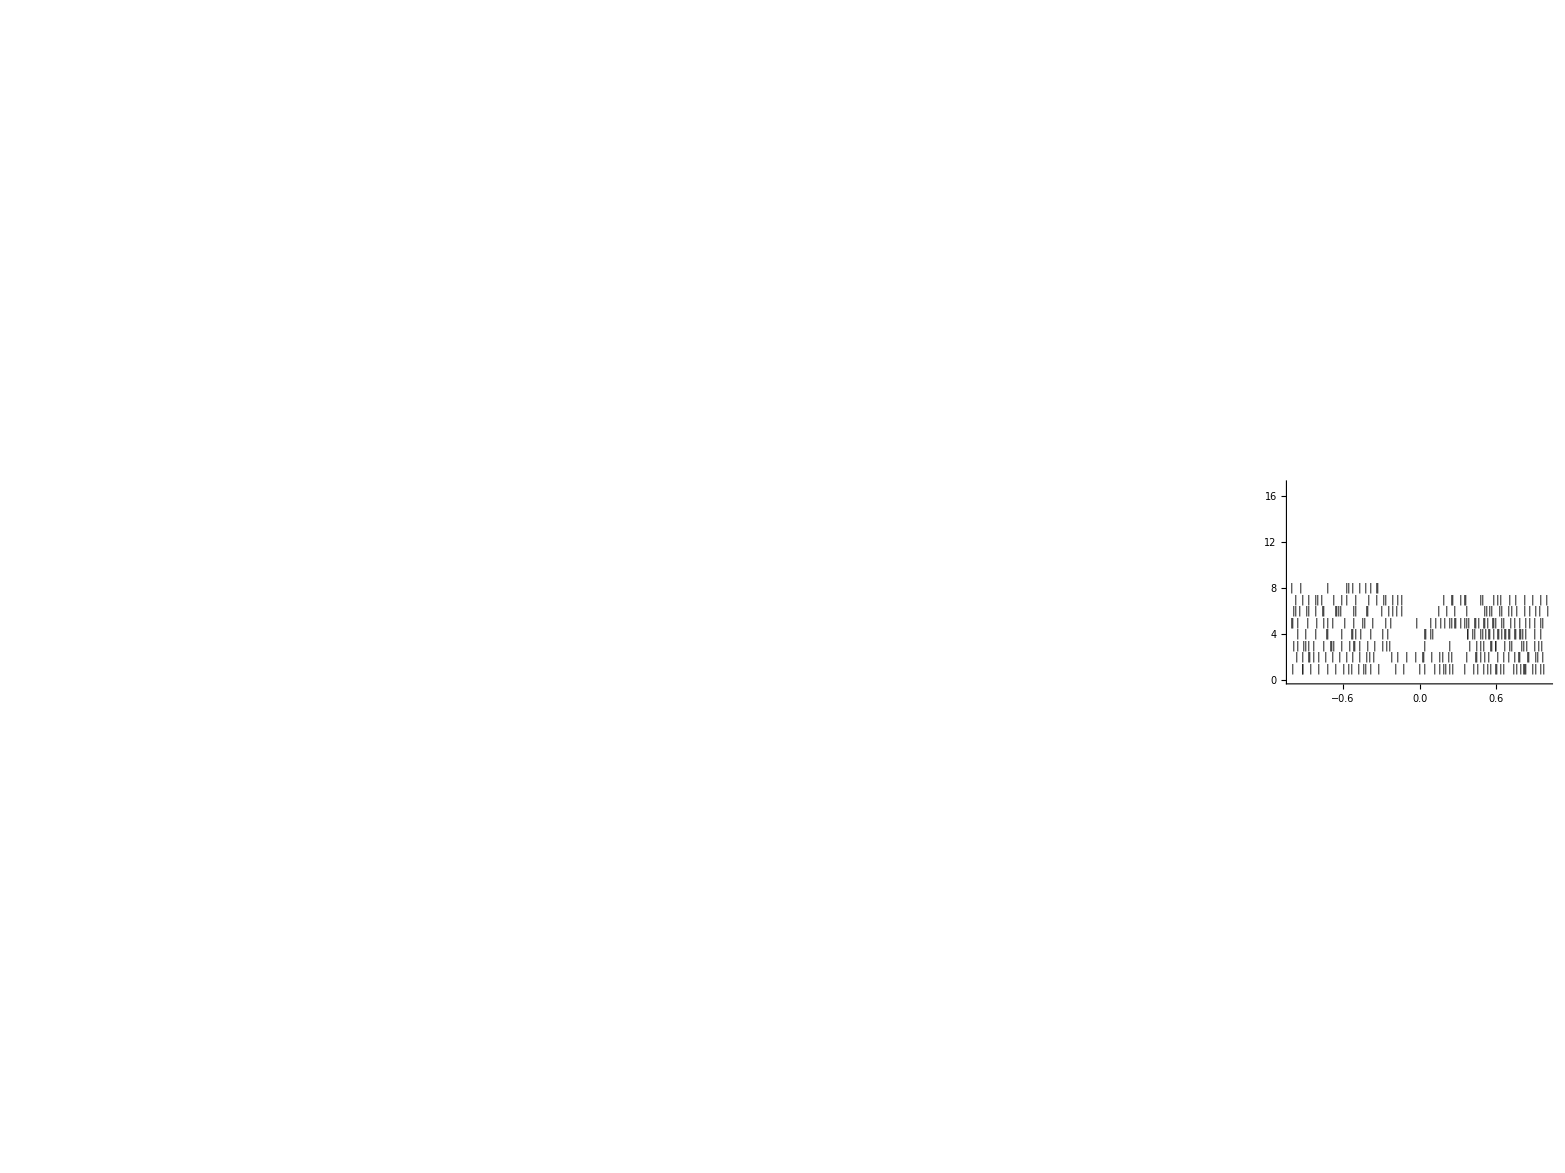

```mathematica
Show[MapIndexed[ Graphics[{Transparent, Circle[],Inset[#1,{Cos[Extract[directions, #2] Degree],Sin[Extract[directions,#2] Degree]}]}]&,rasters], ImageSize-> Scaled[.85]]
```

## Create Peri-Stimulus Time Histograms (PSTHs)

To create a PSTH, you need to bin the spikes, average over multiple trials, convert to firing rate, and display the histogram.  This can then be repeated for each orientation.

Here we can count the number of spikes that fall in each bin across all trials. The Flatten command looks at all the trials together, and here we have set the bin size to 20 ms.

```mathematica
binSize = 0.02 ;
```

```mathematica
binSpikes = Map[BinCounts[#, binSize]&,Map[Flatten, spikeTimes]];
```

Next, we average over the number of trials, and convert to firing rate by dividing by the bin size. This gives us units of spikes/sec.

```mathematica
firingRate = (binSpikes/Last[Dimensions[spikeTimes]])/binSize;
```

Finally, we visualize the PSTHs.  The x-axis is again time, and the y-axis is now firing rate in spikes/s.  Again, we use the Georgopolus format.

```mathematica
psths = MapIndexed[Show[BarChart[#1,PlotLabel-> ToString[Extract[directions,#2] ]°],Axes->True,Ticks -> {{{5,-1},{50,0},{100,1}},Automatic},AxesLabel -> {"time (s)", "spikes/s"}]&,firingRate];
```

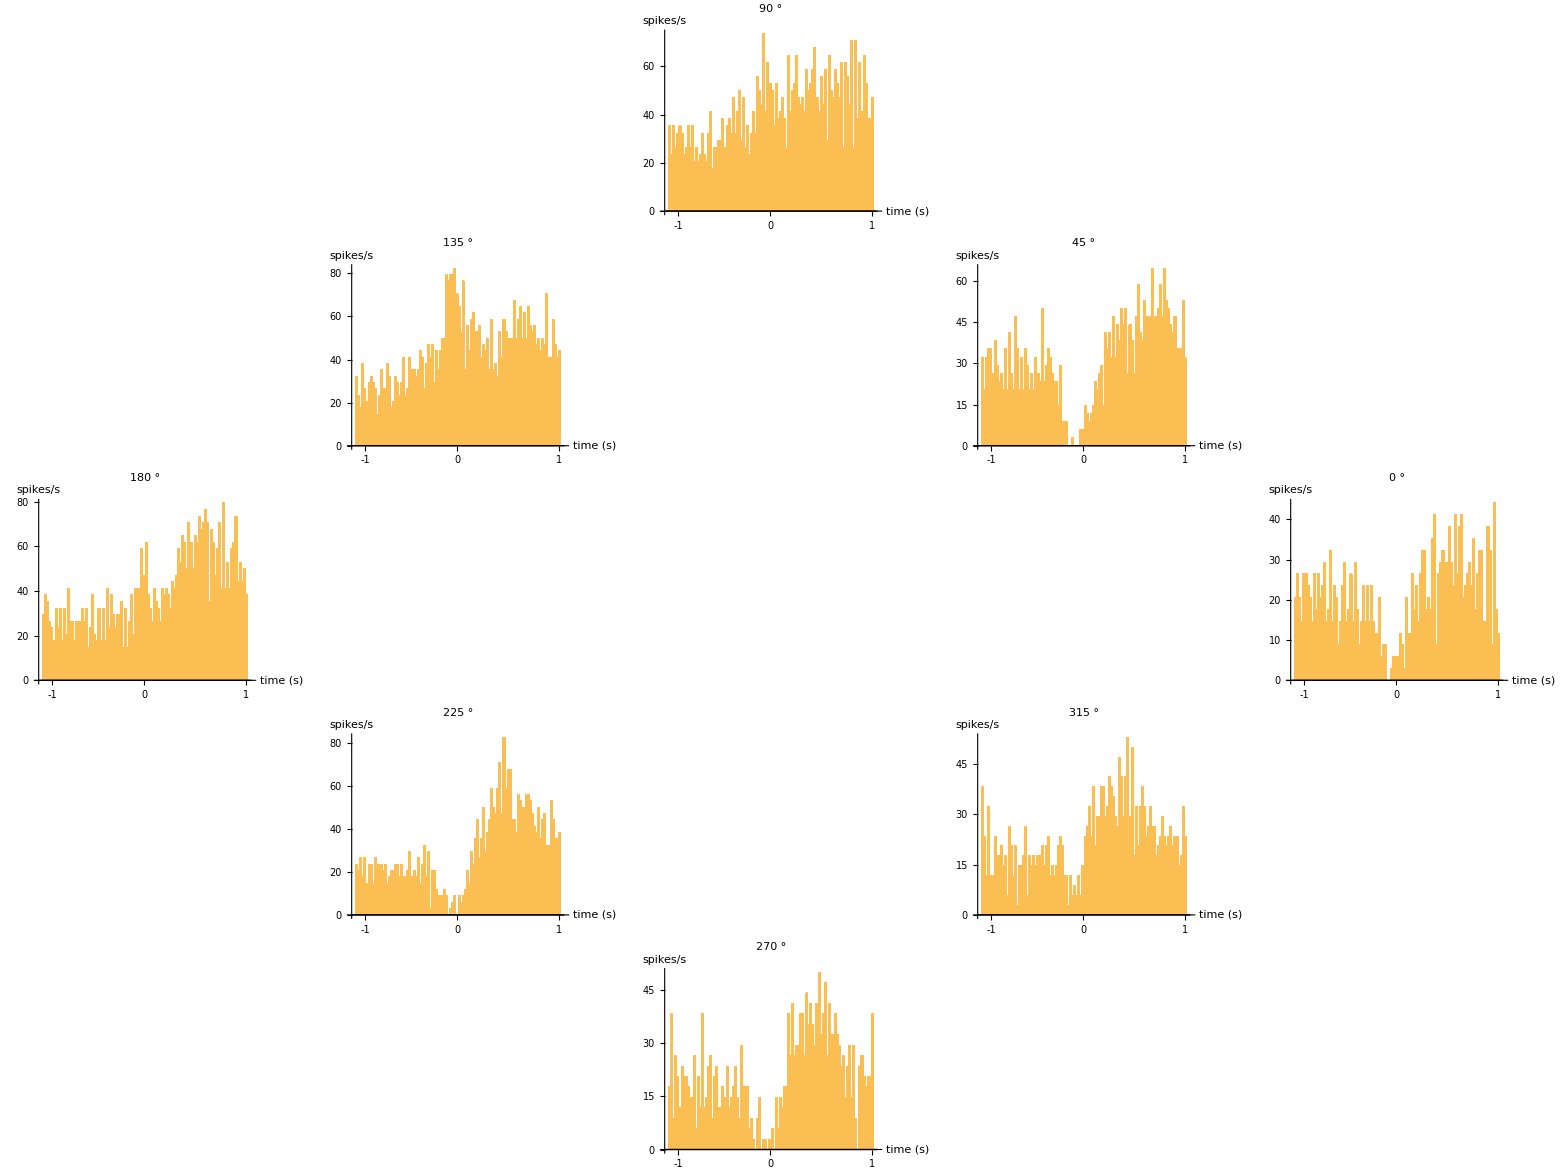

```mathematica
Show[MapIndexed[ Graphics[{Transparent, Circle[],Inset[#1,{Cos[Extract[directions, #2] Degree],Sin[Extract[directions,#2] Degree]}]}]&,psths],ImageSize->Scaled[.85]]
```

## Create the Tuning Curve

To create the tuning curve, convert each PSTH into one value for each direction and create a plot of our results.

For this data, we will take the spikes between -100ms and +100ms around the time of arm movement.  It needs to be re-binned.

```mathematica
startTime = -0.1;
endTime = 0.1;
```

```mathematica
spikes = Map[BinCounts[#, {startTime,endTime,endTime-startTime}]&,Map[Flatten, spikeTimes]];
```

This also needs to be converted to rates (and flattened into one list).

```mathematica
rates = Flatten[(spikes/Last[Dimensions[spikeTimes]])/(endTime - startTime)];
```

Then we manipulate the data into the form used for plotting, and we can plot the tuning data!

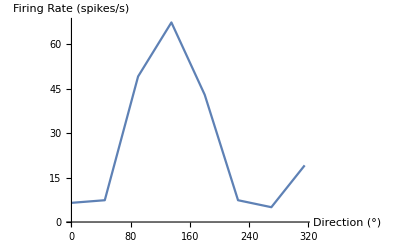

```mathematica
ListLinePlot[Transpose[{directions,rates}],AxesLabel -> {"Direction (°)", "Firing Rate (spikes/s)"}]
```

Further Explorations

Determine the effect of bin size on the shape of the PSTH.  Why should bin size always be greater than 1ms? What happens if your bin size is too large?

Represent the tuning curve as a polar plot.  Why is this a useful representation?

Explore what you can and cannot predict from the tuning curve.  For example, if you know the firing rate of the neuron, can you predict the value of the parameter of interest?

Create the tuning curve by fitting a function to the data.

Authorship information

Monica Linden

June 22, 2017

monica_linden@brown.edu